# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

mass leptons MM!=0, box diagrams with GAUGE=1

Confronto con:
- EW_MM_naive per d=4 -> OK
-Nar per d (box photons and born Z) CON SEMPLIFICAZIONE CARICHE PRIMA DEL CALCOLO DELLE TRACCE

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

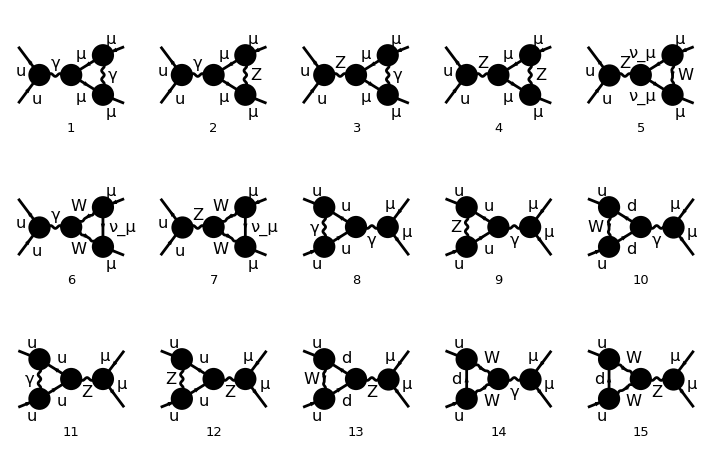

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

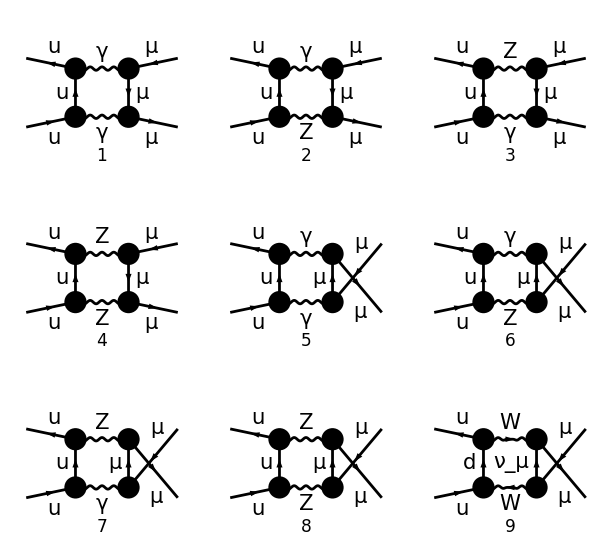

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

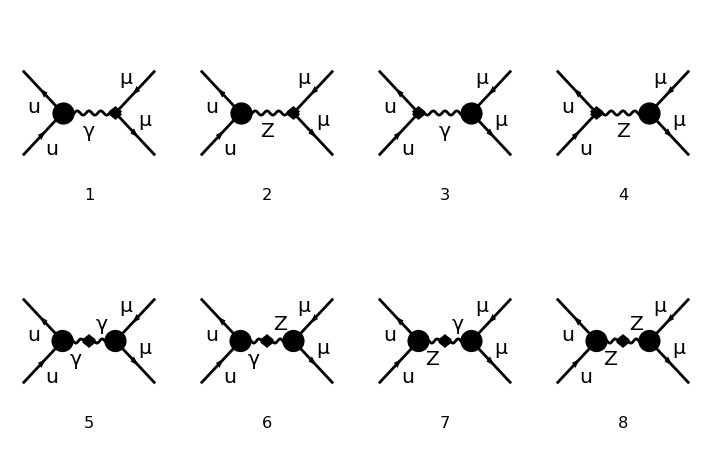

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
tboxzz=totbbox[3][[1]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
uboxzz=totbbox[2][[2]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
wwbox=totbbox[5]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
```

```mathematica
(*tboxzz=tboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
uboxzz=uboxzz/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]]
wwbox=wwbox/.FourMomentum[Internal,1]->Times[-1,FourMomentum[Internal,1]];*)
```

```mathematica
(*confronto Nar*)
tboxzz=tboxzz/.{Q1->-(Q1-P1)}//.{-P1-P2+K2->-K1,P1+P2-K2->K1}
uboxzz=uboxzz/.{Q1->(Q1-P2)}//.2P2-Q1->Q1//.Q1-K1-K2->-Q1+P1+P2//.PropagatorDenominator[Q1-K1,x_]->PropagatorDenominator[-Q1+K1,x]//.PropagatorDenominator[Q1-P2,x_]->PropagatorDenominator[-Q1+P2,x]
```

1/(16 π^4)ⅈ v̄[p1,0].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[-(p1)+q1].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,0].(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).gs[q1-k1].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).v[k1,0] FeynAmpDenominator[1/(p1-q1)^2,1/(p1+p2-q1)^2,1/(-MZ2+(q1)^2),1/(-(q1)+k1)^2] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).gs[p2-q1].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,0].(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).gs[q1-k1].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).v[k1,0] FeynAmpDenominator[1/(p2-q1)^2,1/(p1+p2-q1)^2,1/(-MZ2+(q1)^2),1/(-(q1)+k1)^2] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*BORN*)
born=Part[born1,{2}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.NonCommutative[DiracMatrix[Index[Lorentz,bn1_]],ChiralityProjector[n_]]->NonCommutative[ChiralityProjector[n],DiracMatrix[Index[Lorentz,bn1]]]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(-(ⅈ EL (I3U-QZUl SW2) om_-.ga[Lorbn1])/(CW SW)+(ⅈ EL QZUr SW om_+.ga[Lorbn1])/CW).u[p1,0]],CONJ[ū[k1,0].(-(ⅈ EL (I3L-QZLl SW2) om_-.ga[Lorbn2])/(CW SW)+(ⅈ EL QZLr SW om_+.ga[Lorbn2])/CW).v[k2,0]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(-MZ2+(k1+k2)^2)

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Propagators

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
bornpropag2
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (p1-q1)^2 (p1+p2-q1)^2 (-MZ2+(q1)^2) (q1-k1)^2)

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (p2-q1)^2 (p1+p2-q1)^2 (-MZ2+(q1)^2) (q1-k1)^2)

SP[Lorbn1,Lorbn2]/(-MZ2+(k1+k2)^2)

```mathematica
intdenT[expr_]:=Module[{t,t1,A1},

D1=1/List@@Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&];
dennnt=Sort[Table[If[Head[D1[[i]]]===Power,D1[[i,1]]->Sqrt[dn[i]],D1[[i]]->dn[i]],{i,1,Length[D1]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D1]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];
t=ReplaceAllRestricted[expr,dennnt,{SP}];
expon=DENt@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D1]}];
t1=t*expon//.canden//.K1+K2->Sqrt[S];

t1
];


intdenU[expr_]:=Module[{t,t1,A2},

D2=1/List@@Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&];
dennnu=Sort[Table[If[Head[D2[[i]]]===Power,D2[[i,1]]->Sqrt[dn[i]],D2[[i]]->dn[i]],{i,1,Length[D2]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D2]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];
t=ReplaceAllRestricted[expr,dennnu,{SP}];
expon=DENu@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D2]}];
t1=t*expon//.canden//.K1+K2->Sqrt[S];

t1
];
```

```mathematica
intdenU[unumerat*bornpropag2]
```

(ⅈ DENu[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2])/(16 π^4 (-MZ2+S))

```mathematica
intdenT[tnumerat*bornpropag2]
```

(ⅈ DENt[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4] SP[Lorbn1,Lorbn2])/(16 π^4 (-MZ2+S))

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] = -4 I myEps[a1,a2,a3,a4];
myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,Index[Lorentz,index]]; 
  risultato
 ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=0;
SP/:SP[K1,K1]:=0;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2;
SP/: SP[P1,K1]:=(-T)/2;
SP/: SP[P2,K2]:=(-T)/2; 
SP/:SP[P1,K2]:=(-U)/2; SP/:SP[P2,K1]:=(-U)/2;
```

```mathematica
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracMatrix[b],y]/;Head[b]=!=FourMomentum;
SP/:SP[a_,b_]*sp___*TR[x___,DiracMatrix[a_],y___]:=sp*TR[x,DiracSlash[b],y]/;Head[b]===FourMomentum;
```

```mathematica
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]; 
TR[a___,m_,b__,m_,c___] :=(-1)^Length[{b}] MM2 TR[a,b,c]+ Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];
TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=MM2*TR[x,y];
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=MM2*TR[x,y];
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
```

```mathematica
LARINtot:= traceff4[x___,G5,y___]:>LARIN[ traceff4[x,G5,y] ];
```

```mathematica
LARIN[expr_]:=Module[{ris,a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,a12},
a1 = Index[Lorentz,Unique["x"]];
a2 = Index[Lorentz,Unique["x"]];
a3 = Index[Lorentz,Unique["x"]];
a4 = Index[Lorentz,Unique["x"]];
a5 = Index[Lorentz,Unique["x"]];
a6 = Index[Lorentz,Unique["x"]];
a7= Index[Lorentz,Unique["x"]];
a8 = Index[Lorentz,Unique["x"]];
a9 = Index[Lorentz,Unique["x"]];
a10 = Index[Lorentz,Unique["x"]];
a11 = Index[Lorentz,Unique["x"]];
a12 = Index[Lorentz,Unique["x"]];

pos = Position[ expr, G5];
Which[Length[pos]===1,
pos1 = Position[ expr, G5][[1,1]];
ris = I/24 fg51 myEps[a1,a2,a3,a4]*ReplacePart[expr,pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]] ],
Length[pos]===2,
pos1 = Position[ expr, G5][[1,1]];
pos2 = Position[ expr, G5][[2,1]];
ris = (I/24)^2 fg52 myEps[a1,a2,a3,a4]*myEps[a5,a6,a7,a8]*ReplacePart[expr,{pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]],
pos2->Sequence[DiracMatrix[a5],DiracMatrix[a6],DiracMatrix[a7],DiracMatrix[a8]]} ],
Length[pos]===3,
pos1 = Position[ expr, G5][[1,1]];
pos2 = Position[ expr, G5][[2,1]];
pos3 = Position[ expr, G5][[3,1]];
(*cambiare MYEPS in myEps per verificare i prodotti con 3 levicivita,ovvero conta l'ordine dei prodotti?*)
ris = (I/24)^3 fg53 myEps[a1,a2,a3,a4]*myEps[a5,a6,a7,a8]*myEps[a9,a10,a11,a12]*ReplacePart[expr,{pos1->Sequence[DiracMatrix[a1],DiracMatrix[a2],DiracMatrix[a3],DiracMatrix[a4]],
pos2->Sequence[DiracMatrix[a5],DiracMatrix[a6],DiracMatrix[a7],DiracMatrix[a8]],pos3->Sequence[DiracMatrix[a9],DiracMatrix[a10],DiracMatrix[a11],DiracMatrix[a12]]} ]
];

ris					   
];
```

```mathematica
(*semplificazione propagatore stato f*)
SEMPLtr={traceff4[a___,p[MM+DiracSlash[b__]],c___]/;OddQ[Count[traceff4[a,p[MM+DiracSlash[b]],c],DiracMatrix|DiracSlash,{2},Heads->True]]->traceff4[a,DiracSlash[b],c],
traceff4[a___,p[MM+DiracSlash[b__]],c___]/;EvenQ[Count[traceff4[a,p[MM+DiracSlash[b]],c],DiracMatrix|DiracSlash,{2},Heads->True]]->traceff4[a,MM,c]};
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{i,tr1i,tr2i,tr3i,tr4i,tr1f,tr2f,tr3f,tr4f,tracciai,tracciaf,chii,chff,omi,omf},

(*Prova traceff con mom k1 e p1 >0 v vbar->p-m uubar->p+m*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,1,b___]:=traceff4[a,b];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];

(*stato i*)
omi=Count[statoi[[1]],_ChiralityProjector,Infinity];
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}];
tr2i=Map[Distribute,1/(2^omi) DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};
tr2i=tr2i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)

tr3i=Collect[Collect[tr2i,traceff4[__],Simplify]//.LARINtot//.traceff4->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand];
tr4i=tr3i//.TR->myTr;

Print["stato i ",1/(2^omi) DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
omf=Count[statof[[1]],_ChiralityProjector,Infinity];
tr1f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr1f[[i]]]},{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.SEMPLtr;
tr2f=Flatten[Map[Distribute,1/(2^omf) DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity]];

tr2f=tr2f*chargetot[[2]]//.List->Plus//Simplify;(*prova*)

tr3f=Collect[Collect[tr2f,traceff4[__],Simplify]//.LARINtot//.traceff4->trr//.trr->TR,{I3L,I3U,QU,QL,Alfa,EL,Pi,I,CW,CW2,SW,SW2,MM,MM2},Expand];
tr4f=tr3f//.TR->myTr;

Print["stato f ",1/(2^omf) DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr4i,tr4f}]

];
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_,conjbornchains_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1]/.ChiralityProjector[x_]->con ChiralityProjector[x];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbi2=tbi(*Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List*);(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
stati=stati//.con ChiralityProjector[n_]->ChiralityProjector[-n];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[tbf[[i]]/.MM+DiracSlash[a__]->p[MM+DiracSlash[a]]//.List->f,{i,1,Length[tbf]}],Plus->Sequence,{3},Heads->True]//.f->List;
tbf3=DeleteCases[tbf2,0,1];
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
statf=statf//.con ChiralityProjector[n_]->ChiralityProjector[-n];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

#### CHARGES

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[Q1,Q1]->Q1^2};
```

```mathematica
(*per calcolare altri box con photon/Z(caso boxtt o incrociato boxuu) o W(boxuu) basta cambiare la cariche, essendo le tracce della stessa tipologia*)
```

#### amplitudes

```mathematica
boxtt=traces[fermiontrace[tboxzz,conjbornchains][[1]],fermiontrace[tboxzz,conjbornchains][[2]]]//.MYEPS->myEps;
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[-(p1)+q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]]}

stato f {{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1-G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor4],1+G5,gs[q1-k1],ga[Lor2],1+G5,gs[k1],1-G5,ga[Lorbn2]]}}

```mathematica
boxuu=traces[fermiontrace[uboxzz,conjbornchains][[1]],fermiontrace[uboxzz,conjbornchains][[2]]]//.MYEPS->myEps;
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i {1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1-G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1-G5,gs[p2],1-G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1+G5,ga[Lorbn1]],1/8 traceff4[gs[p1],ga[Lor1],1+G5,gs[p2-q1],ga[Lor3],1+G5,gs[p2],1-G5,ga[Lorbn1]]}

stato f {{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1-G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1-G5,gs[k1],1-G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1+G5,ga[Lorbn2]]},{1/8 traceff4[gs[k2],ga[Lor2],1+G5,gs[q1-k1],ga[Lor4],1+G5,gs[k1],1-G5,ga[Lorbn2]]}}

## Simplifications

```mathematica
(*regole di sostituzione dei denominatori e regole inverse PER CONFRONTO NAR*)
SOST={-MZ2+(P2+Q1)^2->DMZQ1P2,-MZ2 ZGAUGE+(P2+Q1)^2->DMZGQ1P2,
-MW2+(P2+Q1)^2->DMWQ1P2,-MW2 WGAUGE+(P2+Q1)^2->DMWGQ1P2,
-MZ2+(K1+K2)^2->DMZK1K2,-MZ2 ZGAUGE+(K1+K2)^2->DMZGK1K2,
-MZ2+(P2+Q1-K1-K2)^2->DMZQ1P2K1K2,-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2->DMZGQ1P2K1K2,
-MW2+(P2+Q1-K1-K2)^2->DMWQ1P2K1K2,-MW2 WGAUGE+(P2+Q1-K1-K2)^2->DMWGQ1P2K1K2,
MZ2-(K1+K2)^2->-DMZK1K2,MZ2 ZGAUGE-(K1+K2)^2->-DMZGK1K2,
MZ2-(P2+Q1)^2->-DMZQ1P2,MZ2 ZGAUGE-(P2+Q1)^2->-DMZGQ1P2,
MZ2-(P2+Q1-K1-K2)^2->-DMZQ1P2K1K2,MZ2 ZGAUGE-(P2+Q1-K1-K2)^2->-DMZGQ1P2K1K2,
MW2-(P2+Q1)^2->-DMWQ1P2,MW2 WGAUGE-(P2+Q1)^2->-DMWGQ1P2,
MW2-(P2+Q1-K1-K2)^2->-DMWQ1P2K1K2,MW2 WGAUGE-(P2+Q1-K1-K2)^2->-DMWGQ1P2K1K2,
-MZ2+(P1+P2-Q1)^2->DMZQ1P1P2,MZ2-(P1+P2-Q1)^2->-DMZQ1P1P2,
-MZ2+Q1^2->DMZQ1,MZ2-Q1^2->-DMZQ1,

-MM2+(Q1-K1)^2->DMMQ1K1,
-MM2+(-Q1+K1)^2->DMMQ1K1,
-MM2+(-Q1+K2)^2->DMMQ1K2,
(P1+P2-Q1)->Sqrt[DQ1P1P2],


-MM2+(P2-Q1-K2)^2->DMMQ1P2K2,
-MM2+(P2-Q1-K1)^2->DMMQ1P2K1,
MM2-(P2-Q1-K2)^2->-DMMQ1P2K2,
MM2-(P2-Q1-K1)^2->-DMMQ1P2K1,
(P2-Q1-K1-K2)->Sqrt[DQ1P2K1K2],
(P2+Q1)->Sqrt[DQ1P2],
(P2-Q1)->Sqrt[DmQ1P2],
(P1-Q1)->Sqrt[DQ1P1],
(K1+K2)->Sqrt[DK1K2],
(Q1-K1)->Sqrt[DMMQ1K1],
Q1^n_/;EvenQ[n]->DQ1^(n/2),Q1^n_/;OddQ[n]&&n<0->DQ1^((n+1)/2)1/Q1,Q1^n_/;OddQ[n]&&n>0->DQ1^((n-1)/2)Q1,
-Q1^n_/;EvenQ[n]->-DQ1^(n/2),-Q1^n_/;OddQ[n]->-DQ1^((n-1)/2)Q1};

SOSTINV={DMZQ1P2->-MZ2+(P2+Q1)^2,DMZGQ1P2->-MZ2 ZGAUGE+(P2+Q1)^2,
DMWQ1P2->-MW2+(P2+Q1)^2,DMWGQ1P2->-MW2 WGAUGE+(P2+Q1)^2,
DMZK1K2->-MZ2+(K1+K2)^2,DMZGK1K2->-MZ2 ZGAUGE+(K1+K2)^2,
DMZQ1P2K1K2->-MZ2+(P2+Q1-K1-K2)^2,DMZGQ1P2K1K2->-MZ2 ZGAUGE+(P2+Q1-K1-K2)^2,
DMWQ1P2K1K2->-MW2+(P2+Q1-K1-K2)^2,DMWGQ1P2K1K2->-MW2 WGAUGE+(P2+Q1-K1-K2)^2,

DQ1P2K1K2->(P2+Q1-K1-K2)^2,
DMMQ1P2K2->-MM2+(P2+Q1-K2)^2,
DMMQ1P2K1->-MM2+(P2+Q1-K1)^2,
DQ1P2->(P2+Q1)^2,
DQ1P1->(-P1+Q1)^2,
DK1K2->(K1+K2)^2,
DQ1->Q1^2};
```

### box T

```mathematica
boxtt=boxtt//Expand;
```

```mathematica
iep=Select[boxtt[[1]],MemberQ[#,_myEps,Infinity]&];
inep=Select[boxtt[[1]],FreeQ[#,_myEps,Infinity]&];

fep=Select[boxtt[[2]],MemberQ[#,_myEps,Infinity]&];
fnep=Select[boxtt[[2]],FreeQ[#,_myEps,Infinity]&];
```

```mathematica
(*Il fatto che però ci siano solo 3 impulsi indipendenti (per la conserv. p1+p2=k1+k2) rende i termini con myEps nulli perché non ci sono abbastanza quantità per saturare gli indici mantenendo l’antisimmetria.
quindi i prodotti sono solo fra termini con myEps e senza myEps ma non misti.*)
```

#### myEps

```mathematica
Tepsi=iep*intdenT[tnumerat*bornpropag2]//.{MM->0,MM2->0}//Expand;
```

```mathematica
Teps=ParallelSum[Tepsi[[i]]*fep[[j]]//Expand,{i,1,Length[Tepsi]},{j,1,Length[fep]}];
```

#### NO myEps

```mathematica
Tneps=Collect[inep*fnep*intdenT[tnumerat*bornpropag2]//Expand,SP[__],Simplify];
```

```mathematica
amplT=Teps+Tneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//Expand;
```

### box U

```mathematica
boxuu=boxuu//Expand;
```

```mathematica
iepu=Select[boxuu[[1]],MemberQ[#,_myEps,Infinity]&];
inepu=Select[boxuu[[1]],FreeQ[#,_myEps,Infinity]&];

fepu=Select[boxuu[[2]],MemberQ[#,_myEps,Infinity]&];
fnepu=Select[boxuu[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Uepsi=iepu*intdenU[unumerat*bornpropag2]//Expand;
```

```mathematica
Ueps=ParallelSum[Uepsi[[i]]*fepu[[j]]//Expand,{i,1,Length[Uepsi]},{j,1,Length[fepu]}];
```

#### NO myEps

```mathematica
Uneps=Collect[inepu*fnepu*intdenU[unumerat*bornpropag2]//Expand,SP[__],Simplify];
```

```mathematica
amplU=Ueps+Uneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//Expand;
```

## confronto NAr

```mathematica
not={(*fg52->1,*)im->I,s13->-2SP[P1,K1],s23->-2SP[P2,K1],s12->2 SP[P1,P2],ml->MM,LlZ->el /(SW CW),UuZ->el /(SW CW),
Llph->QL el,Uuph->QU el,gVl->(I3L-2QL SW2),gVu->(I3U-2QU SW2),gAl->I3L,gAu->I3U,mZ2->MZ2,k1->FourMomentum[Internal,1],
p1->FourMomentum[Incoming,1],p4->FourMomentum[Outgoing,2],p2->FourMomentum[Incoming,2],p3->FourMomentum[Outgoing,1],n->d};
```

### caso box ph/Z born Z

#### nar:

```mathematica
(*A1:{sp[k1,k1],sp[k1-p1,k1-p1],sp[k1-p1-p2,k1-p1-p2]-mZ^2,sp[k1-p3,k1-p3]},A2:{sp[k1,k1],sp[k1-p2,k1-p2],sp[k1-p1-p2,k1-p1-p2]-mZ^2,sp[k1-p3,k1-p3]},A3:{sp[k1,k1]-mZ^2,sp[k1-p1,k1-p1],sp[k1-p1-p2,k1-p1-p2],sp[k1-p3,k1-p3]},A4:{sp[k1,k1]-mZ^2,sp[k1-p2,k1-p2],sp[k1-p1-p2,k1-p1-p2],sp[k1-p3,k1-p3]},*)
```

```mathematica
F1Zsq1g=+J[A1,-1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-576/(-mZ2+s12)*s13+1640/(-mZ2+s12)*n*s13-5749/3/(-mZ2+s12)*n^2*s13+90259/72/(-mZ2+s12)*n^3*s13-37961/72/(-mZ2+s12)*n^4*s13+44131/288/(-mZ2+s12)*n^5*s13-280/9/(-mZ2+s12)*n^6*s13+599/144/(-mZ2+s12)*n^7*s13-23/72/(-mZ2+s12)*n^8*s13+1/96/(-mZ2+s12)*n^9*s13)+J[A1,-1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+288/(-mZ2+s12)*s13-256/(-mZ2+s12)*n*s13+617/6/(-mZ2+s12)*n^2*s13-107/4/(-mZ2+s12)*n^3*s13+25/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A1,-1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-96/(-mZ2+s12)*s13-64/(-mZ2+s12)*n*s13+56/(-mZ2+s12)*n^2*s13-8/(-mZ2+s12)*n^3*s13)+J[A1,-1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13-224/3/(-mZ2+s12)*n*s13+377/6/(-mZ2+s12)*n^2*s13-289/12/(-mZ2+s12)*n^3*s13+25/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A1,-1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2 *(-16/(-mZ2+s12)*s13+6/(-mZ2+s12)*n*s13)+J[A1,0,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+544/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-4520/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+30305/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-37099/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+28643/72/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-15281/144/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+733/36/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-193/72/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A1,0,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-272/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,0,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-192/(-mZ2+s12)*s13-288/(-mZ2+s12)*s12+232/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-80/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13)+J[A1,0,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,0,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A1,0,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13+3200/(-mZ2+s12)*s12-800/3/(-mZ2+s12)*n*s13-29296/3/(-mZ2+s12)*n*s12+4189/9/(-mZ2+s12)*n^2*s13+110174/9/(-mZ2+s12)*n^2*s12-16061/36/(-mZ2+s12)*n^3*s13-33499/4/(-mZ2+s12)*n^3*s12+1553/6/(-mZ2+s12)*n^4*s13+41635/12/(-mZ2+s12)*n^4*s12-4523/48/(-mZ2+s12)*n^5*s13-14507/16/(-mZ2+s12)*n^5*s12+43/2/(-mZ2+s12)*n^6*s13+150/(-mZ2+s12)*n^6*s12-71/24/(-mZ2+s12)*n^7*s13-365/24/(-mZ2+s12)*n^7*s12+2/9/(-mZ2+s12)*n^8*s13+31/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-1/48/(-mZ2+s12)*n^9*s12)+J[A1,0,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13+5248/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13-2185/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13+865/6/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13-41/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+1/2/(-mZ2+s12)*n^5*s12)+J[A1,0,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+576/(-mZ2+s12)*s13+576/(-mZ2+s12)*s12-336/(-mZ2+s12)*n*s13-288/(-mZ2+s12)*n*s12+48/(-mZ2+s12)*n^2*s13+32/(-mZ2+s12)*n^2*s12)+J[A1,0,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13-64/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13+448/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13-377/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13+289/6/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13-25/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+1/2/(-mZ2+s12)*n^5*s12)+J[A1,0,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-12/(-mZ2+s12)*n*s12)+J[A1,0,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+544/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-4520/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+30305/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-37099/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+28643/72/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-15281/144/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+733/36/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-193/72/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A1,0,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-272/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,0,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-192/(-mZ2+s12)*s13-288/(-mZ2+s12)*s12+232/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-80/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13)+J[A1,0,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,0,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A1,0,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13*mZ^2-960/(-mZ2+s12)*s13^2+3200/(-mZ2+s12)*s12*mZ^2+64/(-mZ2+s12)*s12*s13-800/3/(-mZ2+s12)*n*s13*mZ^2+2480/(-mZ2+s12)*n*s13^2-29296/3/(-mZ2+s12)*n*s12*mZ^2-800/3/(-mZ2+s12)*n*s12*s13+4189/9/(-mZ2+s12)*n^2*s13*mZ^2-7309/3/(-mZ2+s12)*n^2*s13^2+110174/9/(-mZ2+s12)*n^2*s12*mZ^2+4189/9/(-mZ2+s12)*n^2*s12*s13-16061/36/(-mZ2+s12)*n^3*s13*mZ^2+10519/9/(-mZ2+s12)*n^3*s13^2-33499/4/(-mZ2+s12)*n^3*s12*mZ^2-16061/36/(-mZ2+s12)*n^3*s12*s13+1553/6/(-mZ2+s12)*n^4*s13*mZ^2-10007/36/(-mZ2+s12)*n^4*s13^2+41635/12/(-mZ2+s12)*n^4*s12*mZ^2+1553/6/(-mZ2+s12)*n^4*s12*s13-4523/48/(-mZ2+s12)*n^5*s13*mZ^2+214/9/(-mZ2+s12)*n^5*s13^2-14507/16/(-mZ2+s12)*n^5*s12*mZ^2-4523/48/(-mZ2+s12)*n^5*s12*s13+43/2/(-mZ2+s12)*n^6*s13*mZ^2+41/18/(-mZ2+s12)*n^6*s13^2+150/(-mZ2+s12)*n^6*s12*mZ^2+43/2/(-mZ2+s12)*n^6*s12*s13-71/24/(-mZ2+s12)*n^7*s13*mZ^2-5/9/(-mZ2+s12)*n^7*s13^2-365/24/(-mZ2+s12)*n^7*s12*mZ^2-71/24/(-mZ2+s12)*n^7*s12*s13+2/9/(-mZ2+s12)*n^8*s13*mZ^2+1/36/(-mZ2+s12)*n^8*s13^2+31/36/(-mZ2+s12)*n^8*s12*mZ^2+2/9/(-mZ2+s12)*n^8*s12*s13-1/144/(-mZ2+s12)*n^9*s13*mZ^2-1/48/(-mZ2+s12)*n^9*s12*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13)+J[A1,0,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13*mZ^2+480/(-mZ2+s12)*s13^2-1600/(-mZ2+s12)*s12*mZ^2-32/(-mZ2+s12)*s12*s13+212/3/(-mZ2+s12)*n*s13*mZ^2-300/(-mZ2+s12)*n*s13^2+5248/3/(-mZ2+s12)*n*s12*mZ^2+212/3/(-mZ2+s12)*n*s12*s13-55/(-mZ2+s12)*n^2*s13*mZ^2+122/3/(-mZ2+s12)*n^2*s13^2-2185/3/(-mZ2+s12)*n^2*s12*mZ^2-55/(-mZ2+s12)*n^2*s12*s13+115/6/(-mZ2+s12)*n^3*s13*mZ^2+4/(-mZ2+s12)*n^3*s13^2+865/6/(-mZ2+s12)*n^3*s12*mZ^2+115/6/(-mZ2+s12)*n^3*s12*s13-3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-41/3/(-mZ2+s12)*n^4*s12*mZ^2-3/(-mZ2+s12)*n^4*s12*s13+1/6/(-mZ2+s12)*n^5*s13*mZ^2+1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A1,0,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+576/(-mZ2+s12)*s13*mZ^2+576/(-mZ2+s12)*s12*mZ^2+576/(-mZ2+s12)*s12*s13-336/(-mZ2+s12)*n*s13*mZ^2-48/(-mZ2+s12)*n*s13^2-288/(-mZ2+s12)*n*s12*mZ^2-336/(-mZ2+s12)*n*s12*s13+48/(-mZ2+s12)*n^2*s13*mZ^2+16/(-mZ2+s12)*n^2*s13^2+32/(-mZ2+s12)*n^2*s12*mZ^2+48/(-mZ2+s12)*n^2*s12*s13)+J[A1,0,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-64/(-mZ2+s12)*s12*mZ^2-32/(-mZ2+s12)*s12*s13+212/3/(-mZ2+s12)*n*s13*mZ^2+188/3/(-mZ2+s12)*n*s13^2+448/3/(-mZ2+s12)*n*s12*mZ^2+212/3/(-mZ2+s12)*n*s12*s13-55/(-mZ2+s12)*n^2*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s13^2-377/3/(-mZ2+s12)*n^2*s12*mZ^2-55/(-mZ2+s12)*n^2*s12*s13+115/6/(-mZ2+s12)*n^3*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s13^2+289/6/(-mZ2+s12)*n^3*s12*mZ^2+115/6/(-mZ2+s12)*n^3*s12*s13-3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-25/3/(-mZ2+s12)*n^4*s12*mZ^2-3/(-mZ2+s12)*n^4*s12*s13+1/6/(-mZ2+s12)*n^5*s13*mZ^2+1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A1,0,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13*mZ^2+16/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+16/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s13*mZ^2-12/(-mZ2+s12)*n*s12*mZ^2-4/(-mZ2+s12)*n*s12*s13)+J[A1,1,-1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s12)+J[A1,1,-1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A1,1,-1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A1,1,-1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A1,1,-1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s12)+J[A1,1,0,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A1,1,0,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,1,0,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12+24/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12)+J[A1,1,0,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,1,0,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A1,1,0,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-2112/(-mZ2+s12)*s13+64/(-mZ2+s12)*s12+6256/(-mZ2+s12)*n*s13-800/3/(-mZ2+s12)*n*s12-22715/3/(-mZ2+s12)*n^2*s13+4189/9/(-mZ2+s12)*n^2*s12+29969/6/(-mZ2+s12)*n^3*s13-16061/36/(-mZ2+s12)*n^3*s12-72115/36/(-mZ2+s12)*n^4*s13+1553/6/(-mZ2+s12)*n^4*s12+36889/72/(-mZ2+s12)*n^5*s13-4523/48/(-mZ2+s12)*n^5*s12-1523/18/(-mZ2+s12)*n^6*s13+43/2/(-mZ2+s12)*n^6*s12+317/36/(-mZ2+s12)*n^7*s13-71/24/(-mZ2+s12)*n^7*s12-19/36/(-mZ2+s12)*n^8*s13+2/9/(-mZ2+s12)*n^8*s12+1/72/(-mZ2+s12)*n^9*s13-1/144/(-mZ2+s12)*n^9*s12)+J[A1,1,0,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+1056/(-mZ2+s12)*s13-32/(-mZ2+s12)*s12-1060/(-mZ2+s12)*n*s13+212/3/(-mZ2+s12)*n*s12+412/(-mZ2+s12)*n^2*s13-55/(-mZ2+s12)*n^2*s12-239/3/(-mZ2+s12)*n^3*s13+115/6/(-mZ2+s12)*n^3*s12+8/(-mZ2+s12)*n^4*s13-3/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13+1/6/(-mZ2+s12)*n^5*s12)+J[A1,1,0,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13+576/(-mZ2+s12)*s12-256/(-mZ2+s12)*n*s13-336/(-mZ2+s12)*n*s12+88/(-mZ2+s12)*n^2*s13+48/(-mZ2+s12)*n^2*s12-8/(-mZ2+s12)*n^3*s13)+J[A1,1,0,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13-32/(-mZ2+s12)*s12-236/3/(-mZ2+s12)*n*s13+212/3/(-mZ2+s12)*n*s12+212/3/(-mZ2+s12)*n^2*s13-55/(-mZ2+s12)*n^2*s12-29/(-mZ2+s12)*n^3*s13+115/6/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s13-3/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13+1/6/(-mZ2+s12)*n^5*s12)+J[A1,1,0,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13+16/(-mZ2+s12)*s12+8/(-mZ2+s12)*n*s13-4/(-mZ2+s12)*n*s12)+J[A1,1,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13*mZ^2-128/(-mZ2+s12)*s13^2-1600/(-mZ2+s12)*s12*mZ^2-1632/(-mZ2+s12)*s12*s13+1600/(-mZ2+s12)*s12^2-14248/3/(-mZ2+s12)*n*s13*mZ^2+1504/3/(-mZ2+s12)*n*s13^2+14648/3/(-mZ2+s12)*n*s12*mZ^2+5000/(-mZ2+s12)*n*s12*s13-14648/3/(-mZ2+s12)*n*s12^2+105985/18/(-mZ2+s12)*n^2*s13*mZ^2-7250/9/(-mZ2+s12)*n^2*s13^2-55087/9/(-mZ2+s12)*n^2*s12*mZ^2-37745/6/(-mZ2+s12)*n^2*s12*s13+55087/9/(-mZ2+s12)*n^2*s12^2-142715/36/(-mZ2+s12)*n^3*s13*mZ^2+6218/9/(-mZ2+s12)*n^3*s13^2+33499/8/(-mZ2+s12)*n^3*s12*mZ^2+17239/4/(-mZ2+s12)*n^3*s12*s13-33499/8/(-mZ2+s12)*n^3*s12^2+12843/8/(-mZ2+s12)*n^4*s13*mZ^2-6209/18/(-mZ2+s12)*n^4*s13^2-41635/24/(-mZ2+s12)*n^4*s12*mZ^2-128005/72/(-mZ2+s12)*n^4*s12*s13+41635/24/(-mZ2+s12)*n^4*s12^2-19499/48/(-mZ2+s12)*n^5*s13*mZ^2+920/9/(-mZ2+s12)*n^5*s13^2+14507/32/(-mZ2+s12)*n^5*s12*mZ^2+65857/144/(-mZ2+s12)*n^5*s12*s13-14507/32/(-mZ2+s12)*n^5*s12^2+257/4/(-mZ2+s12)*n^6*s13*mZ^2-157/9/(-mZ2+s12)*n^6*s13^2-75/(-mZ2+s12)*n^6*s12*mZ^2-2627/36/(-mZ2+s12)*n^6*s12*s13+75/(-mZ2+s12)*n^6*s12^2-49/8/(-mZ2+s12)*n^7*s13*mZ^2+14/9/(-mZ2+s12)*n^7*s13^2+365/48/(-mZ2+s12)*n^7*s12*mZ^2+497/72/(-mZ2+s12)*n^7*s12*s13-365/48/(-mZ2+s12)*n^7*s12^2+23/72/(-mZ2+s12)*n^8*s13*mZ^2-1/18/(-mZ2+s12)*n^8*s13^2-31/72/(-mZ2+s12)*n^8*s12*mZ^2-25/72/(-mZ2+s12)*n^8*s12*s13+31/72/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2+1/96/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13-1/96/(-mZ2+s12)*n^9*s12^2)+J[A1,1,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+800/(-mZ2+s12)*s12*mZ^2+816/(-mZ2+s12)*s12*s13-800/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-2624/3/(-mZ2+s12)*n*s12*mZ^2-902/(-mZ2+s12)*n*s12*s13+2624/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+2185/6/(-mZ2+s12)*n^2*s12*mZ^2+376/(-mZ2+s12)*n^2*s12*s13-2185/6/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-865/12/(-mZ2+s12)*n^3*s12*mZ^2-431/6/(-mZ2+s12)*n^3*s12*s13+865/12/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+41/6/(-mZ2+s12)*n^4*s12*mZ^2+6/(-mZ2+s12)*n^4*s12*s13-41/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A1,1,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12*mZ^2-192/(-mZ2+s12)*s12*s13+288/(-mZ2+s12)*s12^2+24/(-mZ2+s12)*n*s13*mZ^2+144/(-mZ2+s12)*n*s12*mZ^2+136/(-mZ2+s12)*n*s12*s13-144/(-mZ2+s12)*n*s12^2-8/(-mZ2+s12)*n^2*s13*mZ^2-16/(-mZ2+s12)*n^2*s12*mZ^2-24/(-mZ2+s12)*n^2*s12*s13+16/(-mZ2+s12)*n^2*s12^2)+J[A1,1,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+48/(-mZ2+s12)*s12*s13-32/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-224/3/(-mZ2+s12)*n*s12*mZ^2-102/(-mZ2+s12)*n*s12*s13+224/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+377/6/(-mZ2+s12)*n^2*s12*mZ^2+224/3/(-mZ2+s12)*n^2*s12*s13-377/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-289/12/(-mZ2+s12)*n^3*s12*mZ^2-143/6/(-mZ2+s12)*n^3*s12*s13+289/12/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+25/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13-25/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A1,1,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-16/(-mZ2+s12)*s12*mZ^2-24/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2+6/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13-6/(-mZ2+s12)*n*s12^2)+J[A1,1,1,-1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-1600/(-mZ2+s12)*s13+14648/3/(-mZ2+s12)*n*s13-55087/9/(-mZ2+s12)*n^2*s13+33499/8/(-mZ2+s12)*n^3*s13-41635/24/(-mZ2+s12)*n^4*s13+14507/32/(-mZ2+s12)*n^5*s13-75/(-mZ2+s12)*n^6*s13+365/48/(-mZ2+s12)*n^7*s13-31/72/(-mZ2+s12)*n^8*s13+1/96/(-mZ2+s12)*n^9*s13)+J[A1,1,1,-1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+800/(-mZ2+s12)*s13-2624/3/(-mZ2+s12)*n*s13+2185/6/(-mZ2+s12)*n^2*s13-865/12/(-mZ2+s12)*n^3*s13+41/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A1,1,1,-1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s13+144/(-mZ2+s12)*n*s13-16/(-mZ2+s12)*n^2*s13)+J[A1,1,1,-1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13-224/3/(-mZ2+s12)*n*s13+377/6/(-mZ2+s12)*n^2*s13-289/12/(-mZ2+s12)*n^3*s13+25/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A1,1,1,-1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13+6/(-mZ2+s12)*n*s13)+J[A1,1,1,0,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A1,1,1,0,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-784/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,1,1,0,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12+24/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12)+J[A1,1,1,0,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A1,1,1,0,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A1,1,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-3200/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+3136/(-mZ2+s12)*s12*s13+29296/3/(-mZ2+s12)*n*s13*mZ^2-752/3/(-mZ2+s12)*n*s13^2-28448/3/(-mZ2+s12)*n*s12*s13-110174/9/(-mZ2+s12)*n^2*s13*mZ^2+3625/9/(-mZ2+s12)*n^2*s13^2+105421/9/(-mZ2+s12)*n^2*s12*s13+33499/4/(-mZ2+s12)*n^3*s13*mZ^2-3109/9/(-mZ2+s12)*n^3*s13^2-93935/12/(-mZ2+s12)*n^3*s12*s13-41635/12/(-mZ2+s12)*n^4*s13*mZ^2+6209/36/(-mZ2+s12)*n^4*s13^2+56239/18/(-mZ2+s12)*n^4*s12*s13+14507/16/(-mZ2+s12)*n^5*s13*mZ^2-460/9/(-mZ2+s12)*n^5*s13^2-110785/144/(-mZ2+s12)*n^5*s12*s13-150/(-mZ2+s12)*n^6*s13*mZ^2+157/18/(-mZ2+s12)*n^6*s13^2+2083/18/(-mZ2+s12)*n^6*s12*s13+365/24/(-mZ2+s12)*n^7*s13*mZ^2-7/9/(-mZ2+s12)*n^7*s13^2-725/72/(-mZ2+s12)*n^7*s12*s13-31/36/(-mZ2+s12)*n^8*s13*mZ^2+1/36/(-mZ2+s12)*n^8*s13^2+4/9/(-mZ2+s12)*n^8*s12*s13+1/48/(-mZ2+s12)*n^9*s13*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13)+J[A1,1,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+1600/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-1568/(-mZ2+s12)*s12*s13-5248/3/(-mZ2+s12)*n*s13*mZ^2+188/3/(-mZ2+s12)*n*s13^2+5012/3/(-mZ2+s12)*n*s12*s13+2185/3/(-mZ2+s12)*n^2*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s13^2-1973/3/(-mZ2+s12)*n^2*s12*s13-865/6/(-mZ2+s12)*n^3*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s13^2+691/6/(-mZ2+s12)*n^3*s12*s13+41/3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-25/3/(-mZ2+s12)*n^4*s12*s13-1/2/(-mZ2+s12)*n^5*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A1,1,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-576/(-mZ2+s12)*s13*mZ^2+192/(-mZ2+s12)*s13^2+768/(-mZ2+s12)*s12*s13+288/(-mZ2+s12)*n*s13*mZ^2-160/(-mZ2+s12)*n*s13^2-448/(-mZ2+s12)*n*s12*s13-32/(-mZ2+s12)*n^2*s13*mZ^2+32/(-mZ2+s12)*n^2*s13^2+64/(-mZ2+s12)*n^2*s12*s13)+J[A1,1,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+64/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-32/(-mZ2+s12)*s12*s13-448/3/(-mZ2+s12)*n*s13*mZ^2+188/3/(-mZ2+s12)*n*s13^2+212/3/(-mZ2+s12)*n*s12*s13+377/3/(-mZ2+s12)*n^2*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s13^2-55/(-mZ2+s12)*n^2*s12*s13-289/6/(-mZ2+s12)*n^3*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s13^2+115/6/(-mZ2+s12)*n^3*s12*s13+25/3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-3/(-mZ2+s12)*n^4*s12*s13-1/2/(-mZ2+s12)*n^5*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A1,1,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-32/(-mZ2+s12)*s13*mZ^2+16/(-mZ2+s12)*s13^2+16/(-mZ2+s12)*s12*s13+12/(-mZ2+s12)*n*s13*mZ^2-4/(-mZ2+s12)*n*s12*s13)+J[A1,1,1,1,-1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s12)+J[A1,1,1,1,-1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A1,1,1,1,-1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A1,1,1,1,-1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A1,1,1,1,-1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s12)+J[A1,1,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13*mZ^2-128/(-mZ2+s12)*s13^2-1600/(-mZ2+s12)*s12*mZ^2-1632/(-mZ2+s12)*s12*s13+1600/(-mZ2+s12)*s12^2-14248/3/(-mZ2+s12)*n*s13*mZ^2+1504/3/(-mZ2+s12)*n*s13^2+14648/3/(-mZ2+s12)*n*s12*mZ^2+5000/(-mZ2+s12)*n*s12*s13-14648/3/(-mZ2+s12)*n*s12^2+105985/18/(-mZ2+s12)*n^2*s13*mZ^2-7250/9/(-mZ2+s12)*n^2*s13^2-55087/9/(-mZ2+s12)*n^2*s12*mZ^2-37745/6/(-mZ2+s12)*n^2*s12*s13+55087/9/(-mZ2+s12)*n^2*s12^2-142715/36/(-mZ2+s12)*n^3*s13*mZ^2+6218/9/(-mZ2+s12)*n^3*s13^2+33499/8/(-mZ2+s12)*n^3*s12*mZ^2+17239/4/(-mZ2+s12)*n^3*s12*s13-33499/8/(-mZ2+s12)*n^3*s12^2+12843/8/(-mZ2+s12)*n^4*s13*mZ^2-6209/18/(-mZ2+s12)*n^4*s13^2-41635/24/(-mZ2+s12)*n^4*s12*mZ^2-128005/72/(-mZ2+s12)*n^4*s12*s13+41635/24/(-mZ2+s12)*n^4*s12^2-19499/48/(-mZ2+s12)*n^5*s13*mZ^2+920/9/(-mZ2+s12)*n^5*s13^2+14507/32/(-mZ2+s12)*n^5*s12*mZ^2+65857/144/(-mZ2+s12)*n^5*s12*s13-14507/32/(-mZ2+s12)*n^5*s12^2+257/4/(-mZ2+s12)*n^6*s13*mZ^2-157/9/(-mZ2+s12)*n^6*s13^2-75/(-mZ2+s12)*n^6*s12*mZ^2-2627/36/(-mZ2+s12)*n^6*s12*s13+75/(-mZ2+s12)*n^6*s12^2-49/8/(-mZ2+s12)*n^7*s13*mZ^2+14/9/(-mZ2+s12)*n^7*s13^2+365/48/(-mZ2+s12)*n^7*s12*mZ^2+497/72/(-mZ2+s12)*n^7*s12*s13-365/48/(-mZ2+s12)*n^7*s12^2+23/72/(-mZ2+s12)*n^8*s13*mZ^2-1/18/(-mZ2+s12)*n^8*s13^2-31/72/(-mZ2+s12)*n^8*s12*mZ^2-25/72/(-mZ2+s12)*n^8*s12*s13+31/72/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2+1/96/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13-1/96/(-mZ2+s12)*n^9*s12^2)+J[A1,1,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+800/(-mZ2+s12)*s12*mZ^2+816/(-mZ2+s12)*s12*s13-800/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-2624/3/(-mZ2+s12)*n*s12*mZ^2-902/(-mZ2+s12)*n*s12*s13+2624/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+2185/6/(-mZ2+s12)*n^2*s12*mZ^2+376/(-mZ2+s12)*n^2*s12*s13-2185/6/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-865/12/(-mZ2+s12)*n^3*s12*mZ^2-431/6/(-mZ2+s12)*n^3*s12*s13+865/12/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+41/6/(-mZ2+s12)*n^4*s12*mZ^2+6/(-mZ2+s12)*n^4*s12*s13-41/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A1,1,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12*mZ^2-192/(-mZ2+s12)*s12*s13+288/(-mZ2+s12)*s12^2+24/(-mZ2+s12)*n*s13*mZ^2+144/(-mZ2+s12)*n*s12*mZ^2+136/(-mZ2+s12)*n*s12*s13-144/(-mZ2+s12)*n*s12^2-8/(-mZ2+s12)*n^2*s13*mZ^2-16/(-mZ2+s12)*n^2*s12*mZ^2-24/(-mZ2+s12)*n^2*s12*s13+16/(-mZ2+s12)*n^2*s12^2)+J[A1,1,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+48/(-mZ2+s12)*s12*s13-32/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-224/3/(-mZ2+s12)*n*s12*mZ^2-102/(-mZ2+s12)*n*s12*s13+224/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+377/6/(-mZ2+s12)*n^2*s12*mZ^2+224/3/(-mZ2+s12)*n^2*s12*s13-377/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-289/12/(-mZ2+s12)*n^3*s12*mZ^2-143/6/(-mZ2+s12)*n^3*s12*s13+289/12/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+25/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13-25/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A1,1,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-16/(-mZ2+s12)*s12*mZ^2-24/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2+6/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13-6/(-mZ2+s12)*n*s12^2)+J[A1,1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-1600/(-mZ2+s12)*s13*mZ^4+64/(-mZ2+s12)*s13^2*mZ^2+128/(-mZ2+s12)*s13^3+3136/(-mZ2+s12)*s12*s13*mZ^2+64/(-mZ2+s12)*s12*s13^2-1600/(-mZ2+s12)*s12^2*s13+14648/3/(-mZ2+s12)*n*s13*mZ^4-752/3/(-mZ2+s12)*n*s13^2*mZ^2-1504/3/(-mZ2+s12)*n*s13^3-28448/3/(-mZ2+s12)*n*s12*s13*mZ^2-752/3/(-mZ2+s12)*n*s12*s13^2+14648/3/(-mZ2+s12)*n*s12^2*s13-55087/9/(-mZ2+s12)*n^2*s13*mZ^4+3625/9/(-mZ2+s12)*n^2*s13^2*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^3+105421/9/(-mZ2+s12)*n^2*s12*s13*mZ^2+3625/9/(-mZ2+s12)*n^2*s12*s13^2-55087/9/(-mZ2+s12)*n^2*s12^2*s13+33499/8/(-mZ2+s12)*n^3*s13*mZ^4-3109/9/(-mZ2+s12)*n^3*s13^2*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^3-93935/12/(-mZ2+s12)*n^3*s12*s13*mZ^2-3109/9/(-mZ2+s12)*n^3*s12*s13^2+33499/8/(-mZ2+s12)*n^3*s12^2*s13-41635/24/(-mZ2+s12)*n^4*s13*mZ^4+6209/36/(-mZ2+s12)*n^4*s13^2*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^3+56239/18/(-mZ2+s12)*n^4*s12*s13*mZ^2+6209/36/(-mZ2+s12)*n^4*s12*s13^2-41635/24/(-mZ2+s12)*n^4*s12^2*s13+14507/32/(-mZ2+s12)*n^5*s13*mZ^4-460/9/(-mZ2+s12)*n^5*s13^2*mZ^2-920/9/(-mZ2+s12)*n^5*s13^3-110785/144/(-mZ2+s12)*n^5*s12*s13*mZ^2-460/9/(-mZ2+s12)*n^5*s12*s13^2+14507/32/(-mZ2+s12)*n^5*s12^2*s13-75/(-mZ2+s12)*n^6*s13*mZ^4+157/18/(-mZ2+s12)*n^6*s13^2*mZ^2+157/9/(-mZ2+s12)*n^6*s13^3+2083/18/(-mZ2+s12)*n^6*s12*s13*mZ^2+157/18/(-mZ2+s12)*n^6*s12*s13^2-75/(-mZ2+s12)*n^6*s12^2*s13+365/48/(-mZ2+s12)*n^7*s13*mZ^4-7/9/(-mZ2+s12)*n^7*s13^2*mZ^2-14/9/(-mZ2+s12)*n^7*s13^3-725/72/(-mZ2+s12)*n^7*s12*s13*mZ^2-7/9/(-mZ2+s12)*n^7*s12*s13^2+365/48/(-mZ2+s12)*n^7*s12^2*s13-31/72/(-mZ2+s12)*n^8*s13*mZ^4+1/36/(-mZ2+s12)*n^8*s13^2*mZ^2+1/18/(-mZ2+s12)*n^8*s13^3+4/9/(-mZ2+s12)*n^8*s12*s13*mZ^2+1/36/(-mZ2+s12)*n^8*s12*s13^2-31/72/(-mZ2+s12)*n^8*s12^2*s13+1/96/(-mZ2+s12)*n^9*s13*mZ^4-1/144/(-mZ2+s12)*n^9*s12*s13*mZ^2+1/96/(-mZ2+s12)*n^9*s12^2*s13)+J[A1,1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+800/(-mZ2+s12)*s13*mZ^4-32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3-1568/(-mZ2+s12)*s12*s13*mZ^2-32/(-mZ2+s12)*s12*s13^2+800/(-mZ2+s12)*s12^2*s13-2624/3/(-mZ2+s12)*n*s13*mZ^4+188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3+5012/3/(-mZ2+s12)*n*s12*s13*mZ^2+188/3/(-mZ2+s12)*n*s12*s13^2-2624/3/(-mZ2+s12)*n*s12^2*s13+2185/6/(-mZ2+s12)*n^2*s13*mZ^4-118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3-1973/3/(-mZ2+s12)*n^2*s12*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s12*s13^2+2185/6/(-mZ2+s12)*n^2*s12^2*s13-865/12/(-mZ2+s12)*n^3*s13*mZ^4+28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3+691/6/(-mZ2+s12)*n^3*s12*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s12*s13^2-865/12/(-mZ2+s12)*n^3*s12^2*s13+41/6/(-mZ2+s12)*n^4*s13*mZ^4-2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3-25/3/(-mZ2+s12)*n^4*s12*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s12*s13^2+41/6/(-mZ2+s12)*n^4*s12^2*s13-1/4/(-mZ2+s12)*n^5*s13*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13)+J[A1,1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s13*mZ^4+192/(-mZ2+s12)*s13^2*mZ^2+768/(-mZ2+s12)*s12*s13*mZ^2+192/(-mZ2+s12)*s12*s13^2-288/(-mZ2+s12)*s12^2*s13+144/(-mZ2+s12)*n*s13*mZ^4-160/(-mZ2+s12)*n*s13^2*mZ^2-448/(-mZ2+s12)*n*s12*s13*mZ^2-160/(-mZ2+s12)*n*s12*s13^2+144/(-mZ2+s12)*n*s12^2*s13-16/(-mZ2+s12)*n^2*s13*mZ^4+32/(-mZ2+s12)*n^2*s13^2*mZ^2+64/(-mZ2+s12)*n^2*s12*s13*mZ^2+32/(-mZ2+s12)*n^2*s12*s13^2-16/(-mZ2+s12)*n^2*s12^2*s13)+J[A1,1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+32/(-mZ2+s12)*s13*mZ^4-32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3-32/(-mZ2+s12)*s12*s13*mZ^2-32/(-mZ2+s12)*s12*s13^2+32/(-mZ2+s12)*s12^2*s13-224/3/(-mZ2+s12)*n*s13*mZ^4+188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3+212/3/(-mZ2+s12)*n*s12*s13*mZ^2+188/3/(-mZ2+s12)*n*s12*s13^2-224/3/(-mZ2+s12)*n*s12^2*s13+377/6/(-mZ2+s12)*n^2*s13*mZ^4-118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3-55/(-mZ2+s12)*n^2*s12*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s12*s13^2+377/6/(-mZ2+s12)*n^2*s12^2*s13-289/12/(-mZ2+s12)*n^3*s13*mZ^4+28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3+115/6/(-mZ2+s12)*n^3*s12*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s12*s13^2-289/12/(-mZ2+s12)*n^3*s12^2*s13+25/6/(-mZ2+s12)*n^4*s13*mZ^4-2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3-3/(-mZ2+s12)*n^4*s12*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s12*s13^2+25/6/(-mZ2+s12)*n^4*s12^2*s13-1/4/(-mZ2+s12)*n^5*s13*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13)+J[A1,1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13*mZ^4+16/(-mZ2+s12)*s13^2*mZ^2+32/(-mZ2+s12)*s13^3+16/(-mZ2+s12)*s12*s13*mZ^2+16/(-mZ2+s12)*s12*s13^2-16/(-mZ2+s12)*s12^2*s13+6/(-mZ2+s12)*n*s13*mZ^4-4/(-mZ2+s12)*n*s12*s13*mZ^2+6/(-mZ2+s12)*n*s12^2*s13);
```

```mathematica
F1Zsq2g=+J[A3,-1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-1600/(-mZ2+s12)*s13+14648/3/(-mZ2+s12)*n*s13-55087/9/(-mZ2+s12)*n^2*s13+33499/8/(-mZ2+s12)*n^3*s13-41635/24/(-mZ2+s12)*n^4*s13+14507/32/(-mZ2+s12)*n^5*s13-75/(-mZ2+s12)*n^6*s13+365/48/(-mZ2+s12)*n^7*s13-31/72/(-mZ2+s12)*n^8*s13+1/96/(-mZ2+s12)*n^9*s13)+J[A3,-1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13-224/3/(-mZ2+s12)*n*s13+377/6/(-mZ2+s12)*n^2*s13-289/12/(-mZ2+s12)*n^3*s13+25/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A3,-1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s13+144/(-mZ2+s12)*n*s13-16/(-mZ2+s12)*n^2*s13)+J[A3,-1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+800/(-mZ2+s12)*s13-2624/3/(-mZ2+s12)*n*s13+2185/6/(-mZ2+s12)*n^2*s13-865/12/(-mZ2+s12)*n^3*s13+41/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A3,-1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13+6/(-mZ2+s12)*n*s13)+J[A3,0,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A3,0,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,0,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12+24/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12)+J[A3,0,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-784/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,0,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A3,0,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13+3200/(-mZ2+s12)*s12-800/3/(-mZ2+s12)*n*s13-29296/3/(-mZ2+s12)*n*s12+4189/9/(-mZ2+s12)*n^2*s13+110174/9/(-mZ2+s12)*n^2*s12-16061/36/(-mZ2+s12)*n^3*s13-33499/4/(-mZ2+s12)*n^3*s12+1553/6/(-mZ2+s12)*n^4*s13+41635/12/(-mZ2+s12)*n^4*s12-4523/48/(-mZ2+s12)*n^5*s13-14507/16/(-mZ2+s12)*n^5*s12+43/2/(-mZ2+s12)*n^6*s13+150/(-mZ2+s12)*n^6*s12-71/24/(-mZ2+s12)*n^7*s13-365/24/(-mZ2+s12)*n^7*s12+2/9/(-mZ2+s12)*n^8*s13+31/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-1/48/(-mZ2+s12)*n^9*s12)+J[A3,0,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-32/(-mZ2+s12)*s13-64/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13+448/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13-377/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13+289/6/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13-25/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+1/2/(-mZ2+s12)*n^5*s12)+J[A3,0,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+576/(-mZ2+s12)*s13+576/(-mZ2+s12)*s12-336/(-mZ2+s12)*n*s13-288/(-mZ2+s12)*n*s12+48/(-mZ2+s12)*n^2*s13+32/(-mZ2+s12)*n^2*s12)+J[A3,0,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13+5248/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13-2185/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13+865/6/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13-41/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+1/2/(-mZ2+s12)*n^5*s12)+J[A3,0,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-12/(-mZ2+s12)*n*s12)+J[A3,0,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A3,0,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,0,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12+24/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12)+J[A3,0,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,0,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A3,0,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-3200/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+3136/(-mZ2+s12)*s12*s13+29296/3/(-mZ2+s12)*n*s13*mZ^2-752/3/(-mZ2+s12)*n*s13^2-28448/3/(-mZ2+s12)*n*s12*s13-110174/9/(-mZ2+s12)*n^2*s13*mZ^2+3625/9/(-mZ2+s12)*n^2*s13^2+105421/9/(-mZ2+s12)*n^2*s12*s13+33499/4/(-mZ2+s12)*n^3*s13*mZ^2-3109/9/(-mZ2+s12)*n^3*s13^2-93935/12/(-mZ2+s12)*n^3*s12*s13-41635/12/(-mZ2+s12)*n^4*s13*mZ^2+6209/36/(-mZ2+s12)*n^4*s13^2+56239/18/(-mZ2+s12)*n^4*s12*s13+14507/16/(-mZ2+s12)*n^5*s13*mZ^2-460/9/(-mZ2+s12)*n^5*s13^2-110785/144/(-mZ2+s12)*n^5*s12*s13-150/(-mZ2+s12)*n^6*s13*mZ^2+157/18/(-mZ2+s12)*n^6*s13^2+2083/18/(-mZ2+s12)*n^6*s12*s13+365/24/(-mZ2+s12)*n^7*s13*mZ^2-7/9/(-mZ2+s12)*n^7*s13^2-725/72/(-mZ2+s12)*n^7*s12*s13-31/36/(-mZ2+s12)*n^8*s13*mZ^2+1/36/(-mZ2+s12)*n^8*s13^2+4/9/(-mZ2+s12)*n^8*s12*s13+1/48/(-mZ2+s12)*n^9*s13*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13)+J[A3,0,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+64/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-32/(-mZ2+s12)*s12*s13-448/3/(-mZ2+s12)*n*s13*mZ^2+188/3/(-mZ2+s12)*n*s13^2+212/3/(-mZ2+s12)*n*s12*s13+377/3/(-mZ2+s12)*n^2*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s13^2-55/(-mZ2+s12)*n^2*s12*s13-289/6/(-mZ2+s12)*n^3*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s13^2+115/6/(-mZ2+s12)*n^3*s12*s13+25/3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-3/(-mZ2+s12)*n^4*s12*s13-1/2/(-mZ2+s12)*n^5*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A3,0,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-576/(-mZ2+s12)*s13*mZ^2+192/(-mZ2+s12)*s13^2+768/(-mZ2+s12)*s12*s13+288/(-mZ2+s12)*n*s13*mZ^2-160/(-mZ2+s12)*n*s13^2-448/(-mZ2+s12)*n*s12*s13-32/(-mZ2+s12)*n^2*s13*mZ^2+32/(-mZ2+s12)*n^2*s13^2+64/(-mZ2+s12)*n^2*s12*s13)+J[A3,0,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+1600/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-1568/(-mZ2+s12)*s12*s13-5248/3/(-mZ2+s12)*n*s13*mZ^2+188/3/(-mZ2+s12)*n*s13^2+5012/3/(-mZ2+s12)*n*s12*s13+2185/3/(-mZ2+s12)*n^2*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s13^2-1973/3/(-mZ2+s12)*n^2*s12*s13-865/6/(-mZ2+s12)*n^3*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s13^2+691/6/(-mZ2+s12)*n^3*s12*s13+41/3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-25/3/(-mZ2+s12)*n^4*s12*s13-1/2/(-mZ2+s12)*n^5*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A3,0,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-32/(-mZ2+s12)*s13*mZ^2+16/(-mZ2+s12)*s13^2+16/(-mZ2+s12)*s12*s13+12/(-mZ2+s12)*n*s13*mZ^2-4/(-mZ2+s12)*n*s12*s13)+J[A3,1,-1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s12)+J[A3,1,-1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A3,1,-1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2 *fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A3,1,-1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A3,1,-1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2 *(+8/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s12)+J[A3,1,0,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+544/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-4520/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+30305/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-37099/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+28643/72/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-15281/144/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+733/36/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-193/72/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A3,1,0,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,1,0,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-192/(-mZ2+s12)*s13-288/(-mZ2+s12)*s12+232/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-80/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13)+J[A3,1,0,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52  *(-272/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,1,0,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A3,1,0,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-2112/(-mZ2+s12)*s13+64/(-mZ2+s12)*s12+6256/(-mZ2+s12)*n*s13-800/3/(-mZ2+s12)*n*s12-22715/3/(-mZ2+s12)*n^2*s13+4189/9/(-mZ2+s12)*n^2*s12+29969/6/(-mZ2+s12)*n^3*s13-16061/36/(-mZ2+s12)*n^3*s12-72115/36/(-mZ2+s12)*n^4*s13+1553/6/(-mZ2+s12)*n^4*s12+36889/72/(-mZ2+s12)*n^5*s13-4523/48/(-mZ2+s12)*n^5*s12-1523/18/(-mZ2+s12)*n^6*s13+43/2/(-mZ2+s12)*n^6*s12+317/36/(-mZ2+s12)*n^7*s13-71/24/(-mZ2+s12)*n^7*s12-19/36/(-mZ2+s12)*n^8*s13+2/9/(-mZ2+s12)*n^8*s12+1/72/(-mZ2+s12)*n^9*s13-1/144/(-mZ2+s12)*n^9*s12)+J[A3,1,0,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+32/(-mZ2+s12)*s13-32/(-mZ2+s12)*s12-236/3/(-mZ2+s12)*n*s13+212/3/(-mZ2+s12)*n*s12+212/3/(-mZ2+s12)*n^2*s13-55/(-mZ2+s12)*n^2*s12-29/(-mZ2+s12)*n^3*s13+115/6/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s13-3/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13+1/6/(-mZ2+s12)*n^5*s12)+J[A3,1,0,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13+576/(-mZ2+s12)*s12-256/(-mZ2+s12)*n*s13-336/(-mZ2+s12)*n*s12+88/(-mZ2+s12)*n^2*s13+48/(-mZ2+s12)*n^2*s12-8/(-mZ2+s12)*n^3*s13)+J[A3,1,0,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+1056/(-mZ2+s12)*s13-32/(-mZ2+s12)*s12-1060/(-mZ2+s12)*n*s13+212/3/(-mZ2+s12)*n*s12+412/(-mZ2+s12)*n^2*s13-55/(-mZ2+s12)*n^2*s12-239/3/(-mZ2+s12)*n^3*s13+115/6/(-mZ2+s12)*n^3*s12+8/(-mZ2+s12)*n^4*s13-3/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13+1/6/(-mZ2+s12)*n^5*s12)+J[A3,1,0,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13+16/(-mZ2+s12)*s12+8/(-mZ2+s12)*n*s13-4/(-mZ2+s12)*n*s12)+J[A3,1,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13*mZ^2-128/(-mZ2+s12)*s13^2-1600/(-mZ2+s12)*s12*mZ^2-1632/(-mZ2+s12)*s12*s13+1600/(-mZ2+s12)*s12^2-14248/3/(-mZ2+s12)*n*s13*mZ^2+1504/3/(-mZ2+s12)*n*s13^2+14648/3/(-mZ2+s12)*n*s12*mZ^2+5000/(-mZ2+s12)*n*s12*s13-14648/3/(-mZ2+s12)*n*s12^2+105985/18/(-mZ2+s12)*n^2*s13*mZ^2-7250/9/(-mZ2+s12)*n^2*s13^2-55087/9/(-mZ2+s12)*n^2*s12*mZ^2-37745/6/(-mZ2+s12)*n^2*s12*s13+55087/9/(-mZ2+s12)*n^2*s12^2-142715/36/(-mZ2+s12)*n^3*s13*mZ^2+6218/9/(-mZ2+s12)*n^3*s13^2+33499/8/(-mZ2+s12)*n^3*s12*mZ^2+17239/4/(-mZ2+s12)*n^3*s12*s13-33499/8/(-mZ2+s12)*n^3*s12^2+12843/8/(-mZ2+s12)*n^4*s13*mZ^2-6209/18/(-mZ2+s12)*n^4*s13^2-41635/24/(-mZ2+s12)*n^4*s12*mZ^2-128005/72/(-mZ2+s12)*n^4*s12*s13+41635/24/(-mZ2+s12)*n^4*s12^2-19499/48/(-mZ2+s12)*n^5*s13*mZ^2+920/9/(-mZ2+s12)*n^5*s13^2+14507/32/(-mZ2+s12)*n^5*s12*mZ^2+65857/144/(-mZ2+s12)*n^5*s12*s13-14507/32/(-mZ2+s12)*n^5*s12^2+257/4/(-mZ2+s12)*n^6*s13*mZ^2-157/9/(-mZ2+s12)*n^6*s13^2-75/(-mZ2+s12)*n^6*s12*mZ^2-2627/36/(-mZ2+s12)*n^6*s12*s13+75/(-mZ2+s12)*n^6*s12^2-49/8/(-mZ2+s12)*n^7*s13*mZ^2+14/9/(-mZ2+s12)*n^7*s13^2+365/48/(-mZ2+s12)*n^7*s12*mZ^2+497/72/(-mZ2+s12)*n^7*s12*s13-365/48/(-mZ2+s12)*n^7*s12^2+23/72/(-mZ2+s12)*n^8*s13*mZ^2-1/18/(-mZ2+s12)*n^8*s13^2-31/72/(-mZ2+s12)*n^8*s12*mZ^2-25/72/(-mZ2+s12)*n^8*s12*s13+31/72/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2+1/96/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13-1/96/(-mZ2+s12)*n^9*s12^2)+J[A3,1,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+48/(-mZ2+s12)*s12*s13-32/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-224/3/(-mZ2+s12)*n*s12*mZ^2-102/(-mZ2+s12)*n*s12*s13+224/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+377/6/(-mZ2+s12)*n^2*s12*mZ^2+224/3/(-mZ2+s12)*n^2*s12*s13-377/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-289/12/(-mZ2+s12)*n^3*s12*mZ^2-143/6/(-mZ2+s12)*n^3*s12*s13+289/12/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+25/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13-25/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A3,1,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12*mZ^2-192/(-mZ2+s12)*s12*s13+288/(-mZ2+s12)*s12^2+24/(-mZ2+s12)*n*s13*mZ^2+144/(-mZ2+s12)*n*s12*mZ^2+136/(-mZ2+s12)*n*s12*s13-144/(-mZ2+s12)*n*s12^2-8/(-mZ2+s12)*n^2*s13*mZ^2-16/(-mZ2+s12)*n^2*s12*mZ^2-24/(-mZ2+s12)*n^2*s12*s13+16/(-mZ2+s12)*n^2*s12^2)+J[A3,1,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+800/(-mZ2+s12)*s12*mZ^2+816/(-mZ2+s12)*s12*s13-800/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-2624/3/(-mZ2+s12)*n*s12*mZ^2-902/(-mZ2+s12)*n*s12*s13+2624/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+2185/6/(-mZ2+s12)*n^2*s12*mZ^2+376/(-mZ2+s12)*n^2*s12*s13-2185/6/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-865/12/(-mZ2+s12)*n^3*s12*mZ^2-431/6/(-mZ2+s12)*n^3*s12*s13+865/12/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+41/6/(-mZ2+s12)*n^4*s12*mZ^2+6/(-mZ2+s12)*n^4*s12*s13-41/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A3,1,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-16/(-mZ2+s12)*s12*mZ^2-24/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2+6/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13-6/(-mZ2+s12)*n*s12^2)+J[A3,1,1,-1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-576/(-mZ2+s12)*s13+1640/(-mZ2+s12)*n*s13-5749/3/(-mZ2+s12)*n^2*s13+90259/72/(-mZ2+s12)*n^3*s13-37961/72/(-mZ2+s12)*n^4*s13+44131/288/(-mZ2+s12)*n^5*s13-280/9/(-mZ2+s12)*n^6*s13+599/144/(-mZ2+s12)*n^7*s13-23/72/(-mZ2+s12)*n^8*s13+1/96/(-mZ2+s12)*n^9*s13)+J[A3,1,1,-1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13-224/3/(-mZ2+s12)*n*s13+377/6/(-mZ2+s12)*n^2*s13-289/12/(-mZ2+s12)*n^3*s13+25/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A3,1,1,-1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2 *fg51p2*(-96/(-mZ2+s12)*s13-64/(-mZ2+s12)*n*s13+56/(-mZ2+s12)*n^2*s13-8/(-mZ2+s12)*n^3*s13)+J[A3,1,1,-1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+288/(-mZ2+s12)*s13-256/(-mZ2+s12)*n*s13+617/6/(-mZ2+s12)*n^2*s13-107/4/(-mZ2+s12)*n^3*s13+25/6/(-mZ2+s12)*n^4*s13-1/4/(-mZ2+s12)*n^5*s13)+J[A3,1,1,-1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13+6/(-mZ2+s12)*n*s13)+J[A3,1,1,0,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+544/(-mZ2+s12)*s13-1600/(-mZ2+s12)*s12-4520/3/(-mZ2+s12)*n*s13+14648/3/(-mZ2+s12)*n*s12+30305/18/(-mZ2+s12)*n^2*s13-55087/9/(-mZ2+s12)*n^2*s12-37099/36/(-mZ2+s12)*n^3*s13+33499/8/(-mZ2+s12)*n^3*s12+28643/72/(-mZ2+s12)*n^4*s13-41635/24/(-mZ2+s12)*n^4*s12-15281/144/(-mZ2+s12)*n^5*s13+14507/32/(-mZ2+s12)*n^5*s12+733/36/(-mZ2+s12)*n^6*s13-75/(-mZ2+s12)*n^6*s12-193/72/(-mZ2+s12)*n^7*s13+365/48/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13-31/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A3,1,1,0,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,1,1,0,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-192/(-mZ2+s12)*s13-288/(-mZ2+s12)*s12+232/(-mZ2+s12)*n*s13+144/(-mZ2+s12)*n*s12-80/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13)+J[A3,1,1,0,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-272/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A3,1,1,0,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A3,1,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13*mZ^2-960/(-mZ2+s12)*s13^2+3200/(-mZ2+s12)*s12*mZ^2+64/(-mZ2+s12)*s12*s13-800/3/(-mZ2+s12)*n*s13*mZ^2+2480/(-mZ2+s12)*n*s13^2-29296/3/(-mZ2+s12)*n*s12*mZ^2-800/3/(-mZ2+s12)*n*s12*s13+4189/9/(-mZ2+s12)*n^2*s13*mZ^2-7309/3/(-mZ2+s12)*n^2*s13^2+110174/9/(-mZ2+s12)*n^2*s12*mZ^2+4189/9/(-mZ2+s12)*n^2*s12*s13-16061/36/(-mZ2+s12)*n^3*s13*mZ^2+10519/9/(-mZ2+s12)*n^3*s13^2-33499/4/(-mZ2+s12)*n^3*s12*mZ^2-16061/36/(-mZ2+s12)*n^3*s12*s13+1553/6/(-mZ2+s12)*n^4*s13*mZ^2-10007/36/(-mZ2+s12)*n^4*s13^2+41635/12/(-mZ2+s12)*n^4*s12*mZ^2+1553/6/(-mZ2+s12)*n^4*s12*s13-4523/48/(-mZ2+s12)*n^5*s13*mZ^2+214/9/(-mZ2+s12)*n^5*s13^2-14507/16/(-mZ2+s12)*n^5*s12*mZ^2-4523/48/(-mZ2+s12)*n^5*s12*s13+43/2/(-mZ2+s12)*n^6*s13*mZ^2+41/18/(-mZ2+s12)*n^6*s13^2+150/(-mZ2+s12)*n^6*s12*mZ^2+43/2/(-mZ2+s12)*n^6*s12*s13-71/24/(-mZ2+s12)*n^7*s13*mZ^2-5/9/(-mZ2+s12)*n^7*s13^2-365/24/(-mZ2+s12)*n^7*s12*mZ^2-71/24/(-mZ2+s12)*n^7*s12*s13+2/9/(-mZ2+s12)*n^8*s13*mZ^2+1/36/(-mZ2+s12)*n^8*s13^2+31/36/(-mZ2+s12)*n^8*s12*mZ^2+2/9/(-mZ2+s12)*n^8*s12*s13-1/144/(-mZ2+s12)*n^9*s13*mZ^2-1/48/(-mZ2+s12)*n^9*s12*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13)+J[A3,1,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-32/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-64/(-mZ2+s12)*s12*mZ^2-32/(-mZ2+s12)*s12*s13+212/3/(-mZ2+s12)*n*s13*mZ^2+188/3/(-mZ2+s12)*n*s13^2+448/3/(-mZ2+s12)*n*s12*mZ^2+212/3/(-mZ2+s12)*n*s12*s13-55/(-mZ2+s12)*n^2*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s13^2-377/3/(-mZ2+s12)*n^2*s12*mZ^2-55/(-mZ2+s12)*n^2*s12*s13+115/6/(-mZ2+s12)*n^3*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s13^2+289/6/(-mZ2+s12)*n^3*s12*mZ^2+115/6/(-mZ2+s12)*n^3*s12*s13-3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-25/3/(-mZ2+s12)*n^4*s12*mZ^2-3/(-mZ2+s12)*n^4*s12*s13+1/6/(-mZ2+s12)*n^5*s13*mZ^2+1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A3,1,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+576/(-mZ2+s12)*s13*mZ^2+576/(-mZ2+s12)*s12*mZ^2+576/(-mZ2+s12)*s12*s13-336/(-mZ2+s12)*n*s13*mZ^2-48/(-mZ2+s12)*n*s13^2-288/(-mZ2+s12)*n*s12*mZ^2-336/(-mZ2+s12)*n*s12*s13+48/(-mZ2+s12)*n^2*s13*mZ^2+16/(-mZ2+s12)*n^2*s13^2+32/(-mZ2+s12)*n^2*s12*mZ^2+48/(-mZ2+s12)*n^2*s12*s13)+J[A3,1,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13*mZ^2+480/(-mZ2+s12)*s13^2-1600/(-mZ2+s12)*s12*mZ^2-32/(-mZ2+s12)*s12*s13+212/3/(-mZ2+s12)*n*s13*mZ^2-300/(-mZ2+s12)*n*s13^2+5248/3/(-mZ2+s12)*n*s12*mZ^2+212/3/(-mZ2+s12)*n*s12*s13-55/(-mZ2+s12)*n^2*s13*mZ^2+122/3/(-mZ2+s12)*n^2*s13^2-2185/3/(-mZ2+s12)*n^2*s12*mZ^2-55/(-mZ2+s12)*n^2*s12*s13+115/6/(-mZ2+s12)*n^3*s13*mZ^2+4/(-mZ2+s12)*n^3*s13^2+865/6/(-mZ2+s12)*n^3*s12*mZ^2+115/6/(-mZ2+s12)*n^3*s12*s13-3/(-mZ2+s12)*n^4*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s13^2-41/3/(-mZ2+s12)*n^4*s12*mZ^2-3/(-mZ2+s12)*n^4*s12*s13+1/6/(-mZ2+s12)*n^5*s13*mZ^2+1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13)+J[A3,1,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13*mZ^2+16/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+16/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s13*mZ^2-12/(-mZ2+s12)*n*s12*mZ^2-4/(-mZ2+s12)*n*s12*s13)+J[A3,1,1,1,-1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s12-14248/3/(-mZ2+s12)*n*s12+105985/18/(-mZ2+s12)*n^2*s12-142715/36/(-mZ2+s12)*n^3*s12+12843/8/(-mZ2+s12)*n^4*s12-19499/48/(-mZ2+s12)*n^5*s12+257/4/(-mZ2+s12)*n^6*s12-49/8/(-mZ2+s12)*n^7*s12+23/72/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s12)+J[A3,1,1,1,-1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A3,1,1,1,-1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A3,1,1,1,-1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s12)+J[A3,1,1,1,-1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s12)+J[A3,1,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+1568/(-mZ2+s12)*s13*mZ^2-128/(-mZ2+s12)*s13^2-1600/(-mZ2+s12)*s12*mZ^2-1632/(-mZ2+s12)*s12*s13+1600/(-mZ2+s12)*s12^2-14248/3/(-mZ2+s12)*n*s13*mZ^2+1504/3/(-mZ2+s12)*n*s13^2+14648/3/(-mZ2+s12)*n*s12*mZ^2+5000/(-mZ2+s12)*n*s12*s13-14648/3/(-mZ2+s12)*n*s12^2+105985/18/(-mZ2+s12)*n^2*s13*mZ^2-7250/9/(-mZ2+s12)*n^2*s13^2-55087/9/(-mZ2+s12)*n^2*s12*mZ^2-37745/6/(-mZ2+s12)*n^2*s12*s13+55087/9/(-mZ2+s12)*n^2*s12^2-142715/36/(-mZ2+s12)*n^3*s13*mZ^2+6218/9/(-mZ2+s12)*n^3*s13^2+33499/8/(-mZ2+s12)*n^3*s12*mZ^2+17239/4/(-mZ2+s12)*n^3*s12*s13-33499/8/(-mZ2+s12)*n^3*s12^2+12843/8/(-mZ2+s12)*n^4*s13*mZ^2-6209/18/(-mZ2+s12)*n^4*s13^2-41635/24/(-mZ2+s12)*n^4*s12*mZ^2-128005/72/(-mZ2+s12)*n^4*s12*s13+41635/24/(-mZ2+s12)*n^4*s12^2-19499/48/(-mZ2+s12)*n^5*s13*mZ^2+920/9/(-mZ2+s12)*n^5*s13^2+14507/32/(-mZ2+s12)*n^5*s12*mZ^2+65857/144/(-mZ2+s12)*n^5*s12*s13-14507/32/(-mZ2+s12)*n^5*s12^2+257/4/(-mZ2+s12)*n^6*s13*mZ^2-157/9/(-mZ2+s12)*n^6*s13^2-75/(-mZ2+s12)*n^6*s12*mZ^2-2627/36/(-mZ2+s12)*n^6*s12*s13+75/(-mZ2+s12)*n^6*s12^2-49/8/(-mZ2+s12)*n^7*s13*mZ^2+14/9/(-mZ2+s12)*n^7*s13^2+365/48/(-mZ2+s12)*n^7*s12*mZ^2+497/72/(-mZ2+s12)*n^7*s12*s13-365/48/(-mZ2+s12)*n^7*s12^2+23/72/(-mZ2+s12)*n^8*s13*mZ^2-1/18/(-mZ2+s12)*n^8*s13^2-31/72/(-mZ2+s12)*n^8*s12*mZ^2-25/72/(-mZ2+s12)*n^8*s12*s13+31/72/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2+1/96/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13-1/96/(-mZ2+s12)*n^9*s12^2)+J[A3,1,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+48/(-mZ2+s12)*s12*s13-32/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-224/3/(-mZ2+s12)*n*s12*mZ^2-102/(-mZ2+s12)*n*s12*s13+224/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+377/6/(-mZ2+s12)*n^2*s12*mZ^2+224/3/(-mZ2+s12)*n^2*s12*s13-377/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-289/12/(-mZ2+s12)*n^3*s12*mZ^2-143/6/(-mZ2+s12)*n^3*s12*s13+289/12/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+25/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13-25/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A3,1,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s12*mZ^2-192/(-mZ2+s12)*s12*s13+288/(-mZ2+s12)*s12^2+24/(-mZ2+s12)*n*s13*mZ^2+144/(-mZ2+s12)*n*s12*mZ^2+136/(-mZ2+s12)*n*s12*s13-144/(-mZ2+s12)*n*s12^2-8/(-mZ2+s12)*n^2*s13*mZ^2-16/(-mZ2+s12)*n^2*s12*mZ^2-24/(-mZ2+s12)*n^2*s12*s13+16/(-mZ2+s12)*n^2*s12^2)+J[A3,1,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13*mZ^2+64/(-mZ2+s12)*s13^2+800/(-mZ2+s12)*s12*mZ^2+816/(-mZ2+s12)*s12*s13-800/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2-376/3/(-mZ2+s12)*n*s13^2-2624/3/(-mZ2+s12)*n*s12*mZ^2-902/(-mZ2+s12)*n*s12*s13+2624/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2+236/3/(-mZ2+s12)*n^2*s13^2+2185/6/(-mZ2+s12)*n^2*s12*mZ^2+376/(-mZ2+s12)*n^2*s12*s13-2185/6/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2-56/3/(-mZ2+s12)*n^3*s13^2-865/12/(-mZ2+s12)*n^3*s12*mZ^2-431/6/(-mZ2+s12)*n^3*s12*s13+865/12/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2+4/3/(-mZ2+s12)*n^4*s13^2+41/6/(-mZ2+s12)*n^4*s12*mZ^2+6/(-mZ2+s12)*n^4*s12*s13-41/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13+1/4/(-mZ2+s12)*n^5*s12^2)+J[A3,1,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2-32/(-mZ2+s12)*s13^2-16/(-mZ2+s12)*s12*mZ^2-24/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2+6/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13-6/(-mZ2+s12)*n*s12^2)+J[A3,1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-1600/(-mZ2+s12)*s13*mZ^4+64/(-mZ2+s12)*s13^2*mZ^2+128/(-mZ2+s12)*s13^3+3136/(-mZ2+s12)*s12*s13*mZ^2+64/(-mZ2+s12)*s12*s13^2-1600/(-mZ2+s12)*s12^2*s13+14648/3/(-mZ2+s12)*n*s13*mZ^4-752/3/(-mZ2+s12)*n*s13^2*mZ^2-1504/3/(-mZ2+s12)*n*s13^3-28448/3/(-mZ2+s12)*n*s12*s13*mZ^2-752/3/(-mZ2+s12)*n*s12*s13^2+14648/3/(-mZ2+s12)*n*s12^2*s13-55087/9/(-mZ2+s12)*n^2*s13*mZ^4+3625/9/(-mZ2+s12)*n^2*s13^2*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^3+105421/9/(-mZ2+s12)*n^2*s12*s13*mZ^2+3625/9/(-mZ2+s12)*n^2*s12*s13^2-55087/9/(-mZ2+s12)*n^2*s12^2*s13+33499/8/(-mZ2+s12)*n^3*s13*mZ^4-3109/9/(-mZ2+s12)*n^3*s13^2*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^3-93935/12/(-mZ2+s12)*n^3*s12*s13*mZ^2-3109/9/(-mZ2+s12)*n^3*s12*s13^2+33499/8/(-mZ2+s12)*n^3*s12^2*s13-41635/24/(-mZ2+s12)*n^4*s13*mZ^4+6209/36/(-mZ2+s12)*n^4*s13^2*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^3+56239/18/(-mZ2+s12)*n^4*s12*s13*mZ^2+6209/36/(-mZ2+s12)*n^4*s12*s13^2-41635/24/(-mZ2+s12)*n^4*s12^2*s13+14507/32/(-mZ2+s12)*n^5*s13*mZ^4-460/9/(-mZ2+s12)*n^5*s13^2*mZ^2-920/9/(-mZ2+s12)*n^5*s13^3-110785/144/(-mZ2+s12)*n^5*s12*s13*mZ^2-460/9/(-mZ2+s12)*n^5*s12*s13^2+14507/32/(-mZ2+s12)*n^5*s12^2*s13-75/(-mZ2+s12)*n^6*s13*mZ^4+157/18/(-mZ2+s12)*n^6*s13^2*mZ^2+157/9/(-mZ2+s12)*n^6*s13^3+2083/18/(-mZ2+s12)*n^6*s12*s13*mZ^2+157/18/(-mZ2+s12)*n^6*s12*s13^2-75/(-mZ2+s12)*n^6*s12^2*s13+365/48/(-mZ2+s12)*n^7*s13*mZ^4-7/9/(-mZ2+s12)*n^7*s13^2*mZ^2-14/9/(-mZ2+s12)*n^7*s13^3-725/72/(-mZ2+s12)*n^7*s12*s13*mZ^2-7/9/(-mZ2+s12)*n^7*s12*s13^2+365/48/(-mZ2+s12)*n^7*s12^2*s13-31/72/(-mZ2+s12)*n^8*s13*mZ^4+1/36/(-mZ2+s12)*n^8*s13^2*mZ^2+1/18/(-mZ2+s12)*n^8*s13^3+4/9/(-mZ2+s12)*n^8*s12*s13*mZ^2+1/36/(-mZ2+s12)*n^8*s12*s13^2-31/72/(-mZ2+s12)*n^8*s12^2*s13+1/96/(-mZ2+s12)*n^9*s13*mZ^4-1/144/(-mZ2+s12)*n^9*s12*s13*mZ^2+1/96/(-mZ2+s12)*n^9*s12^2*s13)+J[A3,1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13*mZ^4-32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3-32/(-mZ2+s12)*s12*s13*mZ^2-32/(-mZ2+s12)*s12*s13^2+32/(-mZ2+s12)*s12^2*s13-224/3/(-mZ2+s12)*n*s13*mZ^4+188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3+212/3/(-mZ2+s12)*n*s12*s13*mZ^2+188/3/(-mZ2+s12)*n*s12*s13^2-224/3/(-mZ2+s12)*n*s12^2*s13+377/6/(-mZ2+s12)*n^2*s13*mZ^4-118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3-55/(-mZ2+s12)*n^2*s12*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s12*s13^2+377/6/(-mZ2+s12)*n^2*s12^2*s13-289/12/(-mZ2+s12)*n^3*s13*mZ^4+28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3+115/6/(-mZ2+s12)*n^3*s12*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s12*s13^2-289/12/(-mZ2+s12)*n^3*s12^2*s13+25/6/(-mZ2+s12)*n^4*s13*mZ^4-2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3-3/(-mZ2+s12)*n^4*s12*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s12*s13^2+25/6/(-mZ2+s12)*n^4*s12^2*s13-1/4/(-mZ2+s12)*n^5*s13*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13)+J[A3,1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s13*mZ^4+192/(-mZ2+s12)*s13^2*mZ^2+768/(-mZ2+s12)*s12*s13*mZ^2+192/(-mZ2+s12)*s12*s13^2-288/(-mZ2+s12)*s12^2*s13+144/(-mZ2+s12)*n*s13*mZ^4-160/(-mZ2+s12)*n*s13^2*mZ^2-448/(-mZ2+s12)*n*s12*s13*mZ^2-160/(-mZ2+s12)*n*s12*s13^2+144/(-mZ2+s12)*n*s12^2*s13-16/(-mZ2+s12)*n^2*s13*mZ^4+32/(-mZ2+s12)*n^2*s13^2*mZ^2+64/(-mZ2+s12)*n^2*s12*s13*mZ^2+32/(-mZ2+s12)*n^2*s12*s13^2-16/(-mZ2+s12)*n^2*s12^2*s13)+J[A3,1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+800/(-mZ2+s12)*s13*mZ^4-32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3-1568/(-mZ2+s12)*s12*s13*mZ^2-32/(-mZ2+s12)*s12*s13^2+800/(-mZ2+s12)*s12^2*s13-2624/3/(-mZ2+s12)*n*s13*mZ^4+188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3+5012/3/(-mZ2+s12)*n*s12*s13*mZ^2+188/3/(-mZ2+s12)*n*s12*s13^2-2624/3/(-mZ2+s12)*n*s12^2*s13+2185/6/(-mZ2+s12)*n^2*s13*mZ^4-118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3-1973/3/(-mZ2+s12)*n^2*s12*s13*mZ^2-118/3/(-mZ2+s12)*n^2*s12*s13^2+2185/6/(-mZ2+s12)*n^2*s12^2*s13-865/12/(-mZ2+s12)*n^3*s13*mZ^4+28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3+691/6/(-mZ2+s12)*n^3*s12*s13*mZ^2+28/3/(-mZ2+s12)*n^3*s12*s13^2-865/12/(-mZ2+s12)*n^3*s12^2*s13+41/6/(-mZ2+s12)*n^4*s13*mZ^4-2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3-25/3/(-mZ2+s12)*n^4*s12*s13*mZ^2-2/3/(-mZ2+s12)*n^4*s12*s13^2+41/6/(-mZ2+s12)*n^4*s12^2*s13-1/4/(-mZ2+s12)*n^5*s13*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13)+J[A3,1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13*mZ^4+16/(-mZ2+s12)*s13^2*mZ^2+32/(-mZ2+s12)*s13^3+16/(-mZ2+s12)*s12*s13*mZ^2+16/(-mZ2+s12)*s12*s13^2-16/(-mZ2+s12)*s12^2*s13+6/(-mZ2+s12)*n*s13*mZ^4-4/(-mZ2+s12)*n*s12*s13*mZ^2+6/(-mZ2+s12)*n*s12^2*s13);
```

```mathematica
F1Zsq3g=+J[A4,-1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-52288/(-mZ2+s12)*s13-52288/(-mZ2+s12)*s12+286520/3/(-mZ2+s12)*n*s13+286520/3/(-mZ2+s12)*n*s12-674791/9/(-mZ2+s12)*n^2*s13-674791/9/(-mZ2+s12)*n^2*s12+794945/24/(-mZ2+s12)*n^3*s13+794945/24/(-mZ2+s12)*n^3*s12-652385/72/(-mZ2+s12)*n^4*s13-652385/72/(-mZ2+s12)*n^4*s12+152897/96/(-mZ2+s12)*n^5*s13+152897/96/(-mZ2+s12)*n^5*s12-1627/9/(-mZ2+s12)*n^6*s13-1627/9/(-mZ2+s12)*n^6*s12+207/16/(-mZ2+s12)*n^7*s13+207/16/(-mZ2+s12)*n^7*s12-13/24/(-mZ2+s12)*n^8*s13-13/24/(-mZ2+s12)*n^8*s12+1/96/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A4,-1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+800/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12-2624/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12+2185/6/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12-865/12/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12+41/6/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A4,-1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2 *fg51p2*(-96/(-mZ2+s12)*s13-96/(-mZ2+s12)*s12+80/(-mZ2+s12)*n*s13+80/(-mZ2+s12)*n*s12-16/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12)+J[A4,-1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+800/(-mZ2+s12)*s13+800/(-mZ2+s12)*s12-2624/3/(-mZ2+s12)*n*s13-2624/3/(-mZ2+s12)*n*s12+2185/6/(-mZ2+s12)*n^2*s13+2185/6/(-mZ2+s12)*n^2*s12-865/12/(-mZ2+s12)*n^3*s13-865/12/(-mZ2+s12)*n^3*s12+41/6/(-mZ2+s12)*n^4*s13+41/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A4,-1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2 *(-16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A4,0,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+52256/(-mZ2+s12)*s13+104544/(-mZ2+s12)*s12-286120/3/(-mZ2+s12)*n*s13-190880/(-mZ2+s12)*n*s12+1345393/18/(-mZ2+s12)*n^2*s13+898325/6/(-mZ2+s12)*n^2*s12-1184387/36/(-mZ2+s12)*n^3*s13-4753609/72/(-mZ2+s12)*n^3*s12+643067/72/(-mZ2+s12)*n^4*s13+323863/18/(-mZ2+s12)*n^4*s12-24729/16/(-mZ2+s12)*n^5*s13-301271/96/(-mZ2+s12)*n^5*s12+6121/36/(-mZ2+s12)*n^6*s13+12629/36/(-mZ2+s12)*n^6*s12-275/24/(-mZ2+s12)*n^7*s13-1171/48/(-mZ2+s12)*n^7*s12+31/72/(-mZ2+s12)*n^8*s13+35/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A4,0,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-784/(-mZ2+s12)*s13-1584/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13+1714/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13-4205/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13+1615/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13-73/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,0,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+96/(-mZ2+s12)*s12-24/(-mZ2+s12)*n*s13-104/(-mZ2+s12)*n*s12+8/(-mZ2+s12)*n^2*s13+24/(-mZ2+s12)*n^2*s12)+J[A4,0,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-784/(-mZ2+s12)*s13-1584/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13+1714/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13-4205/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13+1615/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13-73/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,0,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A4,0,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13-104512/(-mZ2+s12)*s12-800/3/(-mZ2+s12)*n*s13+572240/3/(-mZ2+s12)*n*s12+4189/9/(-mZ2+s12)*n^2*s13-1345393/9/(-mZ2+s12)*n^2*s12-16061/36/(-mZ2+s12)*n^3*s13+1184387/18/(-mZ2+s12)*n^3*s12+1553/6/(-mZ2+s12)*n^4*s13-643067/36/(-mZ2+s12)*n^4*s12-4523/48/(-mZ2+s12)*n^5*s13+24729/8/(-mZ2+s12)*n^5*s12+43/2/(-mZ2+s12)*n^6*s13-6121/18/(-mZ2+s12)*n^6*s12-71/24/(-mZ2+s12)*n^7*s13+275/12/(-mZ2+s12)*n^7*s12+2/9/(-mZ2+s12)*n^8*s13-31/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/72/(-mZ2+s12)*n^9*s12)+J[A4,0,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-32/(-mZ2+s12)*s13+1568/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13-5036/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13+2020/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13-125/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13+32/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/3/(-mZ2+s12)*n^5*s12)+J[A4,0,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13-112/(-mZ2+s12)*n*s13+48/(-mZ2+s12)*n*s12+16/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12)+J[A4,0,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13+1568/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13-5036/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13+2020/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13-125/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13+32/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/3/(-mZ2+s12)*n^5*s12)+J[A4,0,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+8/(-mZ2+s12)*n*s12)+J[A4,0,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+52256/(-mZ2+s12)*s13+104544/(-mZ2+s12)*s12-286120/3/(-mZ2+s12)*n*s13-190880/(-mZ2+s12)*n*s12+1345393/18/(-mZ2+s12)*n^2*s13+898325/6/(-mZ2+s12)*n^2*s12-1184387/36/(-mZ2+s12)*n^3*s13-4753609/72/(-mZ2+s12)*n^3*s12+643067/72/(-mZ2+s12)*n^4*s13+323863/18/(-mZ2+s12)*n^4*s12-24729/16/(-mZ2+s12)*n^5*s13-301271/96/(-mZ2+s12)*n^5*s12+6121/36/(-mZ2+s12)*n^6*s13+12629/36/(-mZ2+s12)*n^6*s12-275/24/(-mZ2+s12)*n^7*s13-1171/48/(-mZ2+s12)*n^7*s12+31/72/(-mZ2+s12)*n^8*s13+35/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A4,0,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13-1584/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13+1714/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13-4205/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13+1615/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13-73/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,0,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+96/(-mZ2+s12)*s12-24/(-mZ2+s12)*n*s13-104/(-mZ2+s12)*n*s12+8/(-mZ2+s12)*n^2*s13+24/(-mZ2+s12)*n^2*s12)+J[A4,0,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13-1584/(-mZ2+s12)*s12+2518/3/(-mZ2+s12)*n*s13+1714/(-mZ2+s12)*n*s12-1010/3/(-mZ2+s12)*n^2*s13-4205/6/(-mZ2+s12)*n^2*s12+125/2/(-mZ2+s12)*n^3*s13+1615/12/(-mZ2+s12)*n^3*s12-16/3/(-mZ2+s12)*n^4*s13-73/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,0,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A4,0,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-104576/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-104576/(-mZ2+s12)*s12*mZ^2+104384/(-mZ2+s12)*s12*s13+104448/(-mZ2+s12)*s12^2+573040/3/(-mZ2+s12)*n*s13*mZ^2+752/3/(-mZ2+s12)*n*s13^2+573040/3/(-mZ2+s12)*n*s12*mZ^2-570688/3/(-mZ2+s12)*n*s12*s13-190480/(-mZ2+s12)*n*s12^2-1349582/9/(-mZ2+s12)*n^2*s13*mZ^2-3625/9/(-mZ2+s12)*n^2*s13^2-1349582/9/(-mZ2+s12)*n^2*s12*mZ^2+1337579/9/(-mZ2+s12)*n^2*s12*s13+447068/3/(-mZ2+s12)*n^2*s12^2+794945/12/(-mZ2+s12)*n^3*s13*mZ^2+3109/9/(-mZ2+s12)*n^3*s13^2+794945/12/(-mZ2+s12)*n^3*s12*mZ^2-2340277/36/(-mZ2+s12)*n^3*s12*s13-2352713/36/(-mZ2+s12)*n^3*s12^2-652385/36/(-mZ2+s12)*n^4*s13*mZ^2-6209/36/(-mZ2+s12)*n^4*s13^2-652385/36/(-mZ2+s12)*n^4*s12*mZ^2+52295/3/(-mZ2+s12)*n^4*s12*s13+633749/36/(-mZ2+s12)*n^4*s12^2+152897/48/(-mZ2+s12)*n^5*s13*mZ^2+460/9/(-mZ2+s12)*n^5*s13^2+152897/48/(-mZ2+s12)*n^5*s12*mZ^2-424193/144/(-mZ2+s12)*n^5*s12*s13-143851/48/(-mZ2+s12)*n^5*s12^2-3254/9/(-mZ2+s12)*n^6*s13*mZ^2-157/18/(-mZ2+s12)*n^6*s13^2-3254/9/(-mZ2+s12)*n^6*s12*mZ^2+1859/6/(-mZ2+s12)*n^6*s12*s13+2867/9/(-mZ2+s12)*n^6*s12^2+207/8/(-mZ2+s12)*n^7*s13*mZ^2+7/9/(-mZ2+s12)*n^7*s13^2+207/8/(-mZ2+s12)*n^7*s12*mZ^2-1381/72/(-mZ2+s12)*n^7*s12*s13-479/24/(-mZ2+s12)*n^7*s12^2-13/12/(-mZ2+s12)*n^8*s13*mZ^2-1/36/(-mZ2+s12)*n^8*s13^2-13/12/(-mZ2+s12)*n^8*s12*mZ^2+11/18/(-mZ2+s12)*n^8*s12*s13+23/36/(-mZ2+s12)*n^8*s12^2+1/48/(-mZ2+s12)*n^9*s13*mZ^2+1/48/(-mZ2+s12)*n^9*s12*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13-1/144/(-mZ2+s12)*n^9*s12^2)+J[A4,0,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+1600/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+1600/(-mZ2+s12)*s12*mZ^2-1504/(-mZ2+s12)*s12*s13-1536/(-mZ2+s12)*s12^2-5248/3/(-mZ2+s12)*n*s13*mZ^2-188/3/(-mZ2+s12)*n*s13^2-5248/3/(-mZ2+s12)*n*s12*mZ^2+4636/3/(-mZ2+s12)*n*s12*s13+1608/(-mZ2+s12)*n*s12^2+2185/3/(-mZ2+s12)*n^2*s13*mZ^2+118/3/(-mZ2+s12)*n^2*s13^2+2185/3/(-mZ2+s12)*n^2*s12*mZ^2-579/(-mZ2+s12)*n^2*s12*s13-1855/3/(-mZ2+s12)*n^2*s12^2-865/6/(-mZ2+s12)*n^3*s13*mZ^2-28/3/(-mZ2+s12)*n^3*s13^2-865/6/(-mZ2+s12)*n^3*s12*mZ^2+193/2/(-mZ2+s12)*n^3*s12*s13+635/6/(-mZ2+s12)*n^3*s12^2+41/3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+41/3/(-mZ2+s12)*n^4*s12*mZ^2-7/(-mZ2+s12)*n^4*s12*s13-23/3/(-mZ2+s12)*n^4*s12^2-1/2/(-mZ2+s12)*n^5*s13*mZ^2-1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A4,0,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-192/(-mZ2+s12)*s13*mZ^2+192/(-mZ2+s12)*s13^2-192/(-mZ2+s12)*s12*mZ^2+384/(-mZ2+s12)*s12*s13+192/(-mZ2+s12)*s12^2+160/(-mZ2+s12)*n*s13*mZ^2-160/(-mZ2+s12)*n*s13^2+160/(-mZ2+s12)*n*s12*mZ^2-320/(-mZ2+s12)*n*s12*s13-160/(-mZ2+s12)*n*s12^2-32/(-mZ2+s12)*n^2*s13*mZ^2+32/(-mZ2+s12)*n^2*s13^2-32/(-mZ2+s12)*n^2*s12*mZ^2+64/(-mZ2+s12)*n^2*s12*s13+32/(-mZ2+s12)*n^2*s12^2)+J[A4,0,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+1600/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+1600/(-mZ2+s12)*s12*mZ^2-1504/(-mZ2+s12)*s12*s13-1536/(-mZ2+s12)*s12^2-5248/3/(-mZ2+s12)*n*s13*mZ^2-188/3/(-mZ2+s12)*n*s13^2-5248/3/(-mZ2+s12)*n*s12*mZ^2+4636/3/(-mZ2+s12)*n*s12*s13+1608/(-mZ2+s12)*n*s12^2+2185/3/(-mZ2+s12)*n^2*s13*mZ^2+118/3/(-mZ2+s12)*n^2*s13^2+2185/3/(-mZ2+s12)*n^2*s12*mZ^2-579/(-mZ2+s12)*n^2*s12*s13-1855/3/(-mZ2+s12)*n^2*s12^2-865/6/(-mZ2+s12)*n^3*s13*mZ^2-28/3/(-mZ2+s12)*n^3*s13^2-865/6/(-mZ2+s12)*n^3*s12*mZ^2+193/2/(-mZ2+s12)*n^3*s12*s13+635/6/(-mZ2+s12)*n^3*s12^2+41/3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+41/3/(-mZ2+s12)*n^4*s12*mZ^2-7/(-mZ2+s12)*n^4*s12*s13-23/3/(-mZ2+s12)*n^4*s12^2-1/2/(-mZ2+s12)*n^5*s13*mZ^2-1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A4,0,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-32/(-mZ2+s12)*s13*mZ^2-16/(-mZ2+s12)*s13^2-32/(-mZ2+s12)*s12*mZ^2-16/(-mZ2+s12)*s12*s13+12/(-mZ2+s12)*n*s13*mZ^2+12/(-mZ2+s12)*n*s12*mZ^2-4/(-mZ2+s12)*n*s12*s13-4/(-mZ2+s12)*n*s12^2)+J[A4,1,-1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-52256/(-mZ2+s12)*s12+286120/3/(-mZ2+s12)*n*s12-1345393/18/(-mZ2+s12)*n^2*s12+1184387/36/(-mZ2+s12)*n^3*s12-643067/72/(-mZ2+s12)*n^4*s12+24729/16/(-mZ2+s12)*n^5*s12-6121/36/(-mZ2+s12)*n^6*s12+275/24/(-mZ2+s12)*n^7*s12-31/72/(-mZ2+s12)*n^8*s12+1/144/(-mZ2+s12)*n^9*s12)+J[A4,1,-1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+784/(-mZ2+s12)*s12-2518/3/(-mZ2+s12)*n*s12+1010/3/(-mZ2+s12)*n^2*s12-125/2/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A4,1,-1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A4,1,-1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+784/(-mZ2+s12)*s12-2518/3/(-mZ2+s12)*n*s12+1010/3/(-mZ2+s12)*n^2*s12-125/2/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A4,1,-1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2 *(-8/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s12)+J[A4,1,0,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+17440/(-mZ2+s12)*s13+69728/(-mZ2+s12)*s12-78248/3/(-mZ2+s12)*n*s13-364768/3/(-mZ2+s12)*n*s12+295985/18/(-mZ2+s12)*n^2*s13+1645567/18/(-mZ2+s12)*n^2*s12-207203/36/(-mZ2+s12)*n^3*s13-2799241/72/(-mZ2+s12)*n^3*s12+91067/72/(-mZ2+s12)*n^4*s13+185863/18/(-mZ2+s12)*n^4*s12-9451/48/(-mZ2+s12)*n^5*s13-171799/96/(-mZ2+s12)*n^5*s12+913/36/(-mZ2+s12)*n^6*s13+7421/36/(-mZ2+s12)*n^6*s12-67/24/(-mZ2+s12)*n^7*s13-755/48/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13+3/4/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A4,1,0,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-272/(-mZ2+s12)*s13-1072/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13+3286/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13-879/2/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13+357/4/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-19/2/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,1,0,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13+288/(-mZ2+s12)*s12-232/(-mZ2+s12)*n*s13-312/(-mZ2+s12)*n*s12+80/(-mZ2+s12)*n^2*s13+96/(-mZ2+s12)*n^2*s12-8/(-mZ2+s12)*n^3*s13-8/(-mZ2+s12)*n^3*s12)+J[A4,1,0,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-272/(-mZ2+s12)*s13-1072/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13+3286/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13-879/2/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13+357/4/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-19/2/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,1,0,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A4,1,0,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-69696/(-mZ2+s12)*s13-69760/(-mZ2+s12)*s12+121456/(-mZ2+s12)*n*s13+365168/3/(-mZ2+s12)*n*s12-273563/3/(-mZ2+s12)*n^2*s13-824878/9/(-mZ2+s12)*n^2*s12+695795/18/(-mZ2+s12)*n^3*s13+469217/12/(-mZ2+s12)*n^3*s12-367067/36/(-mZ2+s12)*n^4*s13-376385/36/(-mZ2+s12)*n^4*s12+41819/24/(-mZ2+s12)*n^5*s13+29387/16/(-mZ2+s12)*n^5*s12-3517/18/(-mZ2+s12)*n^6*s13-1952/9/(-mZ2+s12)*n^6*s12+57/4/(-mZ2+s12)*n^7*s13+413/24/(-mZ2+s12)*n^7*s12-23/36/(-mZ2+s12)*n^8*s13-31/36/(-mZ2+s12)*n^8*s12+1/72/(-mZ2+s12)*n^9*s13+1/48/(-mZ2+s12)*n^9*s12)+J[A4,1,0,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+1056/(-mZ2+s12)*s13+1088/(-mZ2+s12)*s12-1060/(-mZ2+s12)*n*s13-3392/3/(-mZ2+s12)*n*s12+412/(-mZ2+s12)*n^2*s13+467/(-mZ2+s12)*n^2*s12-239/3/(-mZ2+s12)*n^3*s13-593/6/(-mZ2+s12)*n^3*s12+8/(-mZ2+s12)*n^4*s13+11/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13-1/2/(-mZ2+s12)*n^5*s12)+J[A4,1,0,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-192/(-mZ2+s12)*s13-384/(-mZ2+s12)*s12+256/(-mZ2+s12)*n*s13+368/(-mZ2+s12)*n*s12-88/(-mZ2+s12)*n^2*s13-104/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13+8/(-mZ2+s12)*n^3*s12)+J[A4,1,0,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+1056/(-mZ2+s12)*s13+1088/(-mZ2+s12)*s12-1060/(-mZ2+s12)*n*s13-3392/3/(-mZ2+s12)*n*s12+412/(-mZ2+s12)*n^2*s13+467/(-mZ2+s12)*n^2*s12-239/3/(-mZ2+s12)*n^3*s13-593/6/(-mZ2+s12)*n^3*s12+8/(-mZ2+s12)*n^4*s13+11/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13-1/2/(-mZ2+s12)*n^5*s12)+J[A4,1,0,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13-32/(-mZ2+s12)*s12+8/(-mZ2+s12)*n*s13+12/(-mZ2+s12)*n*s12)+J[A4,1,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+52256/(-mZ2+s12)*s13*mZ^2+128/(-mZ2+s12)*s13^2+104544/(-mZ2+s12)*s12*mZ^2-52064/(-mZ2+s12)*s12*s13-104480/(-mZ2+s12)*s12^2-286120/3/(-mZ2+s12)*n*s13*mZ^2-1504/3/(-mZ2+s12)*n*s13^2-190880/(-mZ2+s12)*n*s12*mZ^2+283864/3/(-mZ2+s12)*n*s12*s13+571888/3/(-mZ2+s12)*n*s12^2+1345393/18/(-mZ2+s12)*n^2*s13*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^2+898325/6/(-mZ2+s12)*n^2*s12*mZ^2-1323643/18/(-mZ2+s12)*n^2*s12*s13-2687725/18/(-mZ2+s12)*n^2*s12^2-1184387/36/(-mZ2+s12)*n^3*s13*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^2-4753609/72/(-mZ2+s12)*n^3*s12*mZ^2+1147079/36/(-mZ2+s12)*n^3*s12*s13+4728737/72/(-mZ2+s12)*n^3*s12^2+643067/72/(-mZ2+s12)*n^4*s13*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^2+323863/18/(-mZ2+s12)*n^4*s12*mZ^2-605813/72/(-mZ2+s12)*n^4*s12*s13-213839/12/(-mZ2+s12)*n^4*s12^2-24729/16/(-mZ2+s12)*n^5*s13*mZ^2-920/9/(-mZ2+s12)*n^5*s13^2-301271/96/(-mZ2+s12)*n^5*s12*mZ^2+66827/48/(-mZ2+s12)*n^5*s12*s13+889093/288/(-mZ2+s12)*n^5*s12^2+6121/36/(-mZ2+s12)*n^6*s13*mZ^2+157/9/(-mZ2+s12)*n^6*s13^2+12629/36/(-mZ2+s12)*n^6*s12*mZ^2-5179/36/(-mZ2+s12)*n^6*s12*s13-4105/12/(-mZ2+s12)*n^6*s12^2-275/24/(-mZ2+s12)*n^7*s13*mZ^2-14/9/(-mZ2+s12)*n^7*s13^2-1171/48/(-mZ2+s12)*n^7*s12*mZ^2+73/8/(-mZ2+s12)*n^7*s12*s13+3401/144/(-mZ2+s12)*n^7*s12^2+31/72/(-mZ2+s12)*n^8*s13*mZ^2+1/18/(-mZ2+s12)*n^8*s13^2+35/36/(-mZ2+s12)*n^8*s12*mZ^2-25/72/(-mZ2+s12)*n^8*s12*s13-17/18/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2-5/288/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13+5/288/(-mZ2+s12)*n^9*s12^2)+J[A4,1,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-1584/(-mZ2+s12)*s12*mZ^2+688/(-mZ2+s12)*s12*s13+1552/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+1714/(-mZ2+s12)*n*s12*mZ^2-1954/3/(-mZ2+s12)*n*s12*s13-4954/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-4205/6/(-mZ2+s12)*n^2*s12*mZ^2+656/3/(-mZ2+s12)*n^2*s12*s13+1323/2/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+1615/12/(-mZ2+s12)*n^3*s12*mZ^2-69/2/(-mZ2+s12)*n^3*s12*s13-501/4/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-73/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13+23/2/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A4,1,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+96/(-mZ2+s12)*s12*mZ^2+192/(-mZ2+s12)*s12*s13+96/(-mZ2+s12)*s12^2-24/(-mZ2+s12)*n*s13*mZ^2-104/(-mZ2+s12)*n*s12*mZ^2-136/(-mZ2+s12)*n*s12*s13-56/(-mZ2+s12)*n*s12^2+8/(-mZ2+s12)*n^2*s13*mZ^2+24/(-mZ2+s12)*n^2*s12*mZ^2+24/(-mZ2+s12)*n^2*s12*s13+8/(-mZ2+s12)*n^2*s12^2)+J[A4,1,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-784/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-1584/(-mZ2+s12)*s12*mZ^2+688/(-mZ2+s12)*s12*s13+1552/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+1714/(-mZ2+s12)*n*s12*mZ^2-1954/3/(-mZ2+s12)*n*s12*s13-4954/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-4205/6/(-mZ2+s12)*n^2*s12*mZ^2+656/3/(-mZ2+s12)*n^2*s12*s13+1323/2/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+1615/12/(-mZ2+s12)*n^3*s12*mZ^2-69/2/(-mZ2+s12)*n^3*s12*s13-501/4/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-73/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13+23/2/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A4,1,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+24/(-mZ2+s12)*s12*mZ^2+40/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2-10/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13+10/(-mZ2+s12)*n*s12^2)+J[A4,1,1,-1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-17472/(-mZ2+s12)*s13-17472/(-mZ2+s12)*s12+26216/(-mZ2+s12)*n*s13+26216/(-mZ2+s12)*n*s12-50029/3/(-mZ2+s12)*n^2*s13-50029/3/(-mZ2+s12)*n^2*s12+143489/24/(-mZ2+s12)*n^3*s13+143489/24/(-mZ2+s12)*n^3*s12-100385/72/(-mZ2+s12)*n^4*s13-100385/72/(-mZ2+s12)*n^4*s12+23425/96/(-mZ2+s12)*n^5*s13+23425/96/(-mZ2+s12)*n^5*s12-325/9/(-mZ2+s12)*n^6*s13-325/9/(-mZ2+s12)*n^6*s12+205/48/(-mZ2+s12)*n^7*s13+205/48/(-mZ2+s12)*n^7*s12-23/72/(-mZ2+s12)*n^8*s13-23/72/(-mZ2+s12)*n^8*s12+1/96/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A4,1,1,-1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+288/(-mZ2+s12)*s13+288/(-mZ2+s12)*s12-256/(-mZ2+s12)*n*s13-256/(-mZ2+s12)*n*s12+617/6/(-mZ2+s12)*n^2*s13+617/6/(-mZ2+s12)*n^2*s12-107/4/(-mZ2+s12)*n^3*s13-107/4/(-mZ2+s12)*n^3*s12+25/6/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A4,1,1,-1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-288/(-mZ2+s12)*s13-288/(-mZ2+s12)*s12+288/(-mZ2+s12)*n*s13+288/(-mZ2+s12)*n*s12-88/(-mZ2+s12)*n^2*s13-88/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13+8/(-mZ2+s12)*n^3*s12)+J[A4,1,1,-1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+288/(-mZ2+s12)*s13+288/(-mZ2+s12)*s12-256/(-mZ2+s12)*n*s13-256/(-mZ2+s12)*n*s12+617/6/(-mZ2+s12)*n^2*s13+617/6/(-mZ2+s12)*n^2*s12-107/4/(-mZ2+s12)*n^3*s13-107/4/(-mZ2+s12)*n^3*s12+25/6/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A4,1,1,-1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A4,1,1,0,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+17440/(-mZ2+s12)*s13+69728/(-mZ2+s12)*s12-78248/3/(-mZ2+s12)*n*s13-364768/3/(-mZ2+s12)*n*s12+295985/18/(-mZ2+s12)*n^2*s13+1645567/18/(-mZ2+s12)*n^2*s12-207203/36/(-mZ2+s12)*n^3*s13-2799241/72/(-mZ2+s12)*n^3*s12+91067/72/(-mZ2+s12)*n^4*s13+185863/18/(-mZ2+s12)*n^4*s12-9451/48/(-mZ2+s12)*n^5*s13-171799/96/(-mZ2+s12)*n^5*s12+913/36/(-mZ2+s12)*n^6*s13+7421/36/(-mZ2+s12)*n^6*s12-67/24/(-mZ2+s12)*n^7*s13-755/48/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13+3/4/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A4,1,1,0,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-272/(-mZ2+s12)*s13-1072/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13+3286/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13-879/2/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13+357/4/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-19/2/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,1,1,0,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13+288/(-mZ2+s12)*s12-232/(-mZ2+s12)*n*s13-312/(-mZ2+s12)*n*s12+80/(-mZ2+s12)*n^2*s13+96/(-mZ2+s12)*n^2*s12-8/(-mZ2+s12)*n^3*s13-8/(-mZ2+s12)*n^3*s12)+J[A4,1,1,0,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-272/(-mZ2+s12)*s13-1072/(-mZ2+s12)*s12+662/3/(-mZ2+s12)*n*s13+3286/3/(-mZ2+s12)*n*s12-226/3/(-mZ2+s12)*n^2*s13-879/2/(-mZ2+s12)*n^2*s12+103/6/(-mZ2+s12)*n^3*s13+357/4/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-19/2/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A4,1,1,0,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A4,1,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13*mZ^2+34752/(-mZ2+s12)*s13^2-104512/(-mZ2+s12)*s12*mZ^2+69568/(-mZ2+s12)*s12*s13+34816/(-mZ2+s12)*s12^2-800/3/(-mZ2+s12)*n*s13*mZ^2-51632/(-mZ2+s12)*n*s13^2+572240/3/(-mZ2+s12)*n*s12*mZ^2-310592/3/(-mZ2+s12)*n*s12*s13-155696/3/(-mZ2+s12)*n*s12^2+4189/9/(-mZ2+s12)*n^2*s13*mZ^2+95869/3/(-mZ2+s12)*n^2*s13^2-1345393/9/(-mZ2+s12)*n^2*s12*mZ^2+579403/9/(-mZ2+s12)*n^2*s12*s13+291796/9/(-mZ2+s12)*n^2*s12^2-16061/36/(-mZ2+s12)*n^3*s13*mZ^2-10619/(-mZ2+s12)*n^3*s13^2+1184387/18/(-mZ2+s12)*n^3*s12*mZ^2-780629/36/(-mZ2+s12)*n^3*s12*s13-398345/36/(-mZ2+s12)*n^3*s12^2+1553/6/(-mZ2+s12)*n^4*s13*mZ^2+72431/36/(-mZ2+s12)*n^4*s13^2-643067/36/(-mZ2+s12)*n^4*s12*mZ^2+38545/9/(-mZ2+s12)*n^4*s12*s13+81749/36/(-mZ2+s12)*n^4*s12^2-4523/48/(-mZ2+s12)*n^5*s13*mZ^2-616/3/(-mZ2+s12)*n^5*s13^2+24729/8/(-mZ2+s12)*n^5*s12*mZ^2-24235/48/(-mZ2+s12)*n^5*s12*s13-4793/16/(-mZ2+s12)*n^5*s12^2+43/2/(-mZ2+s12)*n^6*s13*mZ^2+139/18/(-mZ2+s12)*n^6*s13^2-6121/18/(-mZ2+s12)*n^6*s12*mZ^2+665/18/(-mZ2+s12)*n^6*s12*s13+263/9/(-mZ2+s12)*n^6*s12^2-71/24/(-mZ2+s12)*n^7*s13*mZ^2+1/3/(-mZ2+s12)*n^7*s13^2+275/12/(-mZ2+s12)*n^7*s12*mZ^2-55/24/(-mZ2+s12)*n^7*s12*s13-21/8/(-mZ2+s12)*n^7*s12^2+2/9/(-mZ2+s12)*n^8*s13*mZ^2-1/36/(-mZ2+s12)*n^8*s13^2-31/36/(-mZ2+s12)*n^8*s12*mZ^2+1/6/(-mZ2+s12)*n^8*s12*s13+7/36/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2+1/72/(-mZ2+s12)*n^9*s12*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13-1/144/(-mZ2+s12)*n^9*s12^2)+J[A4,1,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-32/(-mZ2+s12)*s13*mZ^2-480/(-mZ2+s12)*s13^2+1568/(-mZ2+s12)*s12*mZ^2-992/(-mZ2+s12)*s12*s13-512/(-mZ2+s12)*s12^2+212/3/(-mZ2+s12)*n*s13*mZ^2+300/(-mZ2+s12)*n*s13^2-5036/3/(-mZ2+s12)*n*s12*mZ^2+2012/3/(-mZ2+s12)*n*s12*s13+1112/3/(-mZ2+s12)*n*s12^2-55/(-mZ2+s12)*n^2*s13*mZ^2-122/3/(-mZ2+s12)*n^2*s13^2+2020/3/(-mZ2+s12)*n^2*s12*mZ^2-409/3/(-mZ2+s12)*n^2*s12*s13-287/3/(-mZ2+s12)*n^2*s12^2+115/6/(-mZ2+s12)*n^3*s13*mZ^2-4/(-mZ2+s12)*n^3*s13^2-125/(-mZ2+s12)*n^3*s12*mZ^2+67/6/(-mZ2+s12)*n^3*s12*s13+91/6/(-mZ2+s12)*n^3*s12^2-3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+32/3/(-mZ2+s12)*n^4*s12*mZ^2-5/3/(-mZ2+s12)*n^4*s12*s13-7/3/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/3/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A4,1,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13*mZ^2+192/(-mZ2+s12)*s12*s13+192/(-mZ2+s12)*s12^2-112/(-mZ2+s12)*n*s13*mZ^2-48/(-mZ2+s12)*n*s13^2+48/(-mZ2+s12)*n*s12*mZ^2-208/(-mZ2+s12)*n*s12*s13-160/(-mZ2+s12)*n*s12^2+16/(-mZ2+s12)*n^2*s13*mZ^2+16/(-mZ2+s12)*n^2*s13^2-16/(-mZ2+s12)*n^2*s12*mZ^2+48/(-mZ2+s12)*n^2*s12*s13+32/(-mZ2+s12)*n^2*s12^2)+J[A4,1,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13*mZ^2-480/(-mZ2+s12)*s13^2+1568/(-mZ2+s12)*s12*mZ^2-992/(-mZ2+s12)*s12*s13-512/(-mZ2+s12)*s12^2+212/3/(-mZ2+s12)*n*s13*mZ^2+300/(-mZ2+s12)*n*s13^2-5036/3/(-mZ2+s12)*n*s12*mZ^2+2012/3/(-mZ2+s12)*n*s12*s13+1112/3/(-mZ2+s12)*n*s12^2-55/(-mZ2+s12)*n^2*s13*mZ^2-122/3/(-mZ2+s12)*n^2*s13^2+2020/3/(-mZ2+s12)*n^2*s12*mZ^2-409/3/(-mZ2+s12)*n^2*s12*s13-287/3/(-mZ2+s12)*n^2*s12^2+115/6/(-mZ2+s12)*n^3*s13*mZ^2-4/(-mZ2+s12)*n^3*s13^2-125/(-mZ2+s12)*n^3*s12*mZ^2+67/6/(-mZ2+s12)*n^3*s12*s13+91/6/(-mZ2+s12)*n^3*s12^2-3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+32/3/(-mZ2+s12)*n^4*s12*mZ^2-5/3/(-mZ2+s12)*n^4*s12*s13-7/3/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/3/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A4,1,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13*mZ^2-16/(-mZ2+s12)*s13^2-16/(-mZ2+s12)*s12*mZ^2-16/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s13*mZ^2+8/(-mZ2+s12)*n*s12*mZ^2-4/(-mZ2+s12)*n*s12*s13-4/(-mZ2+s12)*n*s12^2)+J[A4,1,1,1,-1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-52256/(-mZ2+s12)*s12+286120/3/(-mZ2+s12)*n*s12-1345393/18/(-mZ2+s12)*n^2*s12+1184387/36/(-mZ2+s12)*n^3*s12-643067/72/(-mZ2+s12)*n^4*s12+24729/16/(-mZ2+s12)*n^5*s12-6121/36/(-mZ2+s12)*n^6*s12+275/24/(-mZ2+s12)*n^7*s12-31/72/(-mZ2+s12)*n^8*s12+1/144/(-mZ2+s12)*n^9*s12)+J[A4,1,1,1,-1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+784/(-mZ2+s12)*s12-2518/3/(-mZ2+s12)*n*s12+1010/3/(-mZ2+s12)*n^2*s12-125/2/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A4,1,1,1,-1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A4,1,1,1,-1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+784/(-mZ2+s12)*s12-2518/3/(-mZ2+s12)*n*s12+1010/3/(-mZ2+s12)*n^2*s12-125/2/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A4,1,1,1,-1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2  *(-8/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s12)+J[A4,1,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+52256/(-mZ2+s12)*s13*mZ^2+128/(-mZ2+s12)*s13^2+104544/(-mZ2+s12)*s12*mZ^2-52064/(-mZ2+s12)*s12*s13-104480/(-mZ2+s12)*s12^2-286120/3/(-mZ2+s12)*n*s13*mZ^2-1504/3/(-mZ2+s12)*n*s13^2-190880/(-mZ2+s12)*n*s12*mZ^2+283864/3/(-mZ2+s12)*n*s12*s13+571888/3/(-mZ2+s12)*n*s12^2+1345393/18/(-mZ2+s12)*n^2*s13*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^2+898325/6/(-mZ2+s12)*n^2*s12*mZ^2-1323643/18/(-mZ2+s12)*n^2*s12*s13-2687725/18/(-mZ2+s12)*n^2*s12^2-1184387/36/(-mZ2+s12)*n^3*s13*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^2-4753609/72/(-mZ2+s12)*n^3*s12*mZ^2+1147079/36/(-mZ2+s12)*n^3*s12*s13+4728737/72/(-mZ2+s12)*n^3*s12^2+643067/72/(-mZ2+s12)*n^4*s13*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^2+323863/18/(-mZ2+s12)*n^4*s12*mZ^2-605813/72/(-mZ2+s12)*n^4*s12*s13-213839/12/(-mZ2+s12)*n^4*s12^2-24729/16/(-mZ2+s12)*n^5*s13*mZ^2-920/9/(-mZ2+s12)*n^5*s13^2-301271/96/(-mZ2+s12)*n^5*s12*mZ^2+66827/48/(-mZ2+s12)*n^5*s12*s13+889093/288/(-mZ2+s12)*n^5*s12^2+6121/36/(-mZ2+s12)*n^6*s13*mZ^2+157/9/(-mZ2+s12)*n^6*s13^2+12629/36/(-mZ2+s12)*n^6*s12*mZ^2-5179/36/(-mZ2+s12)*n^6*s12*s13-4105/12/(-mZ2+s12)*n^6*s12^2-275/24/(-mZ2+s12)*n^7*s13*mZ^2-14/9/(-mZ2+s12)*n^7*s13^2-1171/48/(-mZ2+s12)*n^7*s12*mZ^2+73/8/(-mZ2+s12)*n^7*s12*s13+3401/144/(-mZ2+s12)*n^7*s12^2+31/72/(-mZ2+s12)*n^8*s13*mZ^2+1/18/(-mZ2+s12)*n^8*s13^2+35/36/(-mZ2+s12)*n^8*s12*mZ^2-25/72/(-mZ2+s12)*n^8*s12*s13-17/18/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2-5/288/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13+5/288/(-mZ2+s12)*n^9*s12^2)+J[A4,1,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-784/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-1584/(-mZ2+s12)*s12*mZ^2+688/(-mZ2+s12)*s12*s13+1552/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+1714/(-mZ2+s12)*n*s12*mZ^2-1954/3/(-mZ2+s12)*n*s12*s13-4954/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-4205/6/(-mZ2+s12)*n^2*s12*mZ^2+656/3/(-mZ2+s12)*n^2*s12*s13+1323/2/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+1615/12/(-mZ2+s12)*n^3*s12*mZ^2-69/2/(-mZ2+s12)*n^3*s12*s13-501/4/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-73/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13+23/2/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A4,1,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+96/(-mZ2+s12)*s12*mZ^2+192/(-mZ2+s12)*s12*s13+96/(-mZ2+s12)*s12^2-24/(-mZ2+s12)*n*s13*mZ^2-104/(-mZ2+s12)*n*s12*mZ^2-136/(-mZ2+s12)*n*s12*s13-56/(-mZ2+s12)*n*s12^2+8/(-mZ2+s12)*n^2*s13*mZ^2+24/(-mZ2+s12)*n^2*s12*mZ^2+24/(-mZ2+s12)*n^2*s12*s13+8/(-mZ2+s12)*n^2*s12^2)+J[A4,1,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-784/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-1584/(-mZ2+s12)*s12*mZ^2+688/(-mZ2+s12)*s12*s13+1552/(-mZ2+s12)*s12^2+2518/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+1714/(-mZ2+s12)*n*s12*mZ^2-1954/3/(-mZ2+s12)*n*s12*s13-4954/3/(-mZ2+s12)*n*s12^2-1010/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-4205/6/(-mZ2+s12)*n^2*s12*mZ^2+656/3/(-mZ2+s12)*n^2*s12*s13+1323/2/(-mZ2+s12)*n^2*s12^2+125/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+1615/12/(-mZ2+s12)*n^3*s12*mZ^2-69/2/(-mZ2+s12)*n^3*s12*s13-501/4/(-mZ2+s12)*n^3*s12^2-16/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-73/6/(-mZ2+s12)*n^4*s12*mZ^2+10/3/(-mZ2+s12)*n^4*s12*s13+23/2/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A4,1,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+24/(-mZ2+s12)*s12*mZ^2+40/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2-10/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13+10/(-mZ2+s12)*n*s12^2)+J[A4,1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-52288/(-mZ2+s12)*s13*mZ^4-64/(-mZ2+s12)*s13^2*mZ^2+128/(-mZ2+s12)*s13^3-52288/(-mZ2+s12)*s12*mZ^4+104384/(-mZ2+s12)*s12*s13*mZ^2+320/(-mZ2+s12)*s12*s13^2+104448/(-mZ2+s12)*s12^2*mZ^2-52032/(-mZ2+s12)*s12^2*s13-52224/(-mZ2+s12)*s12^3+286520/3/(-mZ2+s12)*n*s13*mZ^4+752/3/(-mZ2+s12)*n*s13^2*mZ^2-1504/3/(-mZ2+s12)*n*s13^3+286520/3/(-mZ2+s12)*n*s12*mZ^4-570688/3/(-mZ2+s12)*n*s12*s13*mZ^2-3760/3/(-mZ2+s12)*n*s12*s13^2-190480/(-mZ2+s12)*n*s12^2*mZ^2+94504/(-mZ2+s12)*n*s12^2*s13+95256/(-mZ2+s12)*n*s12^3-674791/9/(-mZ2+s12)*n^2*s13*mZ^4-3625/9/(-mZ2+s12)*n^2*s13^2*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^3-674791/9/(-mZ2+s12)*n^2*s12*mZ^4+1337579/9/(-mZ2+s12)*n^2*s12*s13*mZ^2+18125/9/(-mZ2+s12)*n^2*s12*s13^2+447068/3/(-mZ2+s12)*n^2*s12^2*mZ^2-220097/3/(-mZ2+s12)*n^2*s12^2*s13-74574/(-mZ2+s12)*n^2*s12^3+794945/24/(-mZ2+s12)*n^3*s13*mZ^4+3109/9/(-mZ2+s12)*n^3*s13^2*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^3+794945/24/(-mZ2+s12)*n^3*s12*mZ^4-2340277/36/(-mZ2+s12)*n^3*s12*s13*mZ^2-15545/9/(-mZ2+s12)*n^3*s12*s13^2-2352713/36/(-mZ2+s12)*n^3*s12^2*mZ^2+2285347/72/(-mZ2+s12)*n^3*s12^2*s13+2359963/72/(-mZ2+s12)*n^3*s12^3-652385/72/(-mZ2+s12)*n^4*s13*mZ^4-6209/36/(-mZ2+s12)*n^4*s13^2*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^3-652385/72/(-mZ2+s12)*n^4*s12*mZ^4+52295/3/(-mZ2+s12)*n^4*s12*s13*mZ^2+31045/36/(-mZ2+s12)*n^4*s12*s13^2+633749/36/(-mZ2+s12)*n^4*s12^2*mZ^2-602713/72/(-mZ2+s12)*n^4*s12^2*s13-639967/72/(-mZ2+s12)*n^4*s12^3+152897/96/(-mZ2+s12)*n^5*s13*mZ^4+460/9/(-mZ2+s12)*n^5*s13^2*mZ^2-920/9/(-mZ2+s12)*n^5*s13^3+152897/96/(-mZ2+s12)*n^5*s12*mZ^4-424193/144/(-mZ2+s12)*n^5*s12*s13*mZ^2-2300/9/(-mZ2+s12)*n^5*s12*s13^2-143851/48/(-mZ2+s12)*n^5*s12^2*mZ^2+399811/288/(-mZ2+s12)*n^5*s12^2*s13+443971/288/(-mZ2+s12)*n^5*s12^3-1627/9/(-mZ2+s12)*n^6*s13*mZ^4-157/18/(-mZ2+s12)*n^6*s13^2*mZ^2+157/9/(-mZ2+s12)*n^6*s13^3-1627/9/(-mZ2+s12)*n^6*s12*mZ^4+1859/6/(-mZ2+s12)*n^6*s12*s13*mZ^2+785/18/(-mZ2+s12)*n^6*s12*s13^2+2867/9/(-mZ2+s12)*n^6*s12^2*mZ^2-1313/9/(-mZ2+s12)*n^6*s12^2*s13-3097/18/(-mZ2+s12)*n^6*s12^3+207/16/(-mZ2+s12)*n^7*s13*mZ^4+7/9/(-mZ2+s12)*n^7*s13^2*mZ^2-14/9/(-mZ2+s12)*n^7*s13^3+207/16/(-mZ2+s12)*n^7*s12*mZ^4-1381/72/(-mZ2+s12)*n^7*s12*s13*mZ^2-35/9/(-mZ2+s12)*n^7*s12*s13^2-479/24/(-mZ2+s12)*n^7*s12^2*mZ^2+1415/144/(-mZ2+s12)*n^7*s12^2*s13+1751/144/(-mZ2+s12)*n^7*s12^3-13/24/(-mZ2+s12)*n^8*s13*mZ^4-1/36/(-mZ2+s12)*n^8*s13^2*mZ^2+1/18/(-mZ2+s12)*n^8*s13^3-13/24/(-mZ2+s12)*n^8*s12*mZ^4+11/18/(-mZ2+s12)*n^8*s12*s13*mZ^2+5/36/(-mZ2+s12)*n^8*s12*s13^2+23/36/(-mZ2+s12)*n^8*s12^2*mZ^2-31/72/(-mZ2+s12)*n^8*s12^2*s13-37/72/(-mZ2+s12)*n^8*s12^3+1/96/(-mZ2+s12)*n^9*s13*mZ^4+1/96/(-mZ2+s12)*n^9*s12*mZ^4-1/144/(-mZ2+s12)*n^9*s12*s13*mZ^2-1/144/(-mZ2+s12)*n^9*s12^2*mZ^2+1/96/(-mZ2+s12)*n^9*s12^2*s13+1/96/(-mZ2+s12)*n^9*s12^3)+J[A4,1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52  *(+800/(-mZ2+s12)*s13*mZ^4+32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3+800/(-mZ2+s12)*s12*mZ^4-1504/(-mZ2+s12)*s12*s13*mZ^2-160/(-mZ2+s12)*s12*s13^2-1536/(-mZ2+s12)*s12^2*mZ^2+672/(-mZ2+s12)*s12^2*s13+768/(-mZ2+s12)*s12^3-2624/3/(-mZ2+s12)*n*s13*mZ^4-188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3-2624/3/(-mZ2+s12)*n*s12*mZ^4+4636/3/(-mZ2+s12)*n*s12*s13*mZ^2+940/3/(-mZ2+s12)*n*s12*s13^2+1608/(-mZ2+s12)*n*s12^2*mZ^2-624/(-mZ2+s12)*n*s12^2*s13-812/(-mZ2+s12)*n*s12^3+2185/6/(-mZ2+s12)*n^2*s13*mZ^4+118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3+2185/6/(-mZ2+s12)*n^2*s12*mZ^4-579/(-mZ2+s12)*n^2*s12*s13*mZ^2-590/3/(-mZ2+s12)*n^2*s12*s13^2-1855/3/(-mZ2+s12)*n^2*s12^2*mZ^2+1241/6/(-mZ2+s12)*n^2*s12^2*s13+1949/6/(-mZ2+s12)*n^2*s12^3-865/12/(-mZ2+s12)*n^3*s13*mZ^4-28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3-865/12/(-mZ2+s12)*n^3*s12*mZ^4+193/2/(-mZ2+s12)*n^3*s12*s13*mZ^2+140/3/(-mZ2+s12)*n^3*s12*s13^2+635/6/(-mZ2+s12)*n^3*s12^2*mZ^2-139/4/(-mZ2+s12)*n^3*s12^2*s13-251/4/(-mZ2+s12)*n^3*s12^3+41/6/(-mZ2+s12)*n^4*s13*mZ^4+2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3+41/6/(-mZ2+s12)*n^4*s12*mZ^4-7/(-mZ2+s12)*n^4*s12*s13*mZ^2-10/3/(-mZ2+s12)*n^4*s12*s13^2-23/3/(-mZ2+s12)*n^4*s12^2*mZ^2+25/6/(-mZ2+s12)*n^4*s12^2*s13+37/6/(-mZ2+s12)*n^4*s12^3-1/4/(-mZ2+s12)*n^5*s13*mZ^4-1/4/(-mZ2+s12)*n^5*s12*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12^2*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13-1/4/(-mZ2+s12)*n^5*s12^3)+J[A4,1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-96/(-mZ2+s12)*s13*mZ^4+192/(-mZ2+s12)*s13^2*mZ^2-96/(-mZ2+s12)*s12*mZ^4+384/(-mZ2+s12)*s12*s13*mZ^2+192/(-mZ2+s12)*s12*s13^2+192/(-mZ2+s12)*s12^2*mZ^2+288/(-mZ2+s12)*s12^2*s13+96/(-mZ2+s12)*s12^3+80/(-mZ2+s12)*n*s13*mZ^4-160/(-mZ2+s12)*n*s13^2*mZ^2+80/(-mZ2+s12)*n*s12*mZ^4-320/(-mZ2+s12)*n*s12*s13*mZ^2-160/(-mZ2+s12)*n*s12*s13^2-160/(-mZ2+s12)*n*s12^2*mZ^2-240/(-mZ2+s12)*n*s12^2*s13-80/(-mZ2+s12)*n*s12^3-16/(-mZ2+s12)*n^2*s13*mZ^4+32/(-mZ2+s12)*n^2*s13^2*mZ^2-16/(-mZ2+s12)*n^2*s12*mZ^4+64/(-mZ2+s12)*n^2*s12*s13*mZ^2+32/(-mZ2+s12)*n^2*s12*s13^2+32/(-mZ2+s12)*n^2*s12^2*mZ^2+48/(-mZ2+s12)*n^2*s12^2*s13+16/(-mZ2+s12)*n^2*s12^3)+J[A4,1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+800/(-mZ2+s12)*s13*mZ^4+32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3+800/(-mZ2+s12)*s12*mZ^4-1504/(-mZ2+s12)*s12*s13*mZ^2-160/(-mZ2+s12)*s12*s13^2-1536/(-mZ2+s12)*s12^2*mZ^2+672/(-mZ2+s12)*s12^2*s13+768/(-mZ2+s12)*s12^3-2624/3/(-mZ2+s12)*n*s13*mZ^4-188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3-2624/3/(-mZ2+s12)*n*s12*mZ^4+4636/3/(-mZ2+s12)*n*s12*s13*mZ^2+940/3/(-mZ2+s12)*n*s12*s13^2+1608/(-mZ2+s12)*n*s12^2*mZ^2-624/(-mZ2+s12)*n*s12^2*s13-812/(-mZ2+s12)*n*s12^3+2185/6/(-mZ2+s12)*n^2*s13*mZ^4+118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3+2185/6/(-mZ2+s12)*n^2*s12*mZ^4-579/(-mZ2+s12)*n^2*s12*s13*mZ^2-590/3/(-mZ2+s12)*n^2*s12*s13^2-1855/3/(-mZ2+s12)*n^2*s12^2*mZ^2+1241/6/(-mZ2+s12)*n^2*s12^2*s13+1949/6/(-mZ2+s12)*n^2*s12^3-865/12/(-mZ2+s12)*n^3*s13*mZ^4-28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3-865/12/(-mZ2+s12)*n^3*s12*mZ^4+193/2/(-mZ2+s12)*n^3*s12*s13*mZ^2+140/3/(-mZ2+s12)*n^3*s12*s13^2+635/6/(-mZ2+s12)*n^3*s12^2*mZ^2-139/4/(-mZ2+s12)*n^3*s12^2*s13-251/4/(-mZ2+s12)*n^3*s12^3+41/6/(-mZ2+s12)*n^4*s13*mZ^4+2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3+41/6/(-mZ2+s12)*n^4*s12*mZ^4-7/(-mZ2+s12)*n^4*s12*s13*mZ^2-10/3/(-mZ2+s12)*n^4*s12*s13^2-23/3/(-mZ2+s12)*n^4*s12^2*mZ^2+25/6/(-mZ2+s12)*n^4*s12^2*s13+37/6/(-mZ2+s12)*n^4*s12^3-1/4/(-mZ2+s12)*n^5*s13*mZ^4-1/4/(-mZ2+s12)*n^5*s12*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12^2*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13-1/4/(-mZ2+s12)*n^5*s12^3)+J[A4,1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13*mZ^4-16/(-mZ2+s12)*s13^2*mZ^2+32/(-mZ2+s12)*s13^3-16/(-mZ2+s12)*s12*mZ^4-16/(-mZ2+s12)*s12*s13*mZ^2+80/(-mZ2+s12)*s12*s13^2+48/(-mZ2+s12)*s12^2*s13+6/(-mZ2+s12)*n*s13*mZ^4+6/(-mZ2+s12)*n*s12*mZ^4-4/(-mZ2+s12)*n*s12*s13*mZ^2-4/(-mZ2+s12)*n*s12^2*mZ^2+6/(-mZ2+s12)*n*s12^2*s13+6/(-mZ2+s12)*n*s12^3);
```

```mathematica
F1Zsq4g=+J[A2,-1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-64/(-mZ2+s12)*s13-64/(-mZ2+s12)*s12+824/3/(-mZ2+s12)*n*s13+824/3/(-mZ2+s12)*n*s12-4471/9/(-mZ2+s12)*n^2*s13-4471/9/(-mZ2+s12)*n^2*s12+35747/72/(-mZ2+s12)*n^3*s13+35747/72/(-mZ2+s12)*n^3*s12-21745/72/(-mZ2+s12)*n^4*s13-21745/72/(-mZ2+s12)*n^4*s12+33347/288/(-mZ2+s12)*n^5*s13+33347/288/(-mZ2+s12)*n^5*s12-251/9/(-mZ2+s12)*n^6*s13-251/9/(-mZ2+s12)*n^6*s12+583/144/(-mZ2+s12)*n^7*s13+583/144/(-mZ2+s12)*n^7*s12-23/72/(-mZ2+s12)*n^8*s13-23/72/(-mZ2+s12)*n^8*s12+1/96/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A2,-1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12-224/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12+377/6/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12-289/12/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12+25/6/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A2,-1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2 *fg51p2*(-672/(-mZ2+s12)*s13-672/(-mZ2+s12)*s12+512/(-mZ2+s12)*n*s13+512/(-mZ2+s12)*n*s12-120/(-mZ2+s12)*n^2*s13-120/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13+8/(-mZ2+s12)*n^3*s12)+J[A2,-1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12-224/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12+377/6/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12-289/12/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12+25/6/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A2,-1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2 *(-16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A2,0,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+32/(-mZ2+s12)*s13+96/(-mZ2+s12)*s12-424/3/(-mZ2+s12)*n*s13-416/(-mZ2+s12)*n*s12+4753/18/(-mZ2+s12)*n^2*s13+4565/6/(-mZ2+s12)*n^2*s12-3281/12/(-mZ2+s12)*n^3*s13-55433/72/(-mZ2+s12)*n^3*s12+12427/72/(-mZ2+s12)*n^4*s13+8543/18/(-mZ2+s12)*n^4*s12-9889/144/(-mZ2+s12)*n^5*s13-53125/288/(-mZ2+s12)*n^5*s12+617/36/(-mZ2+s12)*n^6*s13+1621/36/(-mZ2+s12)*n^6*s12-185/72/(-mZ2+s12)*n^7*s13-953/144/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13+19/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A2,0,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,0,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13+672/(-mZ2+s12)*s12-232/(-mZ2+s12)*n*s13-536/(-mZ2+s12)*n*s12+80/(-mZ2+s12)*n^2*s13+128/(-mZ2+s12)*n^2*s12-8/(-mZ2+s12)*n^3*s13-8/(-mZ2+s12)*n^3*s12)+J[A2,0,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,0,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A2,0,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13-64/(-mZ2+s12)*s12-800/3/(-mZ2+s12)*n*s13+848/3/(-mZ2+s12)*n*s12+4189/9/(-mZ2+s12)*n^2*s13-4753/9/(-mZ2+s12)*n^2*s12-16061/36/(-mZ2+s12)*n^3*s13+3281/6/(-mZ2+s12)*n^3*s12+1553/6/(-mZ2+s12)*n^4*s13-12427/36/(-mZ2+s12)*n^4*s12-4523/48/(-mZ2+s12)*n^5*s13+9889/72/(-mZ2+s12)*n^5*s12+43/2/(-mZ2+s12)*n^6*s13-617/18/(-mZ2+s12)*n^6*s12-71/24/(-mZ2+s12)*n^7*s13+185/36/(-mZ2+s12)*n^7*s12+2/9/(-mZ2+s12)*n^8*s13-5/12/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13+1/72/(-mZ2+s12)*n^9*s12)+J[A2,0,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-32/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13-236/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13+212/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13-29/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13+16/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/3/(-mZ2+s12)*n^5*s12)+J[A2,0,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+960/(-mZ2+s12)*s13-560/(-mZ2+s12)*n*s13+48/(-mZ2+s12)*n*s12+80/(-mZ2+s12)*n^2*s13-16/(-mZ2+s12)*n^2*s12)+J[A2,0,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-32/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12+212/3/(-mZ2+s12)*n*s13-236/3/(-mZ2+s12)*n*s12-55/(-mZ2+s12)*n^2*s13+212/3/(-mZ2+s12)*n^2*s12+115/6/(-mZ2+s12)*n^3*s13-29/(-mZ2+s12)*n^3*s12-3/(-mZ2+s12)*n^4*s13+16/3/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13-1/3/(-mZ2+s12)*n^5*s12)+J[A2,0,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13+8/(-mZ2+s12)*n*s12)+J[A2,0,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+32/(-mZ2+s12)*s13+96/(-mZ2+s12)*s12-424/3/(-mZ2+s12)*n*s13-416/(-mZ2+s12)*n*s12+4753/18/(-mZ2+s12)*n^2*s13+4565/6/(-mZ2+s12)*n^2*s12-3281/12/(-mZ2+s12)*n^3*s13-55433/72/(-mZ2+s12)*n^3*s12+12427/72/(-mZ2+s12)*n^4*s13+8543/18/(-mZ2+s12)*n^4*s12-9889/144/(-mZ2+s12)*n^5*s13-53125/288/(-mZ2+s12)*n^5*s12+617/36/(-mZ2+s12)*n^6*s13+1621/36/(-mZ2+s12)*n^6*s12-185/72/(-mZ2+s12)*n^7*s13-953/144/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13+19/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A2,0,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52  *(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,0,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+192/(-mZ2+s12)*s13+672/(-mZ2+s12)*s12-232/(-mZ2+s12)*n*s13-536/(-mZ2+s12)*n*s12+80/(-mZ2+s12)*n^2*s13+128/(-mZ2+s12)*n^2*s12-8/(-mZ2+s12)*n^3*s13-8/(-mZ2+s12)*n^3*s12)+J[A2,0,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52  *(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,0,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A2,0,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+64/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-64/(-mZ2+s12)*s12*mZ^2-64/(-mZ2+s12)*s12*s13-800/3/(-mZ2+s12)*n*s13*mZ^2+752/3/(-mZ2+s12)*n*s13^2+848/3/(-mZ2+s12)*n*s12*mZ^2+704/3/(-mZ2+s12)*n*s12*s13-16/(-mZ2+s12)*n*s12^2+4189/9/(-mZ2+s12)*n^2*s13*mZ^2-3625/9/(-mZ2+s12)*n^2*s13^2-4753/9/(-mZ2+s12)*n^2*s12*mZ^2-3061/9/(-mZ2+s12)*n^2*s12*s13+188/3/(-mZ2+s12)*n^2*s12^2-16061/36/(-mZ2+s12)*n^3*s13*mZ^2+3109/9/(-mZ2+s12)*n^3*s13^2+3281/6/(-mZ2+s12)*n^3*s12*mZ^2+979/4/(-mZ2+s12)*n^3*s12*s13-3625/36/(-mZ2+s12)*n^3*s12^2+1553/6/(-mZ2+s12)*n^4*s13*mZ^2-6209/36/(-mZ2+s12)*n^4*s13^2-12427/36/(-mZ2+s12)*n^4*s12*mZ^2-775/9/(-mZ2+s12)*n^4*s12*s13+3109/36/(-mZ2+s12)*n^4*s12^2-4523/48/(-mZ2+s12)*n^5*s13*mZ^2+460/9/(-mZ2+s12)*n^5*s13^2+9889/72/(-mZ2+s12)*n^5*s12*mZ^2+1151/144/(-mZ2+s12)*n^5*s12*s13-6209/144/(-mZ2+s12)*n^5*s12^2+43/2/(-mZ2+s12)*n^6*s13*mZ^2-157/18/(-mZ2+s12)*n^6*s13^2-617/18/(-mZ2+s12)*n^6*s12*mZ^2+73/18/(-mZ2+s12)*n^6*s12*s13+115/9/(-mZ2+s12)*n^6*s12^2-71/24/(-mZ2+s12)*n^7*s13*mZ^2+7/9/(-mZ2+s12)*n^7*s13^2+185/36/(-mZ2+s12)*n^7*s12*mZ^2-101/72/(-mZ2+s12)*n^7*s12*s13-157/72/(-mZ2+s12)*n^7*s12^2+2/9/(-mZ2+s12)*n^8*s13*mZ^2-1/36/(-mZ2+s12)*n^8*s13^2-5/12/(-mZ2+s12)*n^8*s12*mZ^2+1/6/(-mZ2+s12)*n^8*s12*s13+7/36/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2+1/72/(-mZ2+s12)*n^9*s12*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13-1/144/(-mZ2+s12)*n^9*s12^2)+J[A2,0,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-32/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+32/(-mZ2+s12)*s12*s13+212/3/(-mZ2+s12)*n*s13*mZ^2-188/3/(-mZ2+s12)*n*s13^2-236/3/(-mZ2+s12)*n*s12*mZ^2-164/3/(-mZ2+s12)*n*s12*s13+8/(-mZ2+s12)*n*s12^2-55/(-mZ2+s12)*n^2*s13*mZ^2+118/3/(-mZ2+s12)*n^2*s13^2+212/3/(-mZ2+s12)*n^2*s12*mZ^2+71/3/(-mZ2+s12)*n^2*s12*s13-47/3/(-mZ2+s12)*n^2*s12^2+115/6/(-mZ2+s12)*n^3*s13*mZ^2-28/3/(-mZ2+s12)*n^3*s13^2-29/(-mZ2+s12)*n^3*s12*mZ^2+1/2/(-mZ2+s12)*n^3*s12*s13+59/6/(-mZ2+s12)*n^3*s12^2-3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+16/3/(-mZ2+s12)*n^4*s12*mZ^2-5/3/(-mZ2+s12)*n^4*s12*s13-7/3/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/3/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A2,0,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+960/(-mZ2+s12)*s13*mZ^2+960/(-mZ2+s12)*s12*s13+960/(-mZ2+s12)*s12^2-560/(-mZ2+s12)*n*s13*mZ^2-48/(-mZ2+s12)*n*s13^2+48/(-mZ2+s12)*n*s12*mZ^2-656/(-mZ2+s12)*n*s12*s13-608/(-mZ2+s12)*n*s12^2+80/(-mZ2+s12)*n^2*s13*mZ^2+16/(-mZ2+s12)*n^2*s13^2-16/(-mZ2+s12)*n^2*s12*mZ^2+112/(-mZ2+s12)*n^2*s12*s13+96/(-mZ2+s12)*n^2*s12^2)+J[A2,0,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-32/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+32/(-mZ2+s12)*s12*mZ^2+32/(-mZ2+s12)*s12*s13+212/3/(-mZ2+s12)*n*s13*mZ^2-188/3/(-mZ2+s12)*n*s13^2-236/3/(-mZ2+s12)*n*s12*mZ^2-164/3/(-mZ2+s12)*n*s12*s13+8/(-mZ2+s12)*n*s12^2-55/(-mZ2+s12)*n^2*s13*mZ^2+118/3/(-mZ2+s12)*n^2*s13^2+212/3/(-mZ2+s12)*n^2*s12*mZ^2+71/3/(-mZ2+s12)*n^2*s12*s13-47/3/(-mZ2+s12)*n^2*s12^2+115/6/(-mZ2+s12)*n^3*s13*mZ^2-28/3/(-mZ2+s12)*n^3*s13^2-29/(-mZ2+s12)*n^3*s12*mZ^2+1/2/(-mZ2+s12)*n^3*s12*s13+59/6/(-mZ2+s12)*n^3*s12^2-3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+16/3/(-mZ2+s12)*n^4*s12*mZ^2-5/3/(-mZ2+s12)*n^4*s12*s13-7/3/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2-1/3/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A2,0,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+16/(-mZ2+s12)*s13*mZ^2-16/(-mZ2+s12)*s13^2-16/(-mZ2+s12)*s12*mZ^2-16/(-mZ2+s12)*s12*s13-4/(-mZ2+s12)*n*s13*mZ^2+8/(-mZ2+s12)*n*s12*mZ^2-4/(-mZ2+s12)*n*s12*s13-4/(-mZ2+s12)*n*s12^2)+J[A2,1,-1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-32/(-mZ2+s12)*s12+424/3/(-mZ2+s12)*n*s12-4753/18/(-mZ2+s12)*n^2*s12+3281/12/(-mZ2+s12)*n^3*s12-12427/72/(-mZ2+s12)*n^4*s12+9889/144/(-mZ2+s12)*n^5*s12-617/36/(-mZ2+s12)*n^6*s12+185/72/(-mZ2+s12)*n^7*s12-5/24/(-mZ2+s12)*n^8*s12+1/144/(-mZ2+s12)*n^9*s12)+J[A2,1,-1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+16/(-mZ2+s12)*s12-118/3/(-mZ2+s12)*n*s12+106/3/(-mZ2+s12)*n^2*s12-29/2/(-mZ2+s12)*n^3*s12+8/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A2,1,-1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2 *fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A2,1,-1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+16/(-mZ2+s12)*s12-118/3/(-mZ2+s12)*n*s12+106/3/(-mZ2+s12)*n^2*s12-29/2/(-mZ2+s12)*n^3*s12+8/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A2,1,-1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-8/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s12)+J[A2,1,0,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+32/(-mZ2+s12)*s13+96/(-mZ2+s12)*s12-424/3/(-mZ2+s12)*n*s13-416/(-mZ2+s12)*n*s12+4753/18/(-mZ2+s12)*n^2*s13+4565/6/(-mZ2+s12)*n^2*s12-3281/12/(-mZ2+s12)*n^3*s13-55433/72/(-mZ2+s12)*n^3*s12+12427/72/(-mZ2+s12)*n^4*s13+8543/18/(-mZ2+s12)*n^4*s12-9889/144/(-mZ2+s12)*n^5*s13-53125/288/(-mZ2+s12)*n^5*s12+617/36/(-mZ2+s12)*n^6*s13+1621/36/(-mZ2+s12)*n^6*s12-185/72/(-mZ2+s12)*n^7*s13-953/144/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13+19/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A2,1,0,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,1,0,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+480/(-mZ2+s12)*s12-24/(-mZ2+s12)*n*s13-328/(-mZ2+s12)*n*s12+8/(-mZ2+s12)*n^2*s13+56/(-mZ2+s12)*n^2*s12)+J[A2,1,0,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,1,0,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A2,1,0,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-64/(-mZ2+s12)*s13-128/(-mZ2+s12)*s12+848/3/(-mZ2+s12)*n*s13+1648/3/(-mZ2+s12)*n*s12-4753/9/(-mZ2+s12)*n^2*s13-8942/9/(-mZ2+s12)*n^2*s12+3281/6/(-mZ2+s12)*n^3*s13+35747/36/(-mZ2+s12)*n^3*s12-12427/36/(-mZ2+s12)*n^4*s13-21745/36/(-mZ2+s12)*n^4*s12+9889/72/(-mZ2+s12)*n^5*s13+33347/144/(-mZ2+s12)*n^5*s12-617/18/(-mZ2+s12)*n^6*s13-502/9/(-mZ2+s12)*n^6*s12+185/36/(-mZ2+s12)*n^7*s13+583/72/(-mZ2+s12)*n^7*s12-5/12/(-mZ2+s12)*n^8*s13-23/36/(-mZ2+s12)*n^8*s12+1/72/(-mZ2+s12)*n^9*s13+1/48/(-mZ2+s12)*n^9*s12)+J[A2,1,0,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+32/(-mZ2+s12)*s13+64/(-mZ2+s12)*s12-236/3/(-mZ2+s12)*n*s13-448/3/(-mZ2+s12)*n*s12+212/3/(-mZ2+s12)*n^2*s13+377/3/(-mZ2+s12)*n^2*s12-29/(-mZ2+s12)*n^3*s13-289/6/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s13+25/3/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13-1/2/(-mZ2+s12)*n^5*s12)+J[A2,1,0,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-192/(-mZ2+s12)*s13-1152/(-mZ2+s12)*s12+256/(-mZ2+s12)*n*s13+816/(-mZ2+s12)*n*s12-88/(-mZ2+s12)*n^2*s13-168/(-mZ2+s12)*n^2*s12+8/(-mZ2+s12)*n^3*s13+8/(-mZ2+s12)*n^3*s12)+J[A2,1,0,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13+64/(-mZ2+s12)*s12-236/3/(-mZ2+s12)*n*s13-448/3/(-mZ2+s12)*n*s12+212/3/(-mZ2+s12)*n^2*s13+377/3/(-mZ2+s12)*n^2*s12-29/(-mZ2+s12)*n^3*s13-289/6/(-mZ2+s12)*n^3*s12+16/3/(-mZ2+s12)*n^4*s13+25/3/(-mZ2+s12)*n^4*s12-1/3/(-mZ2+s12)*n^5*s13-1/2/(-mZ2+s12)*n^5*s12)+J[A2,1,0,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13-32/(-mZ2+s12)*s12+8/(-mZ2+s12)*n*s13+12/(-mZ2+s12)*n*s12)+J[A2,1,0,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+32/(-mZ2+s12)*s13*mZ^2+128/(-mZ2+s12)*s13^2+96/(-mZ2+s12)*s12*mZ^2+160/(-mZ2+s12)*s12*s13-32/(-mZ2+s12)*s12^2-424/3/(-mZ2+s12)*n*s13*mZ^2-1504/3/(-mZ2+s12)*n*s13^2-416/(-mZ2+s12)*n*s12*mZ^2-1832/3/(-mZ2+s12)*n*s12*s13+496/3/(-mZ2+s12)*n*s12^2+4753/18/(-mZ2+s12)*n^2*s13*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^2+4565/6/(-mZ2+s12)*n^2*s12*mZ^2+16997/18/(-mZ2+s12)*n^2*s12*s13-6445/18/(-mZ2+s12)*n^2*s12^2-3281/12/(-mZ2+s12)*n^3*s13*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^2-55433/72/(-mZ2+s12)*n^3*s12*mZ^2-9155/12/(-mZ2+s12)*n^3*s12*s13+10187/24/(-mZ2+s12)*n^3*s12^2+12427/72/(-mZ2+s12)*n^4*s13*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^2+8543/18/(-mZ2+s12)*n^4*s12*mZ^2+24827/72/(-mZ2+s12)*n^4*s12*s13-10877/36/(-mZ2+s12)*n^4*s12^2-9889/144/(-mZ2+s12)*n^5*s13*mZ^2-920/9/(-mZ2+s12)*n^5*s13^2-53125/288/(-mZ2+s12)*n^5*s12*mZ^2-12191/144/(-mZ2+s12)*n^5*s12*s13+38405/288/(-mZ2+s12)*n^5*s12^2+617/36/(-mZ2+s12)*n^6*s13*mZ^2+157/9/(-mZ2+s12)*n^6*s13^2+1621/36/(-mZ2+s12)*n^6*s12*mZ^2+325/36/(-mZ2+s12)*n^6*s12*s13-1307/36/(-mZ2+s12)*n^6*s12^2-185/72/(-mZ2+s12)*n^7*s13*mZ^2-14/9/(-mZ2+s12)*n^7*s13^2-953/144/(-mZ2+s12)*n^7*s12*mZ^2+17/72/(-mZ2+s12)*n^7*s12*s13+841/144/(-mZ2+s12)*n^7*s12^2+5/24/(-mZ2+s12)*n^8*s13*mZ^2+1/18/(-mZ2+s12)*n^8*s13^2+19/36/(-mZ2+s12)*n^8*s12*mZ^2-1/8/(-mZ2+s12)*n^8*s12*s13-1/2/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2-5/288/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13+5/288/(-mZ2+s12)*n^9*s12^2)+J[A2,1,0,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-48/(-mZ2+s12)*s12*mZ^2-80/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+114/(-mZ2+s12)*n*s12*mZ^2+446/3/(-mZ2+s12)*n*s12*s13-154/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-589/6/(-mZ2+s12)*n^2*s12*mZ^2-248/3/(-mZ2+s12)*n^2*s12*s13+353/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+463/12/(-mZ2+s12)*n^3*s12*mZ^2+27/2/(-mZ2+s12)*n^3*s12*s13-117/4/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-41/6/(-mZ2+s12)*n^4*s12*mZ^2+2/3/(-mZ2+s12)*n^4*s12*s13+37/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A2,1,0,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+480/(-mZ2+s12)*s12*mZ^2+192/(-mZ2+s12)*s12*s13-288/(-mZ2+s12)*s12^2-24/(-mZ2+s12)*n*s13*mZ^2-328/(-mZ2+s12)*n*s12*mZ^2-136/(-mZ2+s12)*n*s12*s13+168/(-mZ2+s12)*n*s12^2+8/(-mZ2+s12)*n^2*s13*mZ^2+56/(-mZ2+s12)*n^2*s12*mZ^2+24/(-mZ2+s12)*n^2*s12*s13-24/(-mZ2+s12)*n^2*s12^2)+J[A2,1,0,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-48/(-mZ2+s12)*s12*mZ^2-80/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+114/(-mZ2+s12)*n*s12*mZ^2+446/3/(-mZ2+s12)*n*s12*s13-154/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-589/6/(-mZ2+s12)*n^2*s12*mZ^2-248/3/(-mZ2+s12)*n^2*s12*s13+353/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+463/12/(-mZ2+s12)*n^3*s12*mZ^2+27/2/(-mZ2+s12)*n^3*s12*s13-117/4/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-41/6/(-mZ2+s12)*n^4*s12*mZ^2+2/3/(-mZ2+s12)*n^4*s12*s13+37/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A2,1,0,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+24/(-mZ2+s12)*s12*mZ^2+40/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2-10/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13+10/(-mZ2+s12)*n*s12^2)+J[A2,1,1,-1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-64/(-mZ2+s12)*s13-64/(-mZ2+s12)*s12+824/3/(-mZ2+s12)*n*s13+824/3/(-mZ2+s12)*n*s12-4471/9/(-mZ2+s12)*n^2*s13-4471/9/(-mZ2+s12)*n^2*s12+35747/72/(-mZ2+s12)*n^3*s13+35747/72/(-mZ2+s12)*n^3*s12-21745/72/(-mZ2+s12)*n^4*s13-21745/72/(-mZ2+s12)*n^4*s12+33347/288/(-mZ2+s12)*n^5*s13+33347/288/(-mZ2+s12)*n^5*s12-251/9/(-mZ2+s12)*n^6*s13-251/9/(-mZ2+s12)*n^6*s12+583/144/(-mZ2+s12)*n^7*s13+583/144/(-mZ2+s12)*n^7*s12-23/72/(-mZ2+s12)*n^8*s13-23/72/(-mZ2+s12)*n^8*s12+1/96/(-mZ2+s12)*n^9*s13+1/96/(-mZ2+s12)*n^9*s12)+J[A2,1,1,-1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12-224/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12+377/6/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12-289/12/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12+25/6/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A2,1,1,-1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2 *fg51p2*(-480/(-mZ2+s12)*s13-480/(-mZ2+s12)*s12+304/(-mZ2+s12)*n*s13+304/(-mZ2+s12)*n*s12-48/(-mZ2+s12)*n^2*s13-48/(-mZ2+s12)*n^2*s12)+J[A2,1,1,-1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13+32/(-mZ2+s12)*s12-224/3/(-mZ2+s12)*n*s13-224/3/(-mZ2+s12)*n*s12+377/6/(-mZ2+s12)*n^2*s13+377/6/(-mZ2+s12)*n^2*s12-289/12/(-mZ2+s12)*n^3*s13-289/12/(-mZ2+s12)*n^3*s12+25/6/(-mZ2+s12)*n^4*s13+25/6/(-mZ2+s12)*n^4*s12-1/4/(-mZ2+s12)*n^5*s13-1/4/(-mZ2+s12)*n^5*s12)+J[A2,1,1,-1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2 *(-16/(-mZ2+s12)*s13-16/(-mZ2+s12)*s12+6/(-mZ2+s12)*n*s13+6/(-mZ2+s12)*n*s12)+J[A2,1,1,0,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+32/(-mZ2+s12)*s13+96/(-mZ2+s12)*s12-424/3/(-mZ2+s12)*n*s13-416/(-mZ2+s12)*n*s12+4753/18/(-mZ2+s12)*n^2*s13+4565/6/(-mZ2+s12)*n^2*s12-3281/12/(-mZ2+s12)*n^3*s13-55433/72/(-mZ2+s12)*n^3*s12+12427/72/(-mZ2+s12)*n^4*s13+8543/18/(-mZ2+s12)*n^4*s12-9889/144/(-mZ2+s12)*n^5*s13-53125/288/(-mZ2+s12)*n^5*s12+617/36/(-mZ2+s12)*n^6*s13+1621/36/(-mZ2+s12)*n^6*s12-185/72/(-mZ2+s12)*n^7*s13-953/144/(-mZ2+s12)*n^7*s12+5/24/(-mZ2+s12)*n^8*s13+19/36/(-mZ2+s12)*n^8*s12-1/144/(-mZ2+s12)*n^9*s13-5/288/(-mZ2+s12)*n^9*s12)+J[A2,1,1,0,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,1,1,0,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+480/(-mZ2+s12)*s12-24/(-mZ2+s12)*n*s13-328/(-mZ2+s12)*n*s12+8/(-mZ2+s12)*n^2*s13+56/(-mZ2+s12)*n^2*s12)+J[A2,1,1,0,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(-16/(-mZ2+s12)*s13-48/(-mZ2+s12)*s12+118/3/(-mZ2+s12)*n*s13+114/(-mZ2+s12)*n*s12-106/3/(-mZ2+s12)*n^2*s13-589/6/(-mZ2+s12)*n^2*s12+29/2/(-mZ2+s12)*n^3*s13+463/12/(-mZ2+s12)*n^3*s12-8/3/(-mZ2+s12)*n^4*s13-41/6/(-mZ2+s12)*n^4*s12+1/6/(-mZ2+s12)*n^5*s13+5/12/(-mZ2+s12)*n^5*s12)+J[A2,1,1,0,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13+24/(-mZ2+s12)*s12-4/(-mZ2+s12)*n*s13-10/(-mZ2+s12)*n*s12)+J[A2,1,1,0,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-128/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-128/(-mZ2+s12)*s12*mZ^2-64/(-mZ2+s12)*s12*s13+1648/3/(-mZ2+s12)*n*s13*mZ^2+752/3/(-mZ2+s12)*n*s13^2+1648/3/(-mZ2+s12)*n*s12*mZ^2+704/3/(-mZ2+s12)*n*s12*s13-16/(-mZ2+s12)*n*s12^2-8942/9/(-mZ2+s12)*n^2*s13*mZ^2-3625/9/(-mZ2+s12)*n^2*s13^2-8942/9/(-mZ2+s12)*n^2*s12*mZ^2-3061/9/(-mZ2+s12)*n^2*s12*s13+188/3/(-mZ2+s12)*n^2*s12^2+35747/36/(-mZ2+s12)*n^3*s13*mZ^2+3109/9/(-mZ2+s12)*n^3*s13^2+35747/36/(-mZ2+s12)*n^3*s12*mZ^2+979/4/(-mZ2+s12)*n^3*s12*s13-3625/36/(-mZ2+s12)*n^3*s12^2-21745/36/(-mZ2+s12)*n^4*s13*mZ^2-6209/36/(-mZ2+s12)*n^4*s13^2-21745/36/(-mZ2+s12)*n^4*s12*mZ^2-775/9/(-mZ2+s12)*n^4*s12*s13+3109/36/(-mZ2+s12)*n^4*s12^2+33347/144/(-mZ2+s12)*n^5*s13*mZ^2+460/9/(-mZ2+s12)*n^5*s13^2+33347/144/(-mZ2+s12)*n^5*s12*mZ^2+1151/144/(-mZ2+s12)*n^5*s12*s13-6209/144/(-mZ2+s12)*n^5*s12^2-502/9/(-mZ2+s12)*n^6*s13*mZ^2-157/18/(-mZ2+s12)*n^6*s13^2-502/9/(-mZ2+s12)*n^6*s12*mZ^2+73/18/(-mZ2+s12)*n^6*s12*s13+115/9/(-mZ2+s12)*n^6*s12^2+583/72/(-mZ2+s12)*n^7*s13*mZ^2+7/9/(-mZ2+s12)*n^7*s13^2+583/72/(-mZ2+s12)*n^7*s12*mZ^2-101/72/(-mZ2+s12)*n^7*s12*s13-157/72/(-mZ2+s12)*n^7*s12^2-23/36/(-mZ2+s12)*n^8*s13*mZ^2-1/36/(-mZ2+s12)*n^8*s13^2-23/36/(-mZ2+s12)*n^8*s12*mZ^2+1/6/(-mZ2+s12)*n^8*s12*s13+7/36/(-mZ2+s12)*n^8*s12^2+1/48/(-mZ2+s12)*n^9*s13*mZ^2+1/48/(-mZ2+s12)*n^9*s12*mZ^2-1/144/(-mZ2+s12)*n^9*s12*s13-1/144/(-mZ2+s12)*n^9*s12^2)+J[A2,1,1,0,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+64/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+64/(-mZ2+s12)*s12*mZ^2+32/(-mZ2+s12)*s12*s13-448/3/(-mZ2+s12)*n*s13*mZ^2-188/3/(-mZ2+s12)*n*s13^2-448/3/(-mZ2+s12)*n*s12*mZ^2-164/3/(-mZ2+s12)*n*s12*s13+8/(-mZ2+s12)*n*s12^2+377/3/(-mZ2+s12)*n^2*s13*mZ^2+118/3/(-mZ2+s12)*n^2*s13^2+377/3/(-mZ2+s12)*n^2*s12*mZ^2+71/3/(-mZ2+s12)*n^2*s12*s13-47/3/(-mZ2+s12)*n^2*s12^2-289/6/(-mZ2+s12)*n^3*s13*mZ^2-28/3/(-mZ2+s12)*n^3*s13^2-289/6/(-mZ2+s12)*n^3*s12*mZ^2+1/2/(-mZ2+s12)*n^3*s12*s13+59/6/(-mZ2+s12)*n^3*s12^2+25/3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+25/3/(-mZ2+s12)*n^4*s12*mZ^2-5/3/(-mZ2+s12)*n^4*s12*s13-7/3/(-mZ2+s12)*n^4*s12^2-1/2/(-mZ2+s12)*n^5*s13*mZ^2-1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A2,1,1,0,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-960/(-mZ2+s12)*s13*mZ^2+192/(-mZ2+s12)*s13^2-960/(-mZ2+s12)*s12*mZ^2+1152/(-mZ2+s12)*s12*s13+960/(-mZ2+s12)*s12^2+608/(-mZ2+s12)*n*s13*mZ^2-160/(-mZ2+s12)*n*s13^2+608/(-mZ2+s12)*n*s12*mZ^2-768/(-mZ2+s12)*n*s12*s13-608/(-mZ2+s12)*n*s12^2-96/(-mZ2+s12)*n^2*s13*mZ^2+32/(-mZ2+s12)*n^2*s13^2-96/(-mZ2+s12)*n^2*s12*mZ^2+128/(-mZ2+s12)*n^2*s12*s13+96/(-mZ2+s12)*n^2*s12^2)+J[A2,1,1,0,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+64/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+64/(-mZ2+s12)*s12*mZ^2+32/(-mZ2+s12)*s12*s13-448/3/(-mZ2+s12)*n*s13*mZ^2-188/3/(-mZ2+s12)*n*s13^2-448/3/(-mZ2+s12)*n*s12*mZ^2-164/3/(-mZ2+s12)*n*s12*s13+8/(-mZ2+s12)*n*s12^2+377/3/(-mZ2+s12)*n^2*s13*mZ^2+118/3/(-mZ2+s12)*n^2*s13^2+377/3/(-mZ2+s12)*n^2*s12*mZ^2+71/3/(-mZ2+s12)*n^2*s12*s13-47/3/(-mZ2+s12)*n^2*s12^2-289/6/(-mZ2+s12)*n^3*s13*mZ^2-28/3/(-mZ2+s12)*n^3*s13^2-289/6/(-mZ2+s12)*n^3*s12*mZ^2+1/2/(-mZ2+s12)*n^3*s12*s13+59/6/(-mZ2+s12)*n^3*s12^2+25/3/(-mZ2+s12)*n^4*s13*mZ^2+2/3/(-mZ2+s12)*n^4*s13^2+25/3/(-mZ2+s12)*n^4*s12*mZ^2-5/3/(-mZ2+s12)*n^4*s12*s13-7/3/(-mZ2+s12)*n^4*s12^2-1/2/(-mZ2+s12)*n^5*s13*mZ^2-1/2/(-mZ2+s12)*n^5*s12*mZ^2+1/6/(-mZ2+s12)*n^5*s12*s13+1/6/(-mZ2+s12)*n^5*s12^2)+J[A2,1,1,0,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-32/(-mZ2+s12)*s13*mZ^2-16/(-mZ2+s12)*s13^2-32/(-mZ2+s12)*s12*mZ^2-16/(-mZ2+s12)*s12*s13+12/(-mZ2+s12)*n*s13*mZ^2+12/(-mZ2+s12)*n*s12*mZ^2-4/(-mZ2+s12)*n*s12*s13-4/(-mZ2+s12)*n*s12^2)+J[A2,1,1,1,-1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-32/(-mZ2+s12)*s12+424/3/(-mZ2+s12)*n*s12-4753/18/(-mZ2+s12)*n^2*s12+3281/12/(-mZ2+s12)*n^3*s12-12427/72/(-mZ2+s12)*n^4*s12+9889/144/(-mZ2+s12)*n^5*s12-617/36/(-mZ2+s12)*n^6*s12+185/72/(-mZ2+s12)*n^7*s12-5/24/(-mZ2+s12)*n^8*s12+1/144/(-mZ2+s12)*n^9*s12)+J[A2,1,1,1,-1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+16/(-mZ2+s12)*s12-118/3/(-mZ2+s12)*n*s12+106/3/(-mZ2+s12)*n^2*s12-29/2/(-mZ2+s12)*n^3*s12+8/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A2,1,1,1,-1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2 *fg51p2*(+24/(-mZ2+s12)*n*s12-8/(-mZ2+s12)*n^2*s12)+J[A2,1,1,1,-1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+16/(-mZ2+s12)*s12-118/3/(-mZ2+s12)*n*s12+106/3/(-mZ2+s12)*n^2*s12-29/2/(-mZ2+s12)*n^3*s12+8/3/(-mZ2+s12)*n^4*s12-1/6/(-mZ2+s12)*n^5*s12)+J[A2,1,1,1,-1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2 *(-8/(-mZ2+s12)*s12+4/(-mZ2+s12)*n*s12)+J[A2,1,1,1,0]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(+32/(-mZ2+s12)*s13*mZ^2+128/(-mZ2+s12)*s13^2+96/(-mZ2+s12)*s12*mZ^2+160/(-mZ2+s12)*s12*s13-32/(-mZ2+s12)*s12^2-424/3/(-mZ2+s12)*n*s13*mZ^2-1504/3/(-mZ2+s12)*n*s13^2-416/(-mZ2+s12)*n*s12*mZ^2-1832/3/(-mZ2+s12)*n*s12*s13+496/3/(-mZ2+s12)*n*s12^2+4753/18/(-mZ2+s12)*n^2*s13*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^2+4565/6/(-mZ2+s12)*n^2*s12*mZ^2+16997/18/(-mZ2+s12)*n^2*s12*s13-6445/18/(-mZ2+s12)*n^2*s12^2-3281/12/(-mZ2+s12)*n^3*s13*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^2-55433/72/(-mZ2+s12)*n^3*s12*mZ^2-9155/12/(-mZ2+s12)*n^3*s12*s13+10187/24/(-mZ2+s12)*n^3*s12^2+12427/72/(-mZ2+s12)*n^4*s13*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^2+8543/18/(-mZ2+s12)*n^4*s12*mZ^2+24827/72/(-mZ2+s12)*n^4*s12*s13-10877/36/(-mZ2+s12)*n^4*s12^2-9889/144/(-mZ2+s12)*n^5*s13*mZ^2-920/9/(-mZ2+s12)*n^5*s13^2-53125/288/(-mZ2+s12)*n^5*s12*mZ^2-12191/144/(-mZ2+s12)*n^5*s12*s13+38405/288/(-mZ2+s12)*n^5*s12^2+617/36/(-mZ2+s12)*n^6*s13*mZ^2+157/9/(-mZ2+s12)*n^6*s13^2+1621/36/(-mZ2+s12)*n^6*s12*mZ^2+325/36/(-mZ2+s12)*n^6*s12*s13-1307/36/(-mZ2+s12)*n^6*s12^2-185/72/(-mZ2+s12)*n^7*s13*mZ^2-14/9/(-mZ2+s12)*n^7*s13^2-953/144/(-mZ2+s12)*n^7*s12*mZ^2+17/72/(-mZ2+s12)*n^7*s12*s13+841/144/(-mZ2+s12)*n^7*s12^2+5/24/(-mZ2+s12)*n^8*s13*mZ^2+1/18/(-mZ2+s12)*n^8*s13^2+19/36/(-mZ2+s12)*n^8*s12*mZ^2-1/8/(-mZ2+s12)*n^8*s12*s13-1/2/(-mZ2+s12)*n^8*s12^2-1/144/(-mZ2+s12)*n^9*s13*mZ^2-5/288/(-mZ2+s12)*n^9*s12*mZ^2+1/144/(-mZ2+s12)*n^9*s12*s13+5/288/(-mZ2+s12)*n^9*s12^2)+J[A2,1,1,1,0]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52  *(-16/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-48/(-mZ2+s12)*s12*mZ^2-80/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+114/(-mZ2+s12)*n*s12*mZ^2+446/3/(-mZ2+s12)*n*s12*s13-154/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-589/6/(-mZ2+s12)*n^2*s12*mZ^2-248/3/(-mZ2+s12)*n^2*s12*s13+353/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+463/12/(-mZ2+s12)*n^3*s12*mZ^2+27/2/(-mZ2+s12)*n^3*s12*s13-117/4/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-41/6/(-mZ2+s12)*n^4*s12*mZ^2+2/3/(-mZ2+s12)*n^4*s12*s13+37/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A2,1,1,1,0]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(+480/(-mZ2+s12)*s12*mZ^2+192/(-mZ2+s12)*s12*s13-288/(-mZ2+s12)*s12^2-24/(-mZ2+s12)*n*s13*mZ^2-328/(-mZ2+s12)*n*s12*mZ^2-136/(-mZ2+s12)*n*s12*s13+168/(-mZ2+s12)*n*s12^2+8/(-mZ2+s12)*n^2*s13*mZ^2+56/(-mZ2+s12)*n^2*s12*mZ^2+24/(-mZ2+s12)*n^2*s12*s13-24/(-mZ2+s12)*n^2*s12^2)+J[A2,1,1,1,0]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(-16/(-mZ2+s12)*s13*mZ^2-64/(-mZ2+s12)*s13^2-48/(-mZ2+s12)*s12*mZ^2-80/(-mZ2+s12)*s12*s13+16/(-mZ2+s12)*s12^2+118/3/(-mZ2+s12)*n*s13*mZ^2+376/3/(-mZ2+s12)*n*s13^2+114/(-mZ2+s12)*n*s12*mZ^2+446/3/(-mZ2+s12)*n*s12*s13-154/3/(-mZ2+s12)*n*s12^2-106/3/(-mZ2+s12)*n^2*s13*mZ^2-236/3/(-mZ2+s12)*n^2*s13^2-589/6/(-mZ2+s12)*n^2*s12*mZ^2-248/3/(-mZ2+s12)*n^2*s12*s13+353/6/(-mZ2+s12)*n^2*s12^2+29/2/(-mZ2+s12)*n^3*s13*mZ^2+56/3/(-mZ2+s12)*n^3*s13^2+463/12/(-mZ2+s12)*n^3*s12*mZ^2+27/2/(-mZ2+s12)*n^3*s12*s13-117/4/(-mZ2+s12)*n^3*s12^2-8/3/(-mZ2+s12)*n^4*s13*mZ^2-4/3/(-mZ2+s12)*n^4*s13^2-41/6/(-mZ2+s12)*n^4*s12*mZ^2+2/3/(-mZ2+s12)*n^4*s12*s13+37/6/(-mZ2+s12)*n^4*s12^2+1/6/(-mZ2+s12)*n^5*s13*mZ^2+5/12/(-mZ2+s12)*n^5*s12*mZ^2-1/6/(-mZ2+s12)*n^5*s12*s13-5/12/(-mZ2+s12)*n^5*s12^2)+J[A2,1,1,1,0]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(+8/(-mZ2+s12)*s13*mZ^2+32/(-mZ2+s12)*s13^2+24/(-mZ2+s12)*s12*mZ^2+40/(-mZ2+s12)*s12*s13-8/(-mZ2+s12)*s12^2-4/(-mZ2+s12)*n*s13*mZ^2-10/(-mZ2+s12)*n*s12*mZ^2+4/(-mZ2+s12)*n*s12*s13+10/(-mZ2+s12)*n*s12^2)+J[A2,1,1,1,1]*im*borncf*gAu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52^2*(-64/(-mZ2+s12)*s13*mZ^4-64/(-mZ2+s12)*s13^2*mZ^2+128/(-mZ2+s12)*s13^3-64/(-mZ2+s12)*s12*mZ^4-64/(-mZ2+s12)*s12*s13*mZ^2+320/(-mZ2+s12)*s12*s13^2+192/(-mZ2+s12)*s12^2*s13+824/3/(-mZ2+s12)*n*s13*mZ^4+752/3/(-mZ2+s12)*n*s13^2*mZ^2-1504/3/(-mZ2+s12)*n*s13^3+824/3/(-mZ2+s12)*n*s12*mZ^4+704/3/(-mZ2+s12)*n*s12*s13*mZ^2-3760/3/(-mZ2+s12)*n*s12*s13^2-16/(-mZ2+s12)*n*s12^2*mZ^2-728/(-mZ2+s12)*n*s12^2*s13+24/(-mZ2+s12)*n*s12^3-4471/9/(-mZ2+s12)*n^2*s13*mZ^4-3625/9/(-mZ2+s12)*n^2*s13^2*mZ^2+7250/9/(-mZ2+s12)*n^2*s13^3-4471/9/(-mZ2+s12)*n^2*s12*mZ^4-3061/9/(-mZ2+s12)*n^2*s12*s13*mZ^2+18125/9/(-mZ2+s12)*n^2*s12*s13^2+188/3/(-mZ2+s12)*n^2*s12^2*mZ^2+3343/3/(-mZ2+s12)*n^2*s12^2*s13-94/(-mZ2+s12)*n^2*s12^3+35747/72/(-mZ2+s12)*n^3*s13*mZ^4+3109/9/(-mZ2+s12)*n^3*s13^2*mZ^2-6218/9/(-mZ2+s12)*n^3*s13^3+35747/72/(-mZ2+s12)*n^3*s12*mZ^4+979/4/(-mZ2+s12)*n^3*s12*s13*mZ^2-15545/9/(-mZ2+s12)*n^3*s12*s13^2-3625/36/(-mZ2+s12)*n^3*s12^2*mZ^2-21247/24/(-mZ2+s12)*n^3*s12^2*s13+3625/24/(-mZ2+s12)*n^3*s12^3-21745/72/(-mZ2+s12)*n^4*s13*mZ^4-6209/36/(-mZ2+s12)*n^4*s13^2*mZ^2+6209/18/(-mZ2+s12)*n^4*s13^3-21745/72/(-mZ2+s12)*n^4*s12*mZ^4-775/9/(-mZ2+s12)*n^4*s12*s13*mZ^2+31045/36/(-mZ2+s12)*n^4*s12*s13^2+3109/36/(-mZ2+s12)*n^4*s12^2*mZ^2+3103/8/(-mZ2+s12)*n^4*s12^2*s13-3109/24/(-mZ2+s12)*n^4*s12^3+33347/288/(-mZ2+s12)*n^5*s13*mZ^4+460/9/(-mZ2+s12)*n^5*s13^2*mZ^2-920/9/(-mZ2+s12)*n^5*s13^3+33347/288/(-mZ2+s12)*n^5*s12*mZ^4+1151/144/(-mZ2+s12)*n^5*s12*s13*mZ^2-2300/9/(-mZ2+s12)*n^5*s12*s13^2-6209/144/(-mZ2+s12)*n^5*s12^2*mZ^2-2837/32/(-mZ2+s12)*n^5*s12^2*s13+6209/96/(-mZ2+s12)*n^5*s12^3-251/9/(-mZ2+s12)*n^6*s13*mZ^4-157/18/(-mZ2+s12)*n^6*s13^2*mZ^2+157/9/(-mZ2+s12)*n^6*s13^3-251/9/(-mZ2+s12)*n^6*s12*mZ^4+73/18/(-mZ2+s12)*n^6*s12*s13*mZ^2+785/18/(-mZ2+s12)*n^6*s12*s13^2+115/9/(-mZ2+s12)*n^6*s12^2*mZ^2+7/(-mZ2+s12)*n^6*s12^2*s13-115/6/(-mZ2+s12)*n^6*s12^3+583/144/(-mZ2+s12)*n^7*s13*mZ^4+7/9/(-mZ2+s12)*n^7*s13^2*mZ^2-14/9/(-mZ2+s12)*n^7*s13^3+583/144/(-mZ2+s12)*n^7*s12*mZ^4-101/72/(-mZ2+s12)*n^7*s12*s13*mZ^2-35/9/(-mZ2+s12)*n^7*s12*s13^2-157/72/(-mZ2+s12)*n^7*s12^2*mZ^2+15/16/(-mZ2+s12)*n^7*s12^2*s13+157/48/(-mZ2+s12)*n^7*s12^3-23/72/(-mZ2+s12)*n^8*s13*mZ^4-1/36/(-mZ2+s12)*n^8*s13^2*mZ^2+1/18/(-mZ2+s12)*n^8*s13^3-23/72/(-mZ2+s12)*n^8*s12*mZ^4+1/6/(-mZ2+s12)*n^8*s12*s13*mZ^2+5/36/(-mZ2+s12)*n^8*s12*s13^2+7/36/(-mZ2+s12)*n^8*s12^2*mZ^2-5/24/(-mZ2+s12)*n^8*s12^2*s13-7/24/(-mZ2+s12)*n^8*s12^3+1/96/(-mZ2+s12)*n^9*s13*mZ^4+1/96/(-mZ2+s12)*n^9*s12*mZ^4-1/144/(-mZ2+s12)*n^9*s12*s13*mZ^2-1/144/(-mZ2+s12)*n^9*s12^2*mZ^2+1/96/(-mZ2+s12)*n^9*s12^2*s13+1/96/(-mZ2+s12)*n^9*s12^3)+J[A2,1,1,1,1]*im*borncf*gAu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52 *(+32/(-mZ2+s12)*s13*mZ^4+32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3+32/(-mZ2+s12)*s12*mZ^4+32/(-mZ2+s12)*s12*s13*mZ^2-160/(-mZ2+s12)*s12*s13^2-96/(-mZ2+s12)*s12^2*s13-224/3/(-mZ2+s12)*n*s13*mZ^4-188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3-224/3/(-mZ2+s12)*n*s12*mZ^4-164/3/(-mZ2+s12)*n*s12*s13*mZ^2+940/3/(-mZ2+s12)*n*s12*s13^2+8/(-mZ2+s12)*n*s12^2*mZ^2+176/(-mZ2+s12)*n*s12^2*s13-12/(-mZ2+s12)*n*s12^3+377/6/(-mZ2+s12)*n^2*s13*mZ^4+118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3+377/6/(-mZ2+s12)*n^2*s12*mZ^4+71/3/(-mZ2+s12)*n^2*s12*s13*mZ^2-590/3/(-mZ2+s12)*n^2*s12*s13^2-47/3/(-mZ2+s12)*n^2*s12^2*mZ^2-189/2/(-mZ2+s12)*n^2*s12^2*s13+47/2/(-mZ2+s12)*n^2*s12^3-289/12/(-mZ2+s12)*n^3*s13*mZ^4-28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3-289/12/(-mZ2+s12)*n^3*s12*mZ^4+1/2/(-mZ2+s12)*n^3*s12*s13*mZ^2+140/3/(-mZ2+s12)*n^3*s12*s13^2+59/6/(-mZ2+s12)*n^3*s12^2*mZ^2+53/4/(-mZ2+s12)*n^3*s12^2*s13-59/4/(-mZ2+s12)*n^3*s12^3+25/6/(-mZ2+s12)*n^4*s13*mZ^4+2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3+25/6/(-mZ2+s12)*n^4*s12*mZ^4-5/3/(-mZ2+s12)*n^4*s12*s13*mZ^2-10/3/(-mZ2+s12)*n^4*s12*s13^2-7/3/(-mZ2+s12)*n^4*s12^2*mZ^2+3/2/(-mZ2+s12)*n^4*s12^2*s13+7/2/(-mZ2+s12)*n^4*s12^3-1/4/(-mZ2+s12)*n^5*s13*mZ^4-1/4/(-mZ2+s12)*n^5*s12*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12^2*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13-1/4/(-mZ2+s12)*n^5*s12^3)+J[A2,1,1,1,1]*im*borncf*gVu*gAu*gVl*gAl*Uuph*Llph*LlZ^2*UuZ^2*fg51p2*(-480/(-mZ2+s12)*s13*mZ^4+192/(-mZ2+s12)*s13^2*mZ^2-480/(-mZ2+s12)*s12*mZ^4+1152/(-mZ2+s12)*s12*s13*mZ^2+192/(-mZ2+s12)*s12*s13^2+960/(-mZ2+s12)*s12^2*mZ^2-96/(-mZ2+s12)*s12^2*s13-288/(-mZ2+s12)*s12^3+304/(-mZ2+s12)*n*s13*mZ^4-160/(-mZ2+s12)*n*s13^2*mZ^2+304/(-mZ2+s12)*n*s12*mZ^4-768/(-mZ2+s12)*n*s12*s13*mZ^2-160/(-mZ2+s12)*n*s12*s13^2-608/(-mZ2+s12)*n*s12^2*mZ^2-16/(-mZ2+s12)*n*s12^2*s13+144/(-mZ2+s12)*n*s12^3-48/(-mZ2+s12)*n^2*s13*mZ^4+32/(-mZ2+s12)*n^2*s13^2*mZ^2-48/(-mZ2+s12)*n^2*s12*mZ^4+128/(-mZ2+s12)*n^2*s12*s13*mZ^2+32/(-mZ2+s12)*n^2*s12*s13^2+96/(-mZ2+s12)*n^2*s12^2*mZ^2+16/(-mZ2+s12)*n^2*s12^2*s13-16/(-mZ2+s12)*n^2*s12^3)+J[A2,1,1,1,1]*im*borncf*gVu^2*gAl^2*Uuph*Llph*LlZ^2*UuZ^2*fg52*(+32/(-mZ2+s12)*s13*mZ^4+32/(-mZ2+s12)*s13^2*mZ^2-64/(-mZ2+s12)*s13^3+32/(-mZ2+s12)*s12*mZ^4+32/(-mZ2+s12)*s12*s13*mZ^2-160/(-mZ2+s12)*s12*s13^2-96/(-mZ2+s12)*s12^2*s13-224/3/(-mZ2+s12)*n*s13*mZ^4-188/3/(-mZ2+s12)*n*s13^2*mZ^2+376/3/(-mZ2+s12)*n*s13^3-224/3/(-mZ2+s12)*n*s12*mZ^4-164/3/(-mZ2+s12)*n*s12*s13*mZ^2+940/3/(-mZ2+s12)*n*s12*s13^2+8/(-mZ2+s12)*n*s12^2*mZ^2+176/(-mZ2+s12)*n*s12^2*s13-12/(-mZ2+s12)*n*s12^3+377/6/(-mZ2+s12)*n^2*s13*mZ^4+118/3/(-mZ2+s12)*n^2*s13^2*mZ^2-236/3/(-mZ2+s12)*n^2*s13^3+377/6/(-mZ2+s12)*n^2*s12*mZ^4+71/3/(-mZ2+s12)*n^2*s12*s13*mZ^2-590/3/(-mZ2+s12)*n^2*s12*s13^2-47/3/(-mZ2+s12)*n^2*s12^2*mZ^2-189/2/(-mZ2+s12)*n^2*s12^2*s13+47/2/(-mZ2+s12)*n^2*s12^3-289/12/(-mZ2+s12)*n^3*s13*mZ^4-28/3/(-mZ2+s12)*n^3*s13^2*mZ^2+56/3/(-mZ2+s12)*n^3*s13^3-289/12/(-mZ2+s12)*n^3*s12*mZ^4+1/2/(-mZ2+s12)*n^3*s12*s13*mZ^2+140/3/(-mZ2+s12)*n^3*s12*s13^2+59/6/(-mZ2+s12)*n^3*s12^2*mZ^2+53/4/(-mZ2+s12)*n^3*s12^2*s13-59/4/(-mZ2+s12)*n^3*s12^3+25/6/(-mZ2+s12)*n^4*s13*mZ^4+2/3/(-mZ2+s12)*n^4*s13^2*mZ^2-4/3/(-mZ2+s12)*n^4*s13^3+25/6/(-mZ2+s12)*n^4*s12*mZ^4-5/3/(-mZ2+s12)*n^4*s12*s13*mZ^2-10/3/(-mZ2+s12)*n^4*s12*s13^2-7/3/(-mZ2+s12)*n^4*s12^2*mZ^2+3/2/(-mZ2+s12)*n^4*s12^2*s13+7/2/(-mZ2+s12)*n^4*s12^3-1/4/(-mZ2+s12)*n^5*s13*mZ^4-1/4/(-mZ2+s12)*n^5*s12*mZ^4+1/6/(-mZ2+s12)*n^5*s12*s13*mZ^2+1/6/(-mZ2+s12)*n^5*s12^2*mZ^2-1/4/(-mZ2+s12)*n^5*s12^2*s13-1/4/(-mZ2+s12)*n^5*s12^3)+J[A2,1,1,1,1]*im*borncf*gVu^2*gVl^2*Uuph*Llph*LlZ^2*UuZ^2*(-16/(-mZ2+s12)*s13*mZ^4-16/(-mZ2+s12)*s13^2*mZ^2+32/(-mZ2+s12)*s13^3-16/(-mZ2+s12)*s12*mZ^4-16/(-mZ2+s12)*s12*s13*mZ^2+80/(-mZ2+s12)*s12*s13^2+48/(-mZ2+s12)*s12^2*s13+6/(-mZ2+s12)*n*s13*mZ^4+6/(-mZ2+s12)*n*s12*mZ^4-4/(-mZ2+s12)*n*s12*s13*mZ^2-4/(-mZ2+s12)*n*s12^2*mZ^2+6/(-mZ2+s12)*n*s12^2*s13+6/(-mZ2+s12)*n*s12^3);
```

```mathematica
F1zp1zg=F1Zsq1g//.J[A1,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P1)^2)^n2 ((P1+P2-Q1)^2-mZ2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
F1zp2zg=F1Zsq2g//.J[A3,n1_,n2_,n3_,n4_]->1/((Q1^2-mZ2)^n1 ((-Q1+P1)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
```

```mathematica
F1zp3zg=F1Zsq3g//.J[A4,n1_,n2_,n3_,n4_]->1/((Q1^2-mZ2)^n1 ((-Q1+P2)^2)^n2 ((P1+P2-Q1)^2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
F1zp4zg=F1Zsq4g//.J[A2,n1_,n2_,n3_,n4_]->1/((Q1^2)^n1 ((-Q1+P2)^2)^n2 ((P1+P2-Q1)^2-mZ2)^n3 (-MM2+(-Q1+K1)^2)^n4)//.not//.sostituzione//.-MZ2+S->DMZK1K2//.SOST//.mZ->MZ//.{MM->0,MM2->0}//Expand;
```

```mathematica
DENOMTznar1=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp1zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
DENOMTznar2=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp2zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
DENOMUznar3=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp3zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
DENOMUznar4=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,F1zp4zg//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2|S,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DMZQ1P1P2 DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1 DQ1P1),1/(DMMQ1K1 DQ1 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMZQ1P1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DMMQ1K1 DMZQ1P1P2)}

{1/(DMMQ1K1 DMZQ1 DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DMZQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DMZQ1)}

{1/(DMMQ1K1 DmQ1P2 DMZQ1 DQ1P1P2),1/(DmQ1P2 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DMZQ1),1/(DMZQ1 DQ1P1P2),1/(DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DmQ1P2 DMZQ1),1/(DMMQ1K1 DMZQ1),1/(DMMQ1K1 DmQ1P2)}

{1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2 DQ1),1/(DmQ1P2 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2),1/(DMZQ1P1P2 DQ1),1/(DmQ1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DmQ1P2 DMZQ1P1P2),1/(DMMQ1K1 DMZQ1P1P2),1/(DMMQ1K1 DmQ1P2)}

```mathematica
narTzg=Collect[F1zp1zg,DENOMTznar1,Simplify];
narTzg2=Collect[F1zp2zg,DENOMTznar2,Simplify];
narUzg3=Collect[F1zp3zg,DENOMUznar3,Simplify];
narUzg4=Collect[F1zp4zg,DENOMUznar4,Simplify];
```

```mathematica
coeffAN3=Plus[ari,Times[256,borncf,nar,Power[Pi,4]]]
```

ari+256 borncf nar π^4

#### propag z p1p2q1, propag ph q1:

prova con scambio ampiezze

```mathematica
amplT=ToExpression[Import["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/EsMathematica/LCM/boxtgzz2.txt","List"]][[1]]//.ExpandNumerator->1//.DENt[1,1,1,1]->Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)};
amplU=ToExpression[Import["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/EsMathematica/LCM/boxugzz2.txt","List"]][[1]]//.DENu[1,1,1,1]->Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)};
```

```mathematica
Collect[narTzg[[1]]//.DMZK1K2->S-MZ2/.{U->-S-T}//.{fg51p2->fg51^2},{fg51,fg52},Simplify]
```

(4 ⅈ borncf el^6 QL QU (I3L-2 QL SW2)^2 (I3U-2 QU SW2)^2 ((-8+3 d) S+(-4+d) T))/(CW2^2 DMMQ1K1 DQ1P1 (MZ2-S) SW2^2)-(16 ⅈ borncf (-3+d) el^6 fg51^2 I3L I3U QL QU (I3L-2 QL SW2) (I3U-2 QU SW2) (2 (-6+d) S+3 (-4+d) T))/(CW2^2 DMMQ1K1 DQ1P1 (MZ2-S) SW2^2)+(ⅈ borncf (24-11 d+d^2)^2 (2-3 d+d^2) el^6 fg52^2 I3L^2 I3U^2 QL QU ((-400+254 d-49 d^2+3 d^3) S+(-8+14 d-7 d^2+d^3) T))/(144 CW2^2 DMMQ1K1 DQ1P1 (MZ2-S) SW2^2)-1/(3 CW2^2 DMMQ1K1 DQ1P1 (MZ2-S) SW2^2)ⅈ borncf (24-11 d+d^2) el^6 fg52 QL QU (-2 I3L I3U^2 QL SW2 ((-400+254 d-49 d^2+3 d^3) S+(-8+14 d-7 d^2+d^3) T)+2 I3U^2 QL^2 SW2^2 ((-400+254 d-49 d^2+3 d^3) S+(-8+14 d-7 d^2+d^3) T)+I3L^2 (-2 (2-3 d+d^2) I3U QU SW2 ((-8+3 d) S+(-4+d) T)+2 (2-3 d+d^2) QU^2 SW2^2 ((-8+3 d) S+(-4+d) T)+I3U^2 ((-208+142 d-33 d^2+3 d^3) S+(-8+14 d-7 d^2+d^3) T)))

```mathematica
SEMPL2[box_]:=Module[{soll,soll0,soll1,soll2},
soll=box//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.SOST//.{MZ2-S->-DMZK1K2,-MZ2+S->DMZK1K2}//Expand;

soll0=soll//.SP[K1,Q1]->-1/2(DMMQ1K1-SP[Q1,Q1]);
If[FreeQ[soll0,DmQ1P2,Infinity],
soll1=soll0//.SP[P2,Q1]->-1/2(DMZQ1P1P2+MZ2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P1]//.SP[P1,Q1]->-1/2(DQ1P1-SP[Q1,Q1]),
soll1=soll0//.SP[P1,Q1]->-1/2(DMZQ1P1P2+MZ2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P2]//.SP[P2,Q1]->-1/2(DmQ1P2-SP[Q1,Q1])
];
soll2=soll1//.sostituzione//.SOST//.{MM->0,MM2->0};
(*usare poi //.SOSTINV Map[ReleaseHold,%,Infinity] se voglio sostituire con valori prec. non il contrario perchè si cancellano le masse e non si semplificano i denom.*)
(*soll2=soll2//.SOSTINV;*)
soll2
];
```

```mathematica
amplT1=amplT//.DENt[1,1,1,1]->Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST;
```

```mathematica
amplU1=amplU//.DENu[1,1,1,1]->Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST;
```

```mathematica
amplT1=ParallelMap[SEMPL2,amplT1];
```

```mathematica
DENOMT1=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplT1//.{MM->0,MM2->0}//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DMZQ1P1P2 DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1 DQ1P1),1/(DMMQ1K1 DQ1 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DQ1 DQ1P1),1/(DMZQ1P1P2 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMZQ1P1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DMMQ1K1 DMZQ1P1P2)}

```mathematica
amplU3=ParallelMap[SEMPL2,amplU1];
```

```mathematica
DENOMU3=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplU3//Expand]],DK1K2|_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2 DQ1),1/(DmQ1P2 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DMZQ1P1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DQ1),1/(DMMQ1K1 DmQ1P2 DMZQ1P1P2),1/(DMZQ1P1P2 DQ1),1/(DmQ1P2 DQ1),1/(DMMQ1K1 DQ1),1/(DmQ1P2 DMZQ1P1P2),1/(DMMQ1K1 DMZQ1P1P2),1/(DMMQ1K1 DmQ1P2)}

```mathematica
ariT1=Collect[amplT1//.{MM->0,MM2->0}//.DMZQ1->-MZ2+DQ1//Expand,DENOMT1,Simplify];
```

```mathematica
ariU3=Collect[amplU3//.{MM->0,MM2->0}//.DMZQ1->-MZ2+DQ1//Expand,DENOMU3,Simplify];
```

```mathematica
totzTg1=Collect[narTzg*nar+ariT1*ari//.DMZK1K2->S-MZ2/.{U->-S-T}//.{fg51p2->fg51^2}//Expand,DENOMT1,Simplify];
```

```mathematica
Table[Denominator[totzTg1[[i]]],{i,1,11}]
Table[Denominator[totzTg2[[i]]],{i,1,11}]
```

{36864 CW2^2 DMMQ1K1 DQ1P1 π^4 (MZ2-S) SW2^2,36864 CW2^2 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1 DQ1P1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DQ1 DQ1P1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMZQ1P1P2 DQ1P1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMZQ1P1P2 DQ1 DQ1P1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DQ1 DQ1P1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1P1 π^4 (MZ2-S) SW2^2}

{36864 CW2^2 DMMQ1K1 DQ1P1 π^4 (MZ2-S) SW2^2,36864 CW2^2 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMZQ1 DQ1P1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMZQ1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DQ1P1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1 DQ1P1 π^4 (MZ2-S) SW2^2}

```mathematica
Collect[totzTg1[[5]],{fg51,fg52},Simplify][[4]]
Collect[%//Expand,{QU,QL,I3L,I3U},Simplify]
```

1/(1536 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S) SW2^2)ⅈ (24-11 d+d^2) el^6 fg52 QL QU (256 borncf nar π^4 (2 I3U^2 QL^2 SW2^2 ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)+2 I3L I3U^2 QL SW2 ((400-254 d+49 d^2-3 d^3) S+2 (-196+120 d-21 d^2+d^3) T)+I3L^2 (-2 (2-3 d+d^2) I3U QU SW2 ((-8+3 d) S-2 (-2+d) T)+2 (2-3 d+d^2) QU^2 SW2^2 ((-8+3 d) S-2 (-2+d) T)+I3U^2 ((-208+142 d-33 d^2+3 d^3) S-2 (-100+64 d-13 d^2+d^3) T)))+ari (-2 (2-3 d+d^2) I3L I3U^2 QL SW2 ((-8+3 d) S-2 (-2+d) T)+2 (2-3 d+d^2) I3U^2 QL^2 SW2^2 ((-8+3 d) S-2 (-2+d) T)+I3L^2 (2 QU^2 SW2^2 ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)+2 I3U QU SW2 ((400-254 d+49 d^2-3 d^3) S+2 (-196+120 d-21 d^2+d^3) T)+I3U^2 ((-208+142 d-33 d^2+3 d^3) S-2 (-100+64 d-13 d^2+d^3) T))))

(ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 QL QU^3 (256 borncf (2-3 d+d^2) nar π^4 ((-8+3 d) S-2 (-2+d) T)+ari ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)))/(768 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S))-(ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 I3U QL QU^2 (256 borncf (2-3 d+d^2) nar π^4 ((-8+3 d) S-2 (-2+d) T)+ari ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)))/(768 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S) SW2)+QU ((ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 I3U^2 (ari+256 borncf nar π^4) QL ((-208+142 d-33 d^2+3 d^3) S-2 (-100+64 d-13 d^2+d^3) T))/(1536 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S) SW2^2)+(ⅈ (24-11 d+d^2) el^6 fg52 I3U^2 QL^3 (ari (2-3 d+d^2) ((-8+3 d) S-2 (-2+d) T)+256 borncf nar π^4 ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)))/(768 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S))-(ⅈ (24-11 d+d^2) el^6 fg52 I3L I3U^2 QL^2 (ari (2-3 d+d^2) ((-8+3 d) S-2 (-2+d) T)+256 borncf nar π^4 ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)))/(768 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S) SW2))

```mathematica
Collect[totzTg2[[6]],{fg51,fg52},Simplify][[4]];
Collect[%,{QU,QL,I3L,I3U},Simplify]
```

(ⅈ (24-11 d+d^2) (2-3 d+d^2) el^6 fg52 I3L^2 (ari+256 borncf nar π^4) QL QU^3 ((-8+3 d) S-2 (-2+d) T))/(768 CW2^2 DMMQ1K1 DMZQ1 π^4 (MZ2-S))-(ⅈ (24-11 d+d^2) (2-3 d+d^2) el^6 fg52 I3L^2 I3U (ari+256 borncf nar π^4) QL QU^2 ((-8+3 d) S-2 (-2+d) T))/(768 CW2^2 DMMQ1K1 DMZQ1 π^4 (MZ2-S) SW2)+QU (1/(1536 CW2^2 DMMQ1K1 DMZQ1 π^4 (MZ2-S) SW2^2)ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 I3U^2 QL (256 borncf nar π^4 ((-208+142 d-33 d^2+3 d^3) S-2 (-100+64 d-13 d^2+d^3) T)+ari ((-208+142 d-33 d^2+3 d^3) S-2 (-36+16 d-5 d^2+d^3) T))+1/(768 CW2^2 DMMQ1K1 DMZQ1 π^4 (MZ2-S))ⅈ (24-11 d+d^2) el^6 fg52 I3U^2 QL^3 (256 borncf nar π^4 ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)+ari ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T))-1/(768 CW2^2 DMMQ1K1 DMZQ1 π^4 (MZ2-S) SW2)ⅈ (24-11 d+d^2) el^6 fg52 I3L I3U^2 QL^2 (256 borncf nar π^4 ((-400+254 d-49 d^2+3 d^3) S-2 (-196+120 d-21 d^2+d^3) T)+ari ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T)))

```mathematica
Collect[totzUg[[1]],{fg51,fg52},Simplify][[4]]
Collect[%,{QU,QL,I3L,I3U},Simplify]
```

1/(768 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2)ⅈ (24-11 d+d^2) el^6 fg52 (ari+256 borncf nar π^4) QL QU (-2 I3L I3U^2 QL SW2+2 I3U^2 QL^2 SW2^2+I3L^2 (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2)) (2 (-196+120 d-21 d^2+d^3) S-(-8+14 d-7 d^2+d^3) T)

(ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 (ari+256 borncf nar π^4) QL QU^3 (2 (-196+120 d-21 d^2+d^3) S-(-8+14 d-7 d^2+d^3) T))/(384 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S))-(ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 I3U (ari+256 borncf nar π^4) QL QU^2 (2 (-196+120 d-21 d^2+d^3) S-(-8+14 d-7 d^2+d^3) T))/(384 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2)+QU ((ⅈ (24-11 d+d^2) el^6 fg52 I3U^2 (ari+256 borncf nar π^4) QL^3 (2 (-196+120 d-21 d^2+d^3) S-(-8+14 d-7 d^2+d^3) T))/(384 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S))+(ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 I3U^2 (ari+256 borncf nar π^4) QL (2 (-196+120 d-21 d^2+d^3) S-(-8+14 d-7 d^2+d^3) T))/(768 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2)-(ⅈ (24-11 d+d^2) el^6 fg52 I3L I3U^2 (ari+256 borncf nar π^4) QL^2 (2 (-196+120 d-21 d^2+d^3) S-(-8+14 d-7 d^2+d^3) T))/(384 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2))

```mathematica
Collect[totzUg3[[11]],{fg51,fg52},Simplify][[1]]
Collect[%,{QU,QL,I3L,I3U},Simplify]
```

-((ⅈ (48-94 d+59 d^2-14 d^3+d^4)^2 el^6 fg52^2 I3L^2 I3U^2 QL QU (256 borncf nar π^4 ((-8+3 d) DQ1P1P2-16 MZ2+6 d MZ2-2 d S-8 T) (S+T)+ari (4 (-2+d) MZ2 S-2 (-4+d) MZ2 T+(-8+3 d) DQ1P1P2 (S+T)-2 (S+T) (d S+4 T))))/(73728 CW2^2 DMMQ1K1 DmQ1P2 DMZQ1 π^4 (MZ2-S) SW2^2))

-((ⅈ (48-94 d+59 d^2-14 d^3+d^4)^2 el^6 fg52^2 I3L^2 I3U^2 QL QU (256 borncf nar π^4 ((-8+3 d) DQ1P1P2-16 MZ2+6 d MZ2-2 d S-8 T) (S+T)+ari (4 (-2+d) MZ2 S-2 (-4+d) MZ2 T+(-8+3 d) DQ1P1P2 (S+T)-2 (S+T) (d S+4 T))))/(73728 CW2^2 DMMQ1K1 DmQ1P2 DMZQ1 π^4 (MZ2-S) SW2^2))

```mathematica
Table[MemberQ[totzTg1[[i]],coeffAN3,Infinity],{i,1,Length[totzTg1]}]
```

{False,False,False,False,False,False,False,False,False,False,False}

```mathematica
totzUg=Collect[narUzg4*nar+ariU3*ari//.DMZK1K2->S-MZ2//.{fg51p2->fg51^2}//.T->-S-U//Expand,DENOMU3,Simplify];
```

```mathematica
Table[MemberQ[totzUg[[i]],coeffAN3,Infinity],{i,1,Length[totzUg]}]
```

{False,False,False,False,False,False,False,False,False,False,False}

```mathematica
Table[Denominator[totzUg[[i]]],{i,1,11}]
Table[Denominator[totzUg3[[i]]],{i,1,11}]
```

{36864 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DmQ1P2 DMZQ1P1P2 π^4 (MZ2-S) SW2^2,36864 CW2^2 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DmQ1P2 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DmQ1P2 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DmQ1P2 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DmQ1P2 DMZQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DmQ1P2 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2}

{36864 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DmQ1P2 DMZQ1 π^4 (MZ2-S) SW2^2,36864 CW2^2 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DmQ1P2 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DmQ1P2 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DmQ1P2 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DmQ1P2 DMZQ1 π^4 (MZ2-S) SW2^2,73728 CW2^2 DmQ1P2 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2,73728 CW2^2 DMMQ1K1 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2}

```mathematica
Collect[totzUg[[11]],{fg51,fg52},Simplify]
Collect[totzUg3[[11]],{fg51,fg52},Simplify]
```

-(ⅈ el^6 (ari+256 borncf nar π^4) QL QU (I3L-2 QL SW2)^2 (I3U-2 QU SW2)^2 (2 (-2+d) DmQ1P2 S+(8-3 d) MZ2 S-8 S^2+3 d S^2+2 (-2+d) MZ2 U+12 S U-2 d S U+16 U^2))/(128 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2)+(ⅈ (24-11 d+d^2) el^6 fg52 QL QU (-2 I3L I3U^2 QL SW2+2 I3U^2 QL^2 SW2^2+I3L^2 (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2)) (256 borncf (2-3 d+d^2) nar π^4 (2 (-2+d) DmQ1P2 S+(8-3 d) MZ2 S-8 S^2+3 d S^2+2 (-2+d) MZ2 U+12 S U-2 d S U+16 U^2)+ari (2 (-196+120 d-21 d^2+d^3) DmQ1P2 S+(400-254 d+49 d^2-3 d^3) MZ2 S-400 S^2+254 d S^2-49 d^2 S^2+3 d^3 S^2+2 (-196+120 d-21 d^2+d^3) MZ2 U+408 S U-264 d S U+50 d^2 S U-2 d^3 S U+32 U^2-48 d U^2+16 d^2 U^2)))/(1536 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2)-(ⅈ (24-11 d+d^2)^2 el^6 fg52^2 I3L^2 I3U^2 QL QU (256 borncf (2-3 d+d^2)^2 nar π^4 (2 (-2+d) DmQ1P2 S+(8-3 d) MZ2 S-8 S^2+3 d S^2+2 (-2+d) MZ2 U+12 S U-2 d S U+16 U^2)+ari (2 (-13064+11868 d-3974 d^2+601 d^3-40 d^4+d^5) DmQ1P2 S+(26144-23788 d+8012 d^2-1239 d^3+90 d^4-3 d^5) MZ2 S-26144 S^2+23788 d S^2-8012 d^2 S^2+1239 d^3 S^2-90 d^4 S^2+3 d^5 S^2+2 (-13064+11868 d-3974 d^2+601 d^3-40 d^4+d^5) MZ2 U+26160 S U-23832 d S U+8052 d^2 S U-1250 d^3 S U+88 d^4 S U-2 d^5 S U+64 U^2-192 d U^2+208 d^2 U^2-96 d^3 U^2+16 d^4 U^2)))/(73728 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2)+(ⅈ (-3+d) el^6 fg51^2 I3L I3U QL QU (I3L-2 QL SW2) (I3U-2 QU SW2) (ari (-4 S (-MZ2+S+2 U)+d (DmQ1P2 S-2 MZ2 S+2 S^2+MZ2 U+3 S U))+256 borncf nar π^4 (-4 S (-5 MZ2+5 S+2 U)+d (DmQ1P2 S+MZ2 (-6 S+U)+3 S (2 S+U)))))/(32 CW2^2 DMMQ1K1 DMZQ1P1P2 DQ1 π^4 (MZ2-S) SW2^2)

-(ⅈ el^6 (ari+256 borncf nar π^4) QL QU (I3L-2 QL SW2)^2 (I3U-2 QU SW2)^2 (2 (-2+d) DmQ1P2 S+(8-3 d) MZ2 S-8 S^2+3 d S^2+2 (-2+d) MZ2 U+12 S U-2 d S U+16 U^2))/(128 CW2^2 DMMQ1K1 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2)+(ⅈ (24-11 d+d^2) el^6 fg52 QL QU (-2 I3L I3U^2 QL SW2+2 I3U^2 QL^2 SW2^2+I3L^2 (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2)) (ari (2-3 d+d^2) (2 (-2+d) DmQ1P2 S+(8-3 d) MZ2 S-8 S^2+3 d S^2+2 (-2+d) MZ2 U+12 S U-2 d S U+16 U^2)+256 borncf nar π^4 (2 (-196+120 d-21 d^2+d^3) DmQ1P2 S+(400-254 d+49 d^2-3 d^3) MZ2 S-400 S^2+254 d S^2-49 d^2 S^2+3 d^3 S^2+2 (-196+120 d-21 d^2+d^3) MZ2 U+408 S U-264 d S U+50 d^2 S U-2 d^3 S U+32 U^2-48 d U^2+16 d^2 U^2)))/(1536 CW2^2 DMMQ1K1 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2)-(ⅈ (24-11 d+d^2)^2 el^6 fg52^2 I3L^2 I3U^2 QL QU (ari (2-3 d+d^2)^2 (2 (-2+d) DmQ1P2 S+(8-3 d) MZ2 S-8 S^2+3 d S^2+2 (-2+d) MZ2 U+12 S U-2 d S U+16 U^2)+256 borncf nar π^4 (2 (-13064+11868 d-3974 d^2+601 d^3-40 d^4+d^5) DmQ1P2 S+(26144-23788 d+8012 d^2-1239 d^3+90 d^4-3 d^5) MZ2 S-26144 S^2+23788 d S^2-8012 d^2 S^2+1239 d^3 S^2-90 d^4 S^2+3 d^5 S^2+2 (-13064+11868 d-3974 d^2+601 d^3-40 d^4+d^5) MZ2 U+26160 S U-23832 d S U+8052 d^2 S U-1250 d^3 S U+88 d^4 S U-2 d^5 S U+64 U^2-192 d U^2+208 d^2 U^2-96 d^3 U^2+16 d^4 U^2)))/(73728 CW2^2 DMMQ1K1 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2)+(ⅈ (-3+d) el^6 fg51^2 I3L I3U QL QU (I3L-2 QL SW2) (I3U-2 QU SW2) (256 borncf nar π^4 (-4 S (-MZ2+S+2 U)+d (DmQ1P2 S-2 MZ2 S+2 S^2+MZ2 U+3 S U))+ari (-4 S (-5 MZ2+5 S+2 U)+d (DmQ1P2 S+MZ2 (-6 S+U)+3 S (2 S+U)))))/(32 CW2^2 DMMQ1K1 DMZQ1 DQ1P1P2 π^4 (MZ2-S) SW2^2)

#### propag z q1, propag ph p1p2q1:

```mathematica
amplT=ToExpression[Import["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/EsMathematica/LCM/boxtgzz.txt","List"]][[1]]//.ExpandNumerator->1//.DENt[1,1,1,1]->Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)};
amplU=ToExpression[Import["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/EsMathematica/LCM/boxugzz.txt","List"]][[1]]//.DENu[1,1,1,1]->Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST//.{Alfa2->el^4/(4 Pi)^2,Alfa->el^2/(4 Pi)};
```

```mathematica
SEMPL4[box_]:=Module[{soll,soll0,soll1,soll2},
soll=box//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.SOST//.{MZ2-S->-DMZK1K2,-MZ2+S->DMZK1K2}//Expand;

soll0=soll//.SP[K1,Q1]->-1/2(DMMQ1K1-SP[Q1,Q1])//.SP[Q1,Q1]->DMZQ1+MZ2;
If[FreeQ[soll0,DmQ1P2,Infinity],
soll1=soll0//.SP[P2,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P1]//.SP[P1,Q1]->-1/2(DQ1P1-SP[Q1,Q1])//.SP[Q1,Q1]->DMZQ1+MZ2,
soll1=soll0//.SP[P1,Q1]->-1/2(DQ1P1P2-SP[Q1,Q1]-2SP[P1,P2])-SP[Q1,P2]//.SP[P2,Q1]->-1/2(DmQ1P2-SP[Q1,Q1])//.SP[Q1,Q1]->DMZQ1+MZ2
];
soll2=soll1//.sostituzione//.SOST//.{MM->0,MM2->0};
(*usare poi //.SOSTINV Map[ReleaseHold,%,Infinity] se voglio sostituire con valori prec. non il contrario perchè si cancellano le masse e non si semplificano i denom.*)
(*soll2=soll2//.SOSTINV;*)
soll2
];
```

```mathematica
amplT2=amplT//.DENt[1,1,1,1]->Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST;
```

```mathematica
amplU4=amplU//.DENu[1,1,1,1]->Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]//.SOST;
```

```mathematica
amplT2=ParallelMap[SEMPL4,amplT2];
```

```mathematica
DENOMT2=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplT2//.{MM->0,MM2->0}//Expand]],_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DMZQ1 DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DQ1P1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1),1/(DQ1P1 DQ1P1P2),1/(DMZQ1 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DMZQ1 DQ1P1),1/(DMMQ1K1 DQ1P1),1/(DMMQ1K1 DMZQ1)}

```mathematica
amplU4=ParallelMap[SEMPL4,amplU4];
```

```mathematica
DENOMU4=Map[1/# &,Sort[Union[DeleteCases[Map[Denominator,Apply[List,amplU4//Expand]],_Integer|Pi|DMZK1K2|CW2|SW2,Infinity]], Length[#1]>Length[#2] &]]
```

{1/(DMMQ1K1 DmQ1P2 DMZQ1 DQ1P1P2),1/(DmQ1P2 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DMZQ1 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DmQ1P2 DMZQ1),1/(DMZQ1 DQ1P1P2),1/(DmQ1P2 DQ1P1P2),1/(DMMQ1K1 DQ1P1P2),1/(DmQ1P2 DMZQ1),1/(DMMQ1K1 DMZQ1),1/(DMMQ1K1 DmQ1P2)}

```mathematica
ariT2=Collect[amplT2//Expand,DENOMT2,Simplify];
```

```mathematica
ariU4=Collect[amplU4//Expand,DENOMU4,Simplify];
```

```mathematica
totzUg3=Collect[narUzg3*nar+ariU4*ari//.DMZK1K2->S-MZ2/.{T->-S-U}//.{fg51p2->fg51^2}//Expand,DENOMU4,Simplify];
```

```mathematica
Collect[totzUg3[[1]],{fg51,fg52},Simplify]
```

-(ⅈ el^6 (ari+256 borncf nar π^4) QL QU (I3L-2 QL SW2)^2 (I3U-2 QU SW2)^2 ((-8+3 d) S+(-4+d) U))/(64 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2)+(ⅈ (-3+d) el^6 fg51^2 I3L I3U QL QU (I3L-2 QL SW2) (I3U-2 QU SW2) (256 borncf nar π^4 (2 (-2+d) S+(-4+d) U)+ari ((-20+6 d) S+5 (-4+d) U)))/(16 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2)-1/(36864 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2)ⅈ (24-11 d+d^2)^2 el^6 fg52^2 I3L^2 I3U^2 QL QU (ari (2-3 d+d^2)^2 ((-8+3 d) S+(-4+d) U)+256 borncf nar π^4 ((-26144+23788 d-8012 d^2+1239 d^3-90 d^4+3 d^5) S+(-4+d) (2-3 d+d^2)^2 U))+1/(768 CW2^2 DMMQ1K1 DmQ1P2 π^4 (MZ2-S) SW2^2)ⅈ (24-11 d+d^2) el^6 fg52 QL QU (-2 I3L I3U^2 QL SW2+2 I3U^2 QL^2 SW2^2+I3L^2 (I3U^2-2 I3U QU SW2+2 QU^2 SW2^2)) (ari (2-3 d+d^2) ((-8+3 d) S+(-4+d) U)+256 borncf nar π^4 ((-400+254 d-49 d^2+3 d^3) S+(-8+14 d-7 d^2+d^3) U))

```mathematica
Table[MemberQ[totzUg3[[i]],coeffAN2,Infinity],{i,1,Length[totzUg3]}]
```

{True,True,True,True,True,True,True,True,True,True,True}

```mathematica
totzTg2=Collect[narTzg2*nar+ariT2*ari//.DMZK1K2->S-MZ2//.{U->-S-T}//.{fg51p2->fg51^2}//Expand,DENOMT2,Simplify];
```

```mathematica
Collect[totzTg2[[4]],{fg51,fg52},Simplify][[4]]
Collect[%,{QU,QL,I3L,I3U},Simplify]
```

1/(1536 CW2^2 DMZQ1 DQ1P1 π^4 (MZ2-S) SW2^2)ⅈ (24-11 d+d^2) el^6 fg52 QL QU (ari (2 I3U^2 QL^2 SW2^2 ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T)+2 I3L I3U^2 QL SW2 ((400-254 d+49 d^2-3 d^3) S+2 (-68+24 d-5 d^2+d^3) T)+I3L^2 (-2 (2-3 d+d^2) I3U QU SW2 ((-8+3 d) S-2 (-2+d) T)+2 (2-3 d+d^2) QU^2 SW2^2 ((-8+3 d) S-2 (-2+d) T)+I3U^2 ((-208+142 d-33 d^2+3 d^3) S-2 (-36+16 d-5 d^2+d^3) T)))+256 borncf nar π^4 (-2 (2-3 d+d^2) I3L I3U^2 QL SW2 ((-8+3 d) S-2 (-2+d) T)+2 (2-3 d+d^2) I3U^2 QL^2 SW2^2 ((-8+3 d) S-2 (-2+d) T)+I3L^2 (I3U^2 ((-208+142 d-33 d^2+3 d^3) S-2 (-36+16 d-5 d^2+d^3) T)+2 QU^2 SW2^2 ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T)+2 I3U QU SW2 ((400-254 d+49 d^2-3 d^3) S+2 (-68+24 d-5 d^2+d^3) T))))

(ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 QL QU^3 (ari (2-3 d+d^2) ((-8+3 d) S-2 (-2+d) T)+256 borncf nar π^4 ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T)))/(768 CW2^2 DMZQ1 DQ1P1 π^4 (MZ2-S))-(ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 I3U QL QU^2 (ari (2-3 d+d^2) ((-8+3 d) S-2 (-2+d) T)+256 borncf nar π^4 ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T)))/(768 CW2^2 DMZQ1 DQ1P1 π^4 (MZ2-S) SW2)+QU ((ⅈ (24-11 d+d^2) el^6 fg52 I3L^2 I3U^2 (ari+256 borncf nar π^4) QL ((-208+142 d-33 d^2+3 d^3) S-2 (-36+16 d-5 d^2+d^3) T))/(1536 CW2^2 DMZQ1 DQ1P1 π^4 (MZ2-S) SW2^2)+(ⅈ (24-11 d+d^2) el^6 fg52 I3U^2 QL^3 (256 borncf (2-3 d+d^2) nar π^4 ((-8+3 d) S-2 (-2+d) T)+ari ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T)))/(768 CW2^2 DMZQ1 DQ1P1 π^4 (MZ2-S))-(ⅈ (24-11 d+d^2) el^6 fg52 I3L I3U^2 QL^2 (256 borncf (2-3 d+d^2) nar π^4 ((-8+3 d) S-2 (-2+d) T)+ari ((-400+254 d-49 d^2+3 d^3) S-2 (-68+24 d-5 d^2+d^3) T)))/(768 CW2^2 DMZQ1 DQ1P1 π^4 (MZ2-S) SW2))

```mathematica
Table[MemberQ[totzTg2[[i]],coeffAN3,Infinity],{i,1,Length[totzTg2]}]
```

{False,False,False,False,False,False,False,False,False,False,False}